# Actin Modeling

Authors: Matthew Hur and Eric Mjolsness, 2025 July 27
This is a dynamical graph grammar (DGG) model of the morphodynamics of the synaptic spine head built for actin network remodeling and biomechanics.

## Loading Plenum

```mathematica
<<Plenum.m
```

Plenum: version 24

## Defining The Problem

### User Defined Variables

```mathematica
nCG=12;
membraneRate=.5;
biomechanicalRate=.5;
type=STUB;(*STUB for stubby or MUSH for mushroom*)
```

### Scale Constants

```mathematica
boundarySpineRate=10^24;
eps=10^-50;
```

### Basic Definitions

There are four types of ends which we use to apply specific rules to only actins of those types:

```mathematica
ATP=0.;
ADPPlusPi=1.;
ADP=2.;
cofilin=3.;
cofilinSingle=4.;
camABP=5.;
```

Codes for specific IDs for no connection - basically null pointers

```mathematica
distFree=1.;
nullPointer=-1.;
checkPointer=-2.;
emptyPointer=-3.;
```

We allow actins to be attached to either ATP or ADP, both when they exist in free globular form (G-Actin) and when they are attached to filaments (F-Actin).

Here are IDs representing what type of information is stored at each position of an actin object.

```mathematica
potentialElectroFunc[dIn_,rules_,R_]:=ϵPot(R^2-R)/.Join[rules,{d->dIn}]
potentialElectro[d_,rules_]:=(With[{R=(σLJ/d)^6},4ϵPotLJ(R^2-R)])/.rules
clipFunction[func_,var_,ϵ_]:=
(func Boole[d>=ϵ*d0]+((func /.var->ϵ*d0)+(d-ϵ*d0)(D[func,var]/.var->ϵ*d0))Boole[d<ϵ*d0]-(func/.var->overgrowthL))Boole[d<=overgrowthL]

clipped=clipFunction[potentialElectro[d,{}],d,clipFactor];

potential[dIn_,rules_,clipFactorIn_,optimal_:1.]:=((clipped)/.rules)/.{d->dIn,clipFactor->clipFactorIn,d0->optimal};
```

```mathematica
Solve[D[4 potentialElectroFunc[d,{},(σLJ/d)^6],d]==0,σLJ]
```

{{σLJ→0},{σLJ→0},{σLJ→0},{σLJ→0},{σLJ→0},{σLJ→0},{σLJ→-d/2^(1/6)},{σLJ→d/2^(1/6)},{σLJ→-((-1)^(1/3) d)/2^(1/6)},{σLJ→((-1)^(1/3) d)/2^(1/6)},{σLJ→-((-1)^(2/3) d)/2^(1/6)},{σLJ→((-1)^(2/3) d)/2^(1/6)}}

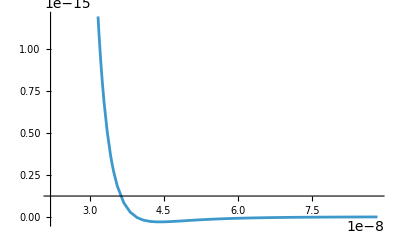

```mathematica
Plot[Evaluate[potentialElectro[d,actinRule[actinObjectRise,False]]],{d,actinObjectRise/2,actinObjectRise*2.}]
```

```mathematica
EqParams={σLJ->d/2^(1/6),σGauss->d √(3/Log[2])};
```

```mathematica
(**CONSTANTS**)


σArpCof=3.8;
compRate=0.2;
(*Mahaffy,R.E.,and Pollard,T.D.(2006).Kinetics of the formation and
dissociation of actin filament branches mediated by Arp2/3 complex.Biophys.J.91,3519–3528.*)
debranchRate=0.2(*1/s*);

(*Dominguez R,Holmes KC.Actin structure and function.Annu Rev Biophys.2011;40:169-86. doi:10.1146/annurev-biophys-042910-155359. PMID:21314430;PMCID:PMC3130349.*)
actinMonomerRise=2.76 10^-9 (*m*) ;
actinObjectRise=actinMonomerRise nCG;

(*Gittes F,Mickey B,Nettleton J,Howard J.Flexural rigidity of microtubules and actin filaments measured from thermal fluctuations in shape.J Cell Biol.1993 Feb;120(4):923-34. doi:10.1083/jcb.120.4.923.PMID:8432732;PMCID:PMC2200075.*)
Lp=17.7*10^-6(*m*); (*persistence length of actin filament*)
θp=Sqrt[(2 actinObjectRise)/Lp];


spineHeadRadius=0.125*10^-6(*m*);
overgrowthL=1.5*actinObjectRise;

avogadros=6.022*10^23;
T=310;

lowerRadiusCam=77(*Angstroms*)*10^-10;
upperRadiusCam=175(*Angstroms*)*10^-10;
middleRadiusCam=100(*Angstroms*)*10^-10;

θArp=70 (*degrees*)*π/180;
kB=1.38*10^-23(*J/K*);
kBT=kB*T;

(*Mogilner A,Oster G.Cell motility driven by actin polymerization.Biophys J.1996 Dec;71(6):3030-45. doi:10.1016/S0006-3495(96)79496-1. PMID:8968574;PMCID:PMC1233792.*)
κS=44.*10^-3(*N/m*)*1000*10^-9/actinMonomerRise;
κSmem=44.*10^-3(*N/m*)*1000*10^-9/actinMonomerRise;
σA=8.0*10^-9(*m*); (*diameter of actin molecule*)


κB=0.040*10^-24/actinObjectRise;

ϵActinLJ=d/actinObjectRise*ϵPot*nCG/.Solve[(Evaluate[D[D[4potentialElectroFunc[d,{},(σLJ/d)^6],d],d]==κS]/.EqParams)/.d->actinMonomerRise,ϵPot][[1]];
```

```mathematica
ϵActinMemLJ=d/actinObjectRise*ϵPot*nCG/.Solve[(Evaluate[D[D[4 potentialElectroFunc[d,{},(σLJ/d)^6],d],d]==κSmem]/.EqParams)/.d->actinMonomerRise,ϵPot][[1]];
actinRule[dist_,endQ_]:={ϵPotLJ->If[endQ,ϵActinMemLJ/.d->dist,ϵActinLJ/.d->dist], ϵPotGauss->0.,d0->dist,prot->ACT,ϵ->0.75,updateFunction->step,σLJ->(σLJ/.EqParams)/.{d->dist},σGauss->(σGauss/.EqParams)/.{d->dist}};

κCam=20.(*N/m*);

ϵCamLJ=ϵPot/.Solve[(Evaluate[D[D[4 potentialElectroFunc[d,{},(σLJ/d)^6],d],d]==κCam]/.EqParams),ϵPot][[1]];

κBCam=κB;
camRule[dist_,ABP_]:={ϵPotLJ->ϵCamLJ/.d->dist,ϵPotGauss->0.,d0->dist,prot->CAM,ϵ->0.75,updateFunction->If[ABP===CAM,stepCam,step],σLJ->(σLJ/.EqParams)/.{d->dist},σGauss->(σGauss/.EqParams)/.{d->dist}};


κArp=20.(*N/m*);

ϵArpLJ=ϵPot/.Solve[(Evaluate[D[D[4 potentialElectroFunc[d,{},(σLJ/d)^6],d],d]==κArp]/.EqParams),ϵPot][[1]];

arp23Height=(0.012)(*μm*)*10^-6;

arpRule[ABP_]:={ϵPotLJ->ϵArpLJ/.d->arp23Height,ϵPotGauss->0.,d0->arp23Height,prot->ARP,ϵ->0.75,updateFunction->If[ABP===ARP,stepArp,step],σLJ->(σLJ/.EqParams)/.{d->arp23Height},σGauss->(σGauss/.EqParams)/.{d->arp23Height}};

κBArp=κB;

η=19.9/2π(*Pa s*); (*Newtonian viscosity of medium*)

(*Bonilla-Quintana M, Wörgötter F, Tetzlaff C, Fauth M. Modeling the Shape of Synaptic Spines by Their Actin Dynamics. Front Synaptic Neurosci. 2020 Mar 10;12:9. doi: 10.3389/fnsyn.2020.00009. PMID: 32218728; PMCID: PMC7078677.*)
ζAct=.002(*m/(s N)*);
ζCam=.002;(*friction coefficient for cam*)
ζArp=.002;(*friction coefficient for arp*)

step[L_]:=(ζAct)/biomechanicalRate
stepCam[L_]:=(ζCam)/biomechanicalRate
stepArp[L_]:=(ζArp)/biomechanicalRate
```

```mathematica
speciesToMol=(1/avogadros)/(1000.*4/3*Pi*(area/Pi)^(3/2));

(**KINETICS OF POLYMERIZATION**)

(*Selden LA,Kinosian HJ,Estes JE,Gershman LC.Impact of profilin on actin-bound nucleotide exchange and actin polymerization dynamics.Biochemistry.1999 Mar 2;38(9):2769-78. doi:10.1021/bi981543c.PMID:10052948.*)
actinATPDissociation=0.08(*1/s*);
actinNucPhos=1.4(*1/s*);

(*Pollard TD.Rate constants for the reactions of ATP-and ADP-actin with the ends of actin filaments.J Cell Biol.1986 Dec;103(6 Pt 2):2747-54. doi:10.1083/jcb.103.6.2747.PMID:3793756;PMCID:PMC2114620.*)

kPlusBarbedT=11.6 10^6 (*1/(M s)*)*speciesToMol;
kMinusBarbedT=1.4(*1/(s)*);
kPlusPointedT=1.3 10^6(*1/(M s)*)*speciesToMol;
kMinusPointedT=0.8(*1/(s)*);
kPlusBarbedD=3.8 10^6 (*1/(M s)*)*speciesToMol;
kMinusBarbedD=7.2(*1/(s)*);
kPlusPointedD=0.16 10^6(*1/(M s)*)*speciesToMol;
kMinusPointedD=0.27(*1/(s)*);

(**KINETICS OF ACTIN NETWORKS**)

(*Smith BA,Daugherty-Clarke K,Goode BL,Gelles J.Pathway of actin filament branch formation by Arp2/3 complex revealed by single-molecule imaging.Proc Natl Acad Sci U S A.2013 Jan 22;110(4):1285-90. doi:10.1073/pnas.1211164110.Epub 2013 Jan 4. PMID:23292935;PMCID:PMC3557048.*)

kbranch=3000.(*1/(M s)*)*speciesToMol;
kminus2=0.47;
fractionArpUnbound=0.176;

(*Hayakawa K,Sekiguchi C,Sokabe M,Ono S,Tatsumi H.Real-Time Single-Molecule Kinetic Analyses of AIP1-Enhanced Actin Filament Severing in the Presence of Cofilin.J Mol Biol.2019 Jan 18;431(2):308-322. doi:10.1016/j.jmb.2018.11.010.Epub 2018 Nov 12. PMID:30439520;PMCID:PMC6507414.*)

kcapon=112*10^6(*1/(M s)*)*speciesToMol;
KdCap=23.4*10^-9(*M*);
kcapoff=KdCap*kcapon(*1/s*)/speciesToMol;
cappingFreeFraction=0.96;

(*Wioland H,Guichard B,Senju Y,Myram S,Lappalainen P,Jégou A,Romet-Lemonne G.ADF/Cofilin Accelerates Actin Dynamics by Severing Filaments and Promoting Their Depolymerization at Both Ends.Curr Biol.2017 Jul 10;27(13):1956-1967.e7.doi:10.1016/j.cub.2017.05.048.Epub 2017 Jun 15. PMID:28625781;PMCID:PMC5505867.*)
kcofcapoff=3*10^-3(*1/s*);
kcofcapon=0.3*10^6(*1/(M s)*)*speciesToMol;

(*Khan S,Conte I,Carter T,Bayer KU,Molloy JE.Multiple CaMKII Binding Modes to the Actin Cytoskeleton Revealed by Single-Molecule Imaging.Biophys J.2016 Jul 26;111(2):395-408. doi:10.1016/j.bpj.2016.06.007.PMID:27463141;PMCID:PMC4968397.*)

koffcamKIIβ=0.23 (*1/s*);
koncamKIIβ=0.5*10^6 (*1 / (M s)*)*speciesToMol;

(*Koskinen M,Hotulainen P.Measuring F-actin properties in dendritic spines.Front Neuroanat.2014;8:74. Published 2014 Aug 5. doi:10.3389/fnana.2014.00074*)
monomericFraction=0.12;

(*Bamburg JR,Minamide LS,Wiggan O,Tahtamouni LH,Kuhn TB.Cofilin and Actin Dynamics:Multiple Modes of Regulation and Their Impacts in Neuronal Development and Degeneration.Cells.2021 Oct 12;10(10):2726. doi:10.3390/cells10102726.PMID:34685706;PMCID:PMC8534876.*)
cofilinFreeFraction=0.175;

(**SYNTHESIS AND DEGRADATION OF MOLECULES**)

(*Biesemann C,Grønborg M,Luquet E,Wichert SP,Bernard V,Bungers SR,Cooper B,Varoqueaux F,Li L,Byrne JA,Urlaub H,Jahn O,Brose N,Herzog E.Proteomic screening of glutamatergic mouse brain synaptosomes isolated by fluorescence activated sorting.EMBO J.2014 Jan 13;33(2):157-70. doi:10.1002/embj.201386120.Epub 2014 Jan 10. PMID:24413018;PMCID:PMC3989609.*)

(*Sialana FJ,Wang AL,Fazari B,Kristofova M,Smidak R,Trossbach SV,Korth C,Huston JP,de Souza Silva MA,Lubec G.Quantitative Proteomics of Synaptosomal Fractions in a Rat Overexpressing Human DISC1 Gene Indicates Profound Synaptic Dysregulation in the Dorsal Striatum.Front Mol Neurosci.2018 Feb 6;11:26. doi:10.3389/fnmol.2018.00026.PMID:29467617;PMCID:PMC5808171., Bonilla-Quintana M, Rangamani P. Biophysical modeling of actin-mediated structural plasticity reveals mechanical adaptation in dendritic spines. 2022 Nov 15. doi: 10.1101/2022.11.06.515372. *)

actinDegRate=15.26284774697534/60.(*1/s*);


If[type===STUB,
(*STUBBY*)
actinInfluxRate=0.0011703842034711713/60./speciesToMol(*species/s*);
actinBasalRate=0.0011285162891759275/60./speciesToMol(*species/s*);
actinSynthRate=(actinBasalRate+actinInfluxRate)(*species/s*);
actinDegRate=5.732133029296448/60.(*1/s*);,

(*MUSHROOM*)
actinBasalRate=0.0019283704258071265/60./speciesToMol(*species/s*);
actinInfluxRate=0.0019996479973183085/60./speciesToMol(*species/s*);
actinSynthRate=(actinBasalRate+actinInfluxRate)(*species/s*);
actinDegRate=5.733176798118083/60.(*1/s*);
];

(*---------------------------------------*)


arpBasalRate=0.00015589619003090606/60./speciesToMol(*species/s*);
arpInfluxRate=0.000024424544184661355/60./speciesToMol(*species/s*);
arpSynthRate=(arpBasalRate+arpInfluxRate)(*species/s*);
arpDegRate=3.18424/60 (*1/s*);

cofilinBasalRate=0.00002830668121874591/60./speciesToMol(*species/s*);
cofilinInfluxRate=0.000046645851434562996/60/speciesToMol(*species/s*);
cofilinSynthRate=(cofilinBasalRate+cofilinInfluxRate)(*species/s*);
cofilinDegRate=3.3940933558614113/60(*1/s*);
```

```mathematica
(*McCullough BR, Grintsevich EE, Chen CK, Kang H, Hutchison AL, Henn A, Cao W, Suarez C, Martiel JL, Blanchoin L, Reisler E, De La Cruz EM. Cofilin-linked changes in actin filament flexibility promote severing. Biophys J. 2011 Jul 6;101(1):151-9. doi: 10.1016/j.bpj.2011.05.049. PMID: 21723825; PMCID: PMC3127193.*)
bareAngle=57Degree;
cofAngle=73Degree;
boundaryAngle=31Degree;

(*Okamoto K,Narayanan R,Lee SH,Murata K,Hayashi Y.The role of CaMKII as an F-actin-bundling protein crucial for maintenance of dendritic spine structure.Proc Natl Acad Sci U S A.2007 Apr 10;104(15):6418-23. doi:10.1073/pnas.0701656104.Epub 2007 Apr 2. PMID:17404223;PMCID:PMC1851051.*)
If[type===STUB,
(*STUBBY*)
camBasalRate=0.0002571539361020251/60./speciesToMol(*species/s*);
camInfluxRate=-0.00011758888249729743/60./speciesToMol(*species/s*);
camSynthRate=(camBasalRate+camInfluxRate)(*species/s*);
camDegRate=3.135/60.(*1/s*);,
(*MUSHROOM*)
camBasalRate=0.00020959506396347924/60./speciesToMol(*species/s*);
camInfluxRate=-0.0000936814091196312/60./speciesToMol(*species/s*);
camSynthRate=(camBasalRate+camInfluxRate)(*species/s*);
camDegRate=3.108/60.(*1/s*); 
];
freeCamFraction=0.34;

cappingBasalRate=1.6912568924111318*^-7/60./speciesToMol(*species/s*);
cappingInfluxRate=5.46196782460765*^-7/60./speciesToMol(*species/s*);
cappingSynthRate=(cappingBasalRate+cappingInfluxRate)(*species/s*);
cappingDegRate=0.55/60(*1/s*);

(*Roland J,Berro J,Michelot A,Blanchoin L,Martiel JL.Stochastic severing of actin filaments by actin depolymerizing factor/cofilin controls the emergence of a steady dynamical regime.Biophys J.2008 Mar 15;94(6):2082-94. doi:10.1529/biophysj.107.121988.Epub 2007 Dec 7. PMID:18065447;PMCID:PMC2257902.*)
kATPHydrolysis=0.35 (*1/s*);
ksev=0.012(*1/s*);
cofHilln=4.25;
cofKn=0.6(10^-6)^cofHilln(*M^n*);
(*Carlier MF.Measurement of Pi dissociation from actin filaments following ATP hydrolysis using a linked enzyme assay.Biochem Biophys Res Commun.1987 Mar 30 143(3):1069-75. doi:10.1016/0006-291x(87)90361-5. PMID:3566755.*)
kPiRelease=0.006(*1/s*); 
kCofPiRelease=0.035 (*1/s*);

(*Wioland H,Guichard B,Senju Y,Myram S,Lappalainen P,Jégou A,Romet-Lemonne G.ADF/Cofilin Accelerates Actin Dynamics by Severing Filaments and Promoting Their Depolymerization at Both Ends.Curr Biol.2017 Jul 10;27(13):1956-1967.e7.doi:10.1016/j.cub.2017.05.048.Epub 2017 Jun 15. PMID:28625781;PMCID:PMC5505867.https://pubmed.ncbi.nlm.nih.gov/28625781/Nonehttps://pubmed.ncbi.nlm.nih.gov/28625781/HyperlinkActionRecycledHyperlinkActive*)
kOnCofEdge=17*10^6(*1/(M s)*)*speciesToMol ;
kOffCof=0.7(*1/s*);
kMinusBarbedCof=4.0(*1/s*);
kMinusPointedCof=3.3(*1/s*);

(*De La Cruz EM.How cofilin severs an actin filament.Biophys Rev.2009 May 15;1(2):51-59. doi:10.1007/s12551-009-0008-5. PMID:20700473;PMCID:PMC2917815.https://pubmed.ncbi.nlm.nih.gov/20700473/Nonehttps://pubmed.ncbi.nlm.nih.gov/20700473/HyperlinkActionRecycledHyperlinkActive*)
kOnSingleCof=10^4(*1/(M s*)*speciesToMol ;


(*https://pmc.ncbi.nlm.nih.gov/articles/PMC10152144/*)
kArpNuc=3.23(*1/s*);
kNucOff=7.9*10^-3(*1/s*);

(**FACTORS**)
initActinADPNum=0.;

meshSpacing=0.04*10^-6;

upperBound=meshSpacing*5./4.;
lowerBound=meshSpacing*4./5.;
```

### Curve-Fitting CamKIIβ and Aip1 (capping) Degradation Rates

Hyperlink[(*Bosch M,Castro J,Saneyoshi T,Matsuno H,Sur M,Hayashi Y.Structural and molecular remodeling of dendritic spine substructures during long-term potentiation.Neuron.2014 Apr 16;82(2):444-59. doi:10.1016/j.neuron.2014.03.021.PMID:24742465;PMCID:PMC4281348.*),{URL["https://pubmed.ncbi.nlm.nih.gov/24742465/"], None},Apply[Sequence, {ActiveStyle -> {"HyperlinkActive"}, BaseStyle -> {"Hyperlink"}, HyperlinkAction -> "Recycled"}]]

```mathematica
eq=ParametricNDSolveValue[{m'[t]==((influx)(1-HeavisideTheta[t-1.])+ks-km m[t]*monomericFraction),m[4.]==3000.*10^-6},m,{t,0.0,10.},{ks,km,influx}];
```

```mathematica
actinData={{0,1},{1/3,1.5/1.25},{4/5,2.55/1.85},{1.15,3.5/2.5},{1.501,3.75/2.85},{1.75,3.6/2.85},{2,3.15/2.7},{2.3,2.75/2.5},{2.75,2.6/2.4},{3,2.5/2.3},{3.25,2.4/2.2},{3.75,2.3/2.1},{4.,2.1/2.}};
actinData[[;;,2]]*=3000.*10^-6;
nlm=NonlinearModelFit[actinData,{eq[ks,km,influx][t]},{influx,km,ks},t];
```

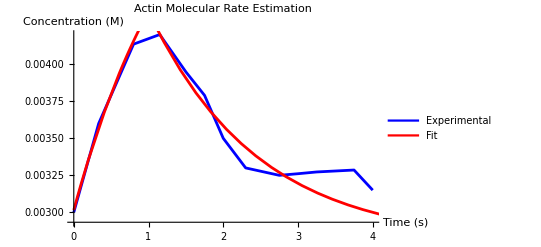

{influx→0.00199965,km→5.73318,ks→0.00192837}

| Estimate | Standard Error | t-Statistic | P-Value
influx | 0.00199965 | 0.000227796 | 8.77825 | 5.17564×10^-6
km | 5.73318 | 1.23876 | 4.62816 | 0.000938803
ks | 0.00192837 | 0.000480805 | 4.01071 | 0.00247521

```mathematica
actinPlot=Legended[Show[{ListLinePlot[actinData,PlotRange->{{0,4},Full},PlotStyle->Blue],Plot[(eq[ks,km,influx][t])/.nlm["BestFitParameters"],{t,0.0,10},PlotRange->{{0,4},Full},PlotStyle->Red]},PlotLabel->"Actin Molecular Rate Estimation",AxesLabel->{"Time (s)","Concentration (M)"}],LineLegend[{Blue,Red},{"Experimental","Fit"}]]
Print[Join[nlm["BestFitParameters"]]];
Print[nlm["ParameterTable"]];
```

```mathematica
xbase=804.;ybase=1082.;xunit=836.-800.;yunit=1218-1182;
```

```mathematica
arpDataVol=SortBy[Import["~/ResultsArpVol.csv"][[2;;,-2;;]][[;;-3]],First];arpDataProt=SortBy[Import["~/ResultsArp.csv"][[2;;,-2;;]][[;;-3]],First];
```

$Aborted

```mathematica
arpDataVol=(#-{arpDataVol[[1,1]],arpDataVol[[1,2]]}&/@arpDataVol)//Abs;arpDataProt=(#-{arpDataProt[[1,1]],arpDataProt[[1,2]]}&/@arpDataProt)//Abs;
```

```mathematica
arpData={arpDataProt[[;;,1]]/xunit,(arpDataProt[[;;,2]]+yunit)/(arpDataVol[[;;,2]]+yunit)}//Transpose;arpData=arpData[[2;;]];
```

```mathematica
arpData[[;;,2]]*=256.*10^-6;
```

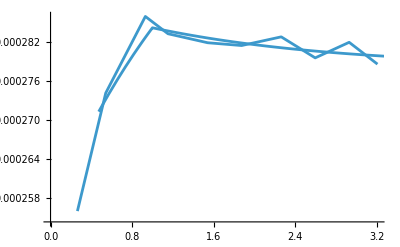

{influx→0.0000244245,km→3.18424,ks→0.000155896}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
influx | 0.0000244245 | 0.0000103982 | 2.34893 | 0.0511682
km | 3.18424 | 4.86981 | 0.653874 | 0.534076
ks | 0.000155896 | 0.000241964 | 0.644294 | 0.539915

```mathematica
eq=ParametricNDSolveValue[{m'[t]==((influx)(1-HeavisideTheta[t-1.])+ks-km m[t]*fractionArpUnbound),m[0]==256.*10^-6},m,{t,0.0,10.},{ks,km,influx}];

nlm=NonlinearModelFit[arpData,{eq[ks,km,influx][t],0<km<10.},{influx,km,ks},t];
Show[{ListLinePlot[arpData],Plot[eq[ks,km,influx][t]/.Join[nlm["BestFitParameters"]],{t,0,4}]}]
Print[Join[nlm["BestFitParameters"]]];
Print[nlm["ParameterTable"]];
```

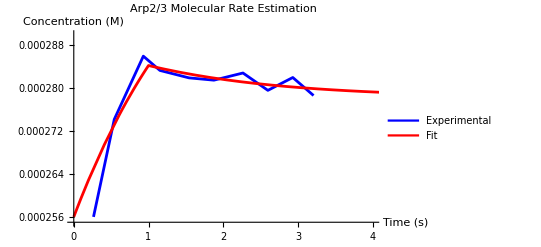

{influx→0.0000244245,km→3.18424,ks→0.000155896}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
influx | 0.0000244245 | 0.0000103982 | 2.34893 | 0.0511682
km | 3.18424 | 4.86981 | 0.653874 | 0.534076
ks | 0.000155896 | 0.000241964 | 0.644294 | 0.539915

```mathematica
arpPlot=Legended[Show[{ListLinePlot[arpData,PlotRange->{{0,4},{0.000255,0.00029}},PlotStyle->Blue],Plot[(eq[ks,km,influx][t])/.nlm["BestFitParameters"],{t,0.0,10},PlotRange->{{0,4},{0.000255,0.00029}},PlotStyle->Red]},PlotLabel->"Arp2/3 Molecular Rate Estimation",AxesLabel->{"Time (s)","Concentration (M)"}],LineLegend[{Blue,Red},{"Experimental","Fit"}]]
Print[Join[nlm["BestFitParameters"]]];
Print[nlm["ParameterTable"]];
```

```mathematica
camData={{0,1},{1/3,1.15/1.4},{2/3,1.35/1.7},{1.001,1.45/2.7},{4/3,1.475/2.85},{5/3,1.5/2.8},{2,1.46/2.75},{7/3,1.46/2.7},{8/3,1.462/2.7},{3,1.46/2.5},{10/3,1.4/2.2},{11/3,1.35/2.},{4,1.35/2.}};camData[[;;,2]]*=400.*10^-6;
```

```mathematica
eq=ParametricNDSolveValue[{m'[t]==((influx)(1-HeavisideTheta[t-1.])+ks-km m[t]*freeCamFraction),m[0]==400.*10^-6},m,{t,0.0,10.},{ks,km,influx}];
```

ParametricNDSolveValue::mdata: An invalid NDSolve`SensitivityMethod method data object was encountered at the point t == 0..

General::stop: Further output of ParametricNDSolveValue::mdata will be suppressed during this calculation.

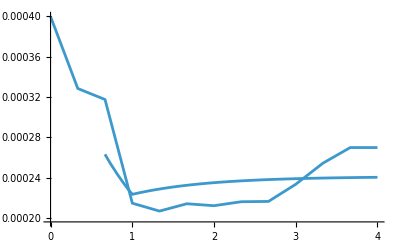

{influx→-0.000117589,km→3.13516,ks→0.000257154}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
influx | -0.000117589 | 0.0000737568 | -1.59428 | 0.141958
km | 3.13516 | 3.23988 | 0.967678 | 0.356026
ks | 0.000257154 | 0.000258099 | 0.996339 | 0.342583

```mathematica
nlm=NonlinearModelFit[camData,{eq[ks,km,influx][t],0<km<10.},{influx,km,ks},t];
Show[{ListLinePlot[camData],Plot[eq[ks,km,influx][t]/.nlm["BestFitParameters"],{t,0,4}]}]
Print[nlm["BestFitParameters"]];
Print[nlm["ParameterTable"]];
```

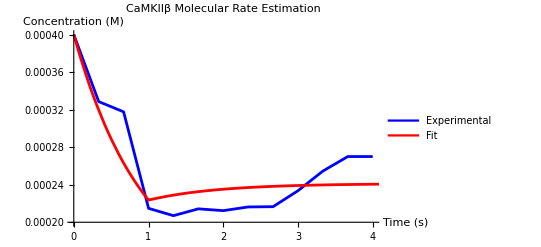

{influx→-0.000117589,km→3.13516,ks→0.000257154}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
influx | -0.000117589 | 0.0000737568 | -1.59428 | 0.141958
km | 3.13516 | 3.23988 | 0.967678 | 0.356026
ks | 0.000257154 | 0.000258099 | 0.996339 | 0.342583

```mathematica
camPlot=Legended[Show[{ListLinePlot[camData,PlotRange->{{0,4},{0.0002,0.0004}},PlotStyle->Blue],Plot[(eq[ks,km,influx][t])/.nlm["BestFitParameters"],{t,0.0,10},PlotRange->{{0,4},{0.0002,0.0004}},PlotStyle->Red]},PlotLabel->"CaMKIIβ Molecular Rate Estimation",AxesLabel->{"Time (s)","Concentration (M)"}],LineLegend[{Blue,Red},{"Experimental","Fit"}]]
Print[Join[nlm["BestFitParameters"]]];
Print[nlm["ParameterTable"]];
```

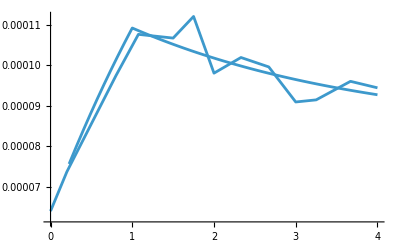

{influx→0.0000466459,km→3.39409,ks→0.0000283067}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
influx | 0.0000466459 | 5.411×10^-6 | 8.62056 | 6.08488×10^-6
km | 3.39409 | 4.17682 | 0.812602 | 0.435365
ks | 0.0000283067 | 0.0000418308 | 0.676694 | 0.513948

```mathematica
cofData={{0,1},{0.2,1.9/1.65},{0.8,3.5/2.3},{1.075,4.875/2.9},{1.5,5./3.},{1.75,4.9/2.8},{2,4.25/2.775},{2.33,3.9/2.45},{2.67,3.5/2.25},{3.,3.125/2.2},{3.25,3./2.1},{3.67,3./2.},{4.,2.95/2.}};
cofData[[;;,2]]*=64.*10^-6;

eq=ParametricNDSolveValue[{m'[t]==((influx)(1-HeavisideTheta[t-1.])+ks-km m[t]*0.1),m[0]==64.*10^-6},m,{t,0.0,10.},{ks,km,influx}];

nlm=NonlinearModelFit[cofData,{eq[ks,km,influx][t],0<km<10.},{influx,km,ks},t];
Show[{ListLinePlot[cofData],Plot[eq[ks,km,influx][t]/.nlm["BestFitParameters"],{t,0,4}]}]
Print[nlm["BestFitParameters"]];
Print[nlm["ParameterTable"]];
```

```mathematica
3.3940933558614113/60.
```

0.0565682

```mathematica
aip1VolPoints={{1389,1170},{1415.5,1142.5},{1436.5,1097.5},{1460.5,1049.5},{1484.5,1034.5},{1505.5,1016.5},{1529.5,1010.5},{1550.5,1013.5},{1574.5,1022.5},{1598.5,1028.5},{1622.5,1049.5},{1640.5,1073.5},{1667.5,1094.5}};
aip1ConcPoints={1170,1142.5,1082.5,1025.5,992.5,983.5,974.5,974.5,980.5,995.5,1025.5,1055.5,1076.5};
aip1VolPoints[[;;,1]]-=1322.5;
aip1ConcPoints=aip1ConcPoints-1220.5;
aip1ConcPoints*=-1;
aip1VolPoints[[;;,2]]-=1220.5;
aip1VolPoints[[;;,2]]*=-1;
aip1VolPoints[[;;,2]]=aip1ConcPoints/aip1VolPoints[[;;,2]];
aip1VolPoints[[;;,1]]=aip1VolPoints[[;;,1]]/aip1VolPoints[[1,1]]-1.;
```

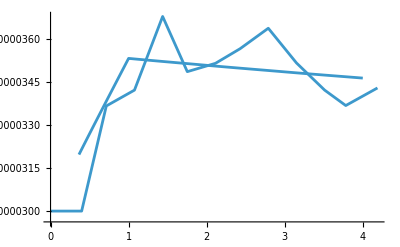

{influx→5.46197×10^-7,km→0.550883,ks→1.69126×10^-7}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
influx | 5.46197×10^-7 | 2.22661×10^-7 | 2.45305 | 0.0340797
km | 0.550883 | 12.8667 | 0.0428146 | 0.966692
ks | 1.69126×10^-7 | 4.49285×10^-6 | 0.0376433 | 0.970713

```mathematica
aip1Data=aip1VolPoints;
aip1Data[[;;,2]]*=3.*10^-6;

eq=ParametricNDSolveValue[{m'[t]==((influx)(1-HeavisideTheta[t-1.])+ks-km m[t]*.1),m[0]==3.*10^-6},m,{t,0.0,10.},{ks,km,influx}];

nlm=NonlinearModelFit[aip1Data,{eq[ks,km,influx][t],0<km<10.},{influx,km,ks},t];
Show[{ListLinePlot[aip1Data],Plot[eq[ks,km,influx][t]/.nlm["BestFitParameters"],{t,0,4}]}]
Print[nlm["BestFitParameters"]];
Print[nlm["ParameterTable"]];
```

### Definition of Rules

```mathematica
(*Bonilla-Quintana M,Wörgötter F,Tetzlaff C,Fauth M.Modeling the Shape of Synaptic Spines by Their Actin Dynamics.Front Synaptic Neurosci.2020 Mar 10;12:9. doi:10.3389/fnsyn.2020.00009.PMID:32218728*)
kappa=.0005*10^-18;
ζIn=0.002;
```

We also define a function for getting the relative position after rotation which works with vectorized coordinates.

```mathematica
newPos[oldPos_?VectorQ, angIn_] :=({{
 {Cos[angIn], -Sin[angIn]},
 {Sin[angIn], Cos[angIn]}
}} . oldPos)[[1]];
```

## Visualizing The Actin Network

### Visualizer

This is the legend for visualizing actin networks:
- Circles: Actin objects
- Squares: Arp objects
- Triangles: Capping objects
- Hexagons: CamKIIβ objects
- Edge medium thickness indicates Actin-ATP and edge no thickness indicates Actin-ADP
- Opacity indicates degree of cofilin binding
- Color indicates bending angle

```mathematica
VisualizeActinSnapshot[initMoleculeList_,verbose_,energyMap_]:=Module[{ml=initMoleculeList,viz,stack,pointCells,curCell,prevCell,color,prevPos,energyFunc,vizLines,vizSpine,nextSpine,moleculeList,partnerCoords,shapeRadius=3.*10^-9,ABPObjects,curCam,spineCells,i,camObjects,nextABP,nucAct,poiCell,camNext1,camNext2,pushABPBranch},(*---helper:push ABP glyph+seed its nucleated actin branch onto stack---*)pushABPBranch[abp_,origin_]:=(AppendTo[viz,{Black,Line[{abp[[2]],origin}]}];
AppendTo[viz,{energyFunc[0.],Rectangle[abp[[2]]-{shapeRadius,shapeRadius},abp[[2]]+{shapeRadius,shapeRadius}]}];
If[abp[[3]]=!=nullPointer,nucAct=Select[moleculeList,#[[1]]==abp[[3]]&][[1]];
PrependTo[stack,{abp,nucAct,Black,abp[[2]]}];
PrependTo[viz,{Black,Line[{abp[[2]],nucAct[[2]]}]}];
AppendTo[viz,{energyFunc[abp[[4]]],Rectangle[abp[[2]]-{shapeRadius,shapeRadius},abp[[2]]+{shapeRadius,shapeRadius}]}]];);
(*initialize the stack and viz lists*)stack={};
viz={};
vizLines={};
vizSpine={Black};
ABPObjects=Cases[ml,ABP[__]];
camObjects=Cases[ml,cam[__]];
spineCells=Cases[ml,spine[__]];
moleculeList=DeleteCases[initMoleculeList,spine[__]];
For[i=1,i<=Length[spineCells],i++,nextSpine=Cases[spineCells,spine[spineCells[[i,3]],__]][[1]];
AppendTo[vizSpine,Line[{spineCells[[i,2]],nextSpine[[2]]}]];];
energyFunc[ang_]:=ColorData["TemperatureMap"][ang^2/(boundaryAngle)^2];
(*seeds we start DFS from—pointed ends and any actinJuncEnd that has a next*)pointCells=Join[Cases[moleculeList,pointedEnd[__]],Select[Cases[moleculeList,actinJuncEnd[__]],#[[3]]!=nullPointer&],Cases[moleculeList,ABP[__,0.,_]]];
(*Iterate through all of the seed terminals*)While[Length[pointCells]!=0,poiCell=First@pointCells;
pointCells=Rest@pointCells;
(*draw symbol for the seed terminal*)Which[Head[poiCell]===pointedEnd,AppendTo[viz,{energyFunc[0.],Disk[poiCell[[2]],shapeRadius]}],
Head[poiCell]===ABP,AppendTo[viz,{energyFunc[0.],Rectangle[poiCell[[2]]-{shapeRadius,shapeRadius},poiCell[[2]]+{shapeRadius,shapeRadius}]}],
Head[poiCell]===actinJuncEnd,(*optional ABP spur if present;
don't assume a next here*)
If[Length@ABPObjects>0,With[{cand=Cases[ABPObjects,ABP[poiCell[[4]],__]]},If[cand=!={},nextABP=First@cand;
(*draw connector and ABP glyph*)AppendTo[viz,{Black,Line[{nextABP[[2]],poiCell[[2]]}]}];
AppendTo[viz,{energyFunc[0.],Rectangle[nextABP[[2]]-{shapeRadius,shapeRadius},nextABP[[2]]+{shapeRadius,shapeRadius}]}];
(*if this actinJuncEnd is terminal,seed the nucleated branch*)pushABPBranch[nextABP,poiCell[[2]]];];];];
(*draw junction-like triangle for junc-end*)AppendTo[viz,Triangle[{{poiCell[[2,1]],poiCell[[2,2]]+shapeRadius},poiCell[[2]]+{-shapeRadius,-shapeRadius},poiCell[[2]]+{+shapeRadius,-shapeRadius}}]]];
(*initialize stack ONLY if seed has a next pointer (do NOT clear stack otherwise)*)If[Length[poiCell]>=3&&poiCell[[3]]=!=nullPointer,PrependTo[stack,{poiCell,Select[moleculeList,#[[1]]==poiCell[[3]]&][[1]],Black,poiCell[[2]]}]];
(*DFS traversal*)While[Length[stack]!=0,prevCell=stack[[1,1]];
curCell=stack[[1,2]];
color=stack[[1,3]];
prevPos=stack[[1,4]];
stack=Rest@stack;
(*edge*)PrependTo[vizLines,{Black,Line[{curCell[[2]],prevPos}]}];
(*node glyph& color*)If[Head[curCell]===cap,(*cap:triangle pointing "forward"*)AppendTo[viz,{Black,Triangle[{{curCell[[2,1]],curCell[[2,2]]-shapeRadius},curCell[[2]]+{-newPos[{0,shapeRadius},Pi/3][[1]],newPos[{0,shapeRadius},Pi/3][[2]]},curCell[[2]]+{+newPos[{0,shapeRadius},Pi/3][[1]],newPos[{0,shapeRadius},Pi/3][[2]]}}]}],(*monomer/ends*)AppendTo[viz,{If[Head[curCell]===barbedEnd,Green,If[curCell[[-1]]=!=cofilin,energyFunc[curCell[[If[MemberQ[{actinJunc,actinJuncEnd},Head[curCell]],5,4]]]],energyFunc[curCell[[If[MemberQ[{actinJunc,actinJuncEnd},Head[curCell]],5,4]]]/Sqrt[5]]]],If[MemberQ[{actinJunc,actinJuncEnd},Head[curCell]],Triangle[{{curCell[[2,1]],curCell[[2,2]]+shapeRadius},curCell[[2]]+{-shapeRadius,-shapeRadius},curCell[[2]]+{+shapeRadius,-shapeRadius}}],Disk[curCell[[2]],shapeRadius]]}];
If[verbose,AppendTo[viz,{Black,Text[ToString@Round[curCell[[1]]],curCell[[2]]]}]];];
(*ABP spur/nucleation if we land on a junction core or a terminal junction end*)If[Head[curCell]===actinJunc||(Head[curCell]===actinJuncEnd&&curCell[[3]]===nullPointer),With[{cand=Cases[ABPObjects,ABP[curCell[[4]],__]]},If[cand=!={},nextABP=First@cand;
pushABPBranch[nextABP,curCell[[2]]];];];];
(*push forward only if not terminal and pointer is valid*)If[(Head[curCell]=!=cap&&Head[curCell]=!=barbedEnd)&&curCell[[3]]=!=nullPointer,PrependTo[stack,{curCell,Select[moleculeList,#[[1]]==curCell[[3]]&][[1]],Black,curCell[[2]]}]];];];
(*CAM edges to two neighbors*)For[i=1,i<=Length[camObjects],i++,camNext1=Cases[moleculeList,actin[camObjects[[i,3]],__]][[1]];
camNext2=Cases[moleculeList,actin[camObjects[[i,4]],__]][[1]];

PrependTo[vizSpine,Line[{camNext1[[2]],camObjects[[i,2]]}]];
PrependTo[vizSpine,Line[{camNext2[[2]],camObjects[[i,2]]}]];
PrependTo[vizSpine,{If[energyMap,energyFunc[camObjects[[i,5]]],Black],RegularPolygon[camObjects[[i,2]],middleRadiusCam,12],Black}];];
{Length[moleculeList],Flatten[Prepend[Prepend[viz,vizLines],vizSpine]],BarLegend[{"TemperatureMap",{0,2}}]}]
```

```mathematica
(* function to grab a list of all the actin types from full simulation *)
makeMoleculeLists[simulationArray_] := 
Join[Cases[simulationArray,actin[__]],Cases[simulationArray,spine[ __]],Cases[simulationArray,ABP[ __]],Cases[simulationArray,cam[ __]],Cases[simulationArray,barbedEnd[ __]],Cases[simulationArray,pointedEnd[ __]],Cases[simulationArray,actinJunc[ __]],Cases[simulationArray,cap[ __]],Cases[simulationArray,actinJuncEnd[ __]]]
```

```mathematica
(* function to return graphics list for all snapshots in a sim *)
vizSim[simulationArray_, verbose_, energyMap_,n_:10,tmax_:0.] := Module[{vizList,dt,mLists,bbox,timePos,t,start,simList={}},
mLists = makeMoleculeLists[#]&/@simulationArray[[;;,2]];
bbox = {White,Rectangle[{Min[Flatten[Map[#[[2,1]]&,#]&/@mLists]]-2actinObjectRise, Min[Map[#[[2,2]]&, Flatten[mLists]]]-2actinObjectRise}, {Max[Flatten[Map[#[[2,1]]&,#]&/@mLists]]+2actinObjectRise, Max[Map[#[[2,2]]&, Flatten[mLists]]]+2actinObjectRise}]};
timePos={(Max[Flatten[Map[#[[2,1]]&,#]&/@mLists]]+Min[Flatten[Map[#[[2,1]]&,#]&/@mLists]])/2,Max[Flatten[Map[#[[2,2]]&,#]&/@mLists]]+actinObjectRise};
simList=Transpose[{simulationArray[[;;,1]],mLists}];
vizList=Map[Graphics[Join[bbox,Append[VisualizeActinSnapshot[#[[2]],verbose,True][[2]],{Black,Text[Style["Time: "<>ToString[Round[(#[[1]]*1000)]/1000.]<>" secs."],timePos]}],{Line[{{0,Min[Map[#[[2,2]]&, Flatten[mLists]]]-actinObjectRise},{2actinObjectRise,Min[Map[#[[2,2]]&, Flatten[mLists]]]-actinObjectRise}}],Text[ToString[N@Round[actinObjectRise*2*100*10^9]/100]<>"nm",{actinObjectRise,Min[Map[#[[2,2]]&, Flatten[mLists]]]-1.75actinObjectRise}]}]//Flatten]&,simList]
];
sampleSimDirect[directory_]:=
Module[{files,simList,maxTime,simNumbers,fgi,filegroups,simulationArray,t,sim,i,j,globString="simSpine*.wls"},
simList={};
files=directory<>"/"<>#<>".wls"&/@SortBy[FileBaseName[#]&/@FileNames[directory<>"/"<>globString],processFileNames];

simNumbers=Range[Length@filegroups];
simulationArray={};
For[i=1,i<=Length@files,i+=1,
sim=Import[files[[i]]];
AppendTo[simulationArray,sim];
];
simulationArray
]
```

```mathematica
animateGrowth[simulationArray_,verbose_:False] := Module[{mLists,bbox,timePos,xs,ys},
mLists = makeMoleculeLists/@simulationArray[[;;,2]];
xs=#[[1]]&/@Select[#[[2]]&/@mLists[[-1]],ListQ];
ys=#[[2]]&/@Select[#[[2]]&/@mLists[[-1]],ListQ];
bbox = RegionBounds[Rectangle[{Min[xs]-2.actinObjectRise, Min[ys]-2.actinObjectRise}, {Max[xs]+2.actinObjectRise, Max[ys]+2.actinObjectRise}]];
timePos={(Max[xs]+Min[xs])/2,Max[ys]+actinObjectRise};
frames=Map[Show[{Graphics[Join[Append[VisualizeActinSnapshot[#[[2]],verbose,True][[2]],{Black,Text[Style["Time: "<>ToString[#[[1]]]<>", Frame: "<>ToString[#[[3]]],Bold,FontColor->Darker[LightBlue]],timePos]}]//Flatten],PlotRange->bbox]}]&, Transpose[{#[[1]]&/@simulationArray,mLists,Range[Length@simulationArray]}]];
ListAnimate[frames]
];

processFileNames[name_]:=
ToExpression@StringDelete[name,LetterCharacter]

animateGrowthDirectory[directory_,globString_,outDir_,dt_:0.01] := Module[{maxis,frameN,xs,ys,start,simList,t,mLists,bbox,timePos,files,lastFrame,i,j,frameNumber,frames},
files=SortBy[FileBaseName[#]&/@FileNames[directory<>globString],processFileNames];
files=directory<>#<>".wls"&/@files;
simList=sampleSimDirect[directory];

mLists = makeMoleculeLists[#[[2]]]&/@simList;
xs=#[[1]]&/@Select[#[[2]]&/@mLists[[-1]],ListQ];
ys=#[[2]]&/@Select[#[[2]]&/@mLists[[-1]],ListQ];
bbox = RegionBounds[Rectangle[{Min[xs]-2actinObjectRise, Min[ys]-2actinObjectRise}, {Max[xs]+2actinObjectRise, Max[ys]+2actinObjectRise}]];
timePos={(Max[xs]+Min[xs])/2,Max[ys]+actinObjectRise};
simList=Transpose[{Range[0,Length@mLists-1]*dt,mLists}];
CreateDirectory[outDir];
frameNumber=0;
frames=Map[Graphics[Join[Append[VisualizeActinSnapshot[#[[2]],False,True][[2]],{Black,Text[Style["Time: "<>ToString[NumberForm[#[[1]],{5,4}]]<>" s.",Bold,FontSize->14,FontColor->Darker[LightBlue]],timePos]}]]//Flatten,PlotRange->bbox]&,simList];
For[j=1,j<=Length@frames,j++,
frameNumber++;
Export[outDir<>"frame_"<>IntegerString[frameNumber,10,8]<>".png",frames[[j]]];
];
];

animateGrowthDirectorySet[directory_,globString_,outDir_,dimensions_,dt_:0.001,plotSims_:False,plotAreas_:False] := Module[{simPlots,simList,minLength,areaPlots,start,t,mLists,bbox,timePos,files,end,lastFrame,frames,simulationArray,frame,groupfiles,filegroups,fgi,maxTime,simSubList,xs,ys,maxis,simNumbers,i,j,sim,dim},
simList={};
groupfiles=FileNames[directory];
groupfiles=DeleteCases[groupfiles,DirectoryName[directory]<>".DS_Store"];
filegroups={};
For[i=1,i<=Length@groupfiles,i++,
AppendTo[filegroups,(groupfiles[[i]]<>"/"<>#<>".wls"&/@SortBy[FileBaseName[#]&/@FileNames[groupfiles[[i]]<>"/"<>globString],processFileNames])];
];

maxTime=Max[Import[#[[-1]]][[2,-1,1]]&/@filegroups];
simList={};
progressbar=StringRepeat["|",1]<>StringRepeat[" ",Length@filegroups-1]<>"|";
Print[Dynamic[progressbar]];
simNumbers=Range[Length@filegroups];
For[fgi=1,fgi<=Length@filegroups,fgi++,
files=filegroups[[fgi]];
simulationArray={};
t=0;
For[i=1,i<=Length@files,i+=1,
sim=Import[files[[i]]][[2]];
For[j=1,j<=Length@sim,j++,
If[sim[[j,1]]>=t,
AppendTo[simulationArray,sim[[j,2]]];
t+=dt;
]
]
];
AppendTo[simList,simulationArray];
progressbar=StringRepeat["|",fgi]<>StringRepeat[" ",Length@filegroups-fgi]<>"|";
];

simList=simList[[;;,2;;]];

dim=QuotientRemainder[Length@filegroups,Floor[Sqrt@Length@filegroups]];

minLength=Min[Length@#&/@simList];
mLists = makeMoleculeLists/@#&/@simList;

If[plotSims,
simPlots=GraphicsGrid[Partition[plotSim[#]&/@(Transpose@#&/@(Transpose@{dt*Range[0,minLength-1.]&/@simList,simList[[;;,;;minLength]]})),dimensions],Frame->All];

Export[outDir<>"simPlots.jpeg",simPlots];
];
If[plotAreas,
areaPlots=GraphicsGrid[Partition[membraneAreaPlotter[#,"Membrane Area Over Time",{Automatic,{0.005,0.025}}]&/@(Transpose@#&/@(Transpose@{dt*Range[0,minLength-1.]&/@simList,simList[[;;,;;minLength]]})),dimensions],Frame->All];
Export[outDir<>"areaPlots.jpeg",areaPlots];
];

simList=Transpose@{Range[0,Length@#]&/@mLists,mLists};

xs=(#[[1]]&/@#&/@Select[#[[2]]&/@#&/@mLists[[;;,-1]],ListQ])//Flatten;
ys=(#[[2]]&/@#&/@Select[#[[2]]&/@#&/@mLists[[;;,-1]],ListQ])//Flatten;
bbox = RegionBounds[Rectangle[{Min[xs]-2actinObjectRise, Min[ys]-2actinObjectRise}, {Max[xs]+2actinObjectRise, Max[ys]+2actinObjectRise}]];
timePos={(Max[xs]+Min[xs])/2,Max[ys]+actinObjectRise};

maxis=Length@#&/@mLists;
CreateDirectory[outDir];
If[dim[[2]]!=0,dim=dim[[1]]-1;,dim=dim[[1]];];
Do[frame=GraphicsRow[{GraphicsGrid[Partition[(Graphics[Join[(VisualizeActinSnapshot[simList[[#]][[2]][[Min[{maxis[[#]],frameN+1}]]],False,True][[2]]),{Black,Text[Style["Time: "<>ToString[NumberForm[simList[[#]][[1]][[Min[{maxis[[#]],frameN+1}]]]*dt,{5,4}]]<>" s.",Bold,FontSize->14,FontColor->Darker[LightBlue]],timePos]},{Line[{{0,Min[ys]-actinObjectRise},{2actinObjectRise,Min[ys]-actinObjectRise}}],Text[ToString[N@Round[actinObjectRise*2*1000]/1000]<>" μm",{actinObjectRise,Min[ys]-1.75actinObjectRise}]}],PlotRange->bbox]&/@Range[1,Length@filegroups]),dimensions],Frame->All],BarLegend[{"TemperatureMap",{0,κB/2*π/4}},LegendFunction->"Frame",LegendLabel->"Bending Energy in Joules"]},Frame->True];Export[outDir<>"frame_"<>IntegerString[frameN,10,8]<>".png",frame];,{frameN,0,Max@maxis}];
];
```

### Plotting

```mathematica
plotSim[simulationArray_,slices_:1] := Module[{totalActin=Map[{#[[1]],Length[Select[#[[2]], Head[#]===barbedEnd&]]*nCG+Length[Select[#[[2]], Head[#]===actinJunc&]]*nCG+Length[Select[#[[2]], Head[#]===actinJuncEnd&&#[[3]]==nullPointer&]]*nCG+Length[Select[#[[2]], Head[#]===actin&]]*nCG+Length[Select[#[[2]], Head[#]===cap&]]*nCG+Abs[Cases[#[[2]],actinATPCount[_]][[1,1]]]+Abs[ Cases[#[[2]], actinADPCount[_]][[1, 1]]]} &, simulationArray[[1;;Length@simulationArray;;slices]]],SA=simulationArray[[1;;Length@simulationArray;;slices]],data},
data={
Map[{#[[1]],nCG (Length[Select[#[[2]], Head[#]===actin&]]+Length[Select[#[[2]], Head[#]===actinJunc&]]+Length[Select[#[[2]], Head[#]===actinJuncEnd&&#[[3]]==nullPointer&]]+Length[Select[#[[2]], Head[#]===barbedEnd&]]+Length[Select[#[[2]], Head[#]===cap&]])} &, SA],
Map[{#[[1]],nCG*Total[If[Head[#]===actin||Head[#]===actinJunc,Boole[#[[-1]]==cofilin],0]&/@#[[2]]]} &, SA],
Map[{#[[1]], Cases[#[[2]], actinATPCount[_]][[1, 1]]+ Cases[#[[2]], actinADPCount[_]][[1, 1]]} &, SA],
totalActin,
Map[{#[[1]], Cases[#[[2]],actinATPCount[_]][[1,1]]} &, SA],
Map[{#[[1]], Cases[#[[2]], actinADPCount[_]][[1, 1]]} &, SA]};
ListLinePlot[data,PlotLegends -> {"Polymerized Actin","Bound Cofilin", "Free Actin","Total Actin","G-Actin-ATP","G-Actin-ADP"},PlotRange->{{simulationArray[[1,1]],simulationArray[[-1,1]]},{0,Max[totalActin]}},Frame->True,FrameLabel->{"Time (s)",""},PlotLabel->"Plot of Number of Molecules"]
]
```

## Molecule Rules

Here we define the rules that govern the changes in the number of free molecules without a change in the actin network structure. There is one rule that changes the type of bound nucleotide to actins in filaments. We have ARP synthesis and degradation, actin synthesis and degradation, actin-ADP and actin-ATP dissociation, F-Actin hydrolysis (conversion of F-actin-ATP to F-actin-ADP).

```mathematica
(* rules for ARP synthesizing and degrading *)
rulesMolVanilla = {
(* ARP synthesis *)
{arpCount[numArp],spineHeadArea[area]} -> {arpCount[numArp],spineHeadArea[area]},
solving[numArp'==arpRate Boole[numArp>0]],

(* ARP degradation *)
(arpCount[numArp] -> arpCount[numArp]),
solving[numArp'==-arpDegRate *numArp  Boole[numArp>0]],

(* Cap synthesis *)
{cappingCount[numCap],spineHeadArea[area]} -> {cappingCount[numCap],spineHeadArea[area]},
solving[numCap'==cappingSynthRate],

(* Cap degradation *)
(cappingCount[numCap] -> cappingCount[numCap ]),
solving[numCap'==-cappingDegRate *numCap  Boole[numCap>0]],

(* Cam synthesis *)
{camCount[numCam],spineHeadArea[area]} -> {camCount[numCam],spineHeadArea[area]},
solving[numCam'==camRate],

(* Cam degradation *)
(camCount[numCam] -> camCount[numCam]),
solving[numCam'==-camDegRate *numCam  Boole[numCam>0]],

(* Cofilin synthesis *)
{cofilinCount[numCofilin],spineHeadArea[area]} -> {cofilinCount[numCofilin],spineHeadArea[area]},
solving[numCofilin'==cofRate],

(* Cofilin degradation *)
(cofilinCount[numCofilin] -> cofilinCount[numCofilin]),
solving[numCofilin'==-cofilinDegRate *numCofilin  Boole[numCofilin>0]],

(* Actin synthesis *)
{actinATPCount[numActin],spineHeadArea[area]} -> {actinATPCount[numActin],spineHeadArea[area]},
solving[numActin'==actinRate],

(* Actin degradation *)
({actinATPCount[numActin] ,spineHeadArea[area]}->{ actinATPCount[numActin],spineHeadArea[area]}),
solving[numActin'==-actinDegRate *numActin  Boole[numActin>0]],

{actinADPCount[numActin] ,spineHeadArea[area]}->{actinADPCount[numActin],spineHeadArea[area]},
solving[numActin'==-actinDegRate *numActin  Boole[numActin>0]]
};

rulesPiRelease={
(*Hydrolysis of F-Actin-Nucleotides*)
{actin[ID,coords,IDNext,ang,ATP],spineHeadArea[area]}->{actin[ID,coords,IDNext,ang,ADPPlusPi],spineHeadArea[area]},with[kATPHydrolysis/nCG],
{actin[ID,coords,IDNext,ang,ADPPlusPi],spineHeadArea[area]}->{actin[ID,coords,IDNext,ang,ADP],spineHeadArea[area]},with[kPiRelease/nCG],

{actinJunc[ID,coords,IDNext,IDABP,ang,angABP,ATP],spineHeadArea[area]}->{actinJunc[ID,coords,IDNext,IDABP,ang,angABP,ADPPlusPi],spineHeadArea[area]},with[kATPHydrolysis/nCG],
{actinJunc[ID,coords,IDNext,IDABP,ang,angABP,ADPPlusPi],spineHeadArea[area]}->{actinJunc[ID,coords,IDNext,IDABP,ang,angABP,ADP],spineHeadArea[area]},with[kPiRelease/nCG],


{barbedEnd[ID,coords,ATP,spineID,dist],spineHeadArea[area]}->{barbedEnd[ID,coords,ADPPlusPi,spineID,dist],spineHeadArea[area]},with[kATPHydrolysis/nCG],
{barbedEnd[ID,coords,ADPPlusPi,spineID,dist],spineHeadArea[area]}->{barbedEnd[ID,coords,ADP,spineID,dist],spineHeadArea[area]},with[kPiRelease/nCG],

{pointedEnd[ID,coords,IDNext,ATP,spineID,dist],spineHeadArea[area]}->{pointedEnd[ID,coords,IDNext,ADPPlusPi,spineID,dist],spineHeadArea[area]},with[kATPHydrolysis/nCG],
{pointedEnd[ID,coords,IDNext,ADPPlusPi,spineID,dist],spineHeadArea[area]}->{pointedEnd[ID,coords,IDNext,ADP,spineID,dist],spineHeadArea[area]},with[kPiRelease/nCG]};


rulesNuc={{spineHeadArea[area],arpCount[numArp],actinATPCount[numActinATP],newID[NID]}->{ABP[NID, newPos[{actinObjectRise/2, 0.}, randAng],NID+1.,0.,arpRule],spineHeadArea[area],
barbedEnd[NID+1., newPos[{actinObjectRise/2, 0.}, randAng+π],ATP,nullPointer,actinObjectRise],arpCount[numArp-1],actinATPCount[numActinATP-nCG],newID[NID+2.]
},
with[ Boole[numActinATP > nCG&&numArp>1.]1./(1/(numArp kArpNuc) + 1/(numActinATP kPlusBarbedT/nCG))  grammarPDF[
   UniformDistribution[{0., 2 π}], randAng]]
};
rulesDenuc={{pointedEnd[ID,coords,IDNext,nucleotide,spineID,dist],barbedEnd[IDNext,coordsNext,nucleotideNext,spineIDNext,distNext],actinADPCount[numActin]}->{actinADPCount[numActin+nCG]},with[kMinusPointedD/nCG],
{ABP[ID,coords,IDNext,0.,ABPRule],barbedEnd[IDNext,coordsNext,nucleotideNext,spineIDNext,distNext],actinADPCount[numActin]}->{actinADPCount[numActin+nCG]},with[kMinusBarbedD/nCG]
};

rulesFilNuc=Join[(*rulesNuc,*)rulesDenuc];
```

## Barbed End Rules

```mathematica
cross2[{ax_,ay_},{bx_,by_}]:=ax by-ay bx

rayIntersectsSegmentQ[r0_?VectorQ,d_?VectorQ,s0_?VectorQ,s1_?VectorQ]:=
Module[{v,w,denom,t,u,eps},v=s1-s0;(*segment direction*)w=s0-r0;(*from ray origin to segment start*)denom=cross2[d,v];
eps=10^3 $MachineEpsilon Norm[d] Norm[v];(*scale-aware epsilon*)(*Parallel or nearly so*)If[Abs[denom]<eps,Return[False]];
t=cross2[w,v]/denom;
u=cross2[w,d]/denom;
If[t===ComplexInfinity||u===ComplexInfinity,False,t>=0&&0<=u<=1]]
pointSegmentDistance[r0_?VectorQ,s0_?VectorQ,s1_?VectorQ]:=Module[{v=s1-s0,w=r0-s0,u,uClamped,closest,eps},
eps=10^3 $MachineEpsilon (Norm[s0]+Norm[s1]+1.);
If[Norm[v]<eps,Return[Norm[r0-s0]]];
u=(w.v)/(v.v);(*projection parameter*)uClamped=Clip[u,{0,1}];(*clamp to segment*)closest=s0+uClamped v;
Norm[r0-closest]]
raySegmentIntersection[r0_?VectorQ,d_?VectorQ,s0_?VectorQ,s1_?VectorQ]:=Module[{v,w,denom,t,u,eps},v=s1-s0;
w=s0-r0;
denom=cross2[d,v];
eps=10^3 $MachineEpsilon Norm[d] Norm[v];
If[Abs[denom]<eps,Return[None]];
t=cross2[w,v]/denom;
u=cross2[w,d]/denom;
If[If[t===ComplexInfinity||u===ComplexInfinity,False,t>=0&&0<=u<=1],r0+t d,None]]
```

```mathematica
rulesBarbPoly={
(*Rules for elongating a two node graph*)
{aP == pointedEnd[ID,coords,IDNext,nucleotide,spineID,dist],barbedEnd[IDNext,coordsNext,nucleotideNext,nullPointer,distNext], 
newID[NID],
actinATPCount[numActin],
spineHeadArea[area],s1==spine[sID,sCoord,sIDNext],s2==spine[sIDNext,sCoordNext,sIDNextNext]} -> {
actinATPCount[numActin-nCG],
newID[NID + 1],aP,
spineHeadArea[area],
(* make the replacement node for the new INT *)
actin[IDNext,coordsNext, NID, randAng,nucleotideNext],s1,s2,
(* make the newly created end node *)
barbedEnd[NID,If[pointSegmentDistance[coordsNext,sCoord,sCoordNext]<overgrowthL,raySegmentIntersection[coordsNext,coordsNext-coords,sCoord,sCoordNext],coordsNext+actinObjectRise newPos[coordsNext-coords, randAng]/Norm[coordsNext-coords]],ATP,If[pointSegmentDistance[coordsNext,sCoord,sCoordNext]<overgrowthL,sID,nullPointer],actinObjectRise]},
with[kPlusBarbedT/nCG numActin* grammarPDF[NormalDistribution[0.0, θp], randAng]Boole[numActin>nCG]Boole[rayIntersectsSegmentQ[coordsNext,coordsNext-coords,sCoord,sCoordNext]]],

{aP == pointedEnd[ID,coords,IDNext,nucleotide,spineID,dist],barbedEnd[IDNext,coordsNext,nucleotideNext,nullPointer,distNext], 
newID[NID],
actinADPCount[numActin],
spineHeadArea[area],s1==spine[sID,sCoord,sIDNext],s2==spine[sIDNext,sCoordNext,sIDNextNext]} -> {
actinADPCount[numActin-nCG],s1,s2,
newID[NID + 1],aP,
spineHeadArea[area],
(* make the replacement node for the new INT *)
actin[IDNext,coordsNext, NID, randAng,nucleotideNext],
(* make the newly created end node *)
barbedEnd[NID,If[pointSegmentDistance[coordsNext,sCoord,sCoordNext]<overgrowthL,raySegmentIntersection[coordsNext,coordsNext-coords,sCoord,sCoordNext],coordsNext+actinObjectRise newPos[coordsNext-coords, randAng]/Norm[coordsNext-coords]],ADP,If[pointSegmentDistance[coordsNext,sCoord,sCoordNext]<overgrowthL,sID,nullPointer],actinObjectRise]
},
with[kPlusBarbedD/nCG numActin* grammarPDF[NormalDistribution[0.0, θp], randAng]Boole[numActin>nCG]Boole[rayIntersectsSegmentQ[coordsNext,coordsNext-coords,sCoord,sCoordNext]]],

(*Rule for elongating using free actin-ADP*)
{aP == actin[ID,coords,IDNext,ang,nucleotide],barbedEnd[IDNext,coordsNext,nucleotideNext,nullPointer,dist], 
newID[NID],
actinADPCount[numActin],
spineHeadArea[area],s1==spine[sID,sCoord,sIDNext],s2==spine[sIDNext,sCoordNext,sIDNextNext]} -> {
actinADPCount[numActin-nCG],
newID[NID + 1],aP,
spineHeadArea[area],
(* make the replacement node for the new INT *)
actin[IDNext,coordsNext, NID, randAng,nucleotideNext],
(* make the newly created end node *)

barbedEnd[NID,If[pointSegmentDistance[coordsNext,sCoord,sCoordNext]<overgrowthL,raySegmentIntersection[coordsNext,coordsNext-coords,sCoord,sCoordNext],coordsNext+actinObjectRise newPos[coordsNext-coords, randAng]/Norm[coordsNext-coords]],ADP,If[pointSegmentDistance[coordsNext,sCoord,sCoordNext]<overgrowthL,sID,nullPointer],actinObjectRise],s1,s2
},
with[kPlusBarbedD/nCG numActin* grammarPDF[NormalDistribution[0.0, θp], randAng]Boole[numActin>nCG]Boole[rayIntersectsSegmentQ[coordsNext,coordsNext-coords,sCoord,sCoordNext]]],
(*Rule for elongating using free actin-ATP*)
{aP == actin[ID,coords,IDNext,ang,nucleotide],barbedEnd[IDNext,coordsNext,nucleotideNext,nullPointer,dist], 
newID[NID],
actinATPCount[numActin],
spineHeadArea[area],s1==spine[sID,sCoord,sIDNext],s2==spine[sIDNext,sCoordNext,sIDNextNext]} -> {
actinATPCount[numActin-nCG],
newID[NID + 1],aP,
spineHeadArea[area],
(* make the replacement node for the new INT *)
actin[IDNext,coordsNext, NID, randAng,nucleotideNext],
(* make the newly created end node *)
barbedEnd[NID,If[pointSegmentDistance[coordsNext,sCoord,sCoordNext]<overgrowthL,raySegmentIntersection[coordsNext,coordsNext-coords,sCoord,sCoordNext],coordsNext+actinObjectRise newPos[coordsNext-coords, randAng]/Norm[coordsNext-coords]],ATP,If[pointSegmentDistance[coordsNext,sCoord,sCoordNext]<overgrowthL,sID,nullPointer],actinObjectRise],s1,s2
},
with[kPlusBarbedT/nCG numActin* grammarPDF[NormalDistribution[0.0, θp], randAng]Boole[numActin>nCG]Boole[rayIntersectsSegmentQ[coordsNext,coordsNext-coords,sCoord,sCoordNext]]],

{aP ==actinJunc[ID,coords,IDNext,nextArpID,filamentAngle,branchAngle,nucleotide],barbedEnd[IDNext,coordsNext,nucleotideNext,nullPointer,dist], 
newID[NID],
actinADPCount[numActin],
spineHeadArea[area],s1==spine[sID,sCoord,sIDNext],s2==spine[sIDNext,sCoordNext,sIDNextNext]} -> {
actinADPCount[numActin-nCG],
newID[NID + 1],aP,
spineHeadArea[area],
(* make the replacement node for the new INT *)
actin[IDNext,coordsNext, NID, randAng,nucleotideNext],
(* make the newly created end node *)

barbedEnd[NID,If[pointSegmentDistance[coordsNext,sCoord,sCoordNext]<overgrowthL,raySegmentIntersection[coordsNext,coordsNext-coords,sCoord,sCoordNext],coordsNext+actinObjectRise newPos[coordsNext-coords, randAng]/Norm[coordsNext-coords]],ADP,If[pointSegmentDistance[coordsNext,sCoord,sCoordNext]<overgrowthL,sID,nullPointer],actinObjectRise],s1,s2
},
with[kPlusBarbedD/nCG numActin* grammarPDF[NormalDistribution[0.0, θp], randAng]Boole[numActin>nCG]Boole[rayIntersectsSegmentQ[coordsNext,coordsNext-coords,sCoord,sCoordNext]]],
(*Rule for elongating using free actin-ATP*)
{aP == actinJunc[ID,coords,IDNext,nextArpID,filamentAngle,branchAngle,nucleotide],barbedEnd[IDNext,coordsNext,nucleotideNext,nullPointer,dist], 
newID[NID],
actinATPCount[numActin],
spineHeadArea[area],s1==spine[sID,sCoord,sIDNext],s2==spine[sIDNext,sCoordNext,sIDNextNext]} -> {
actinATPCount[numActin-nCG],
newID[NID + 1],aP,
spineHeadArea[area],
(* make the replacement node for the new INT *)
actin[IDNext,coordsNext, NID, randAng,nucleotideNext],
(* make the newly created end node *)

barbedEnd[NID,If[pointSegmentDistance[coordsNext,sCoord,sCoordNext]<overgrowthL,raySegmentIntersection[coordsNext,coordsNext-coords,sCoord,sCoordNext],coordsNext+actinObjectRise newPos[coordsNext-coords, randAng]/Norm[coordsNext-coords]],ATP,If[pointSegmentDistance[coordsNext,sCoord,sCoordNext]<overgrowthL,sID,nullPointer],actinObjectRise],s1,s2
},
with[kPlusBarbedT/nCG numActin* grammarPDF[NormalDistribution[0.0, θp], randAng]Boole[numActin>nCG]Boole[rayIntersectsSegmentQ[coordsNext,coordsNext-coords,sCoord,sCoordNext]]],

{actinJuncEnd[IDNext,coordsNext,nullPointer,IDNextNextABP,filamentAngleNext,branchAngleNext,nucleotideNext],actin[ID,coords,IDNext,angle,nucleotide], 
newID[NID],
actinADPCount[numActin],
spineHeadArea[area],s1==spine[sID,sCoord,sIDNext],s2==spine[sIDNext,sCoordNext,sIDNextNext]} -> {
actinADPCount[numActin-nCG],
newID[NID + 1],actinJunc[IDNext,coordsNext,NID,IDNextNextABP,randAng,branchAngleNext,nucleotideNext],
spineHeadArea[area],
(* make the replacement node for the new INT *)
actin[ID,coords,IDNext,angle,nucleotide],
(* make the newly created end node *)
barbedEnd[NID,If[pointSegmentDistance[coordsNext,sCoord,sCoordNext]<overgrowthL,raySegmentIntersection[coordsNext,coordsNext-coords,sCoord,sCoordNext],coordsNext+actinObjectRise newPos[coordsNext-coords, randAng]/Norm[coordsNext-coords]],ADP,If[pointSegmentDistance[coordsNext,sCoord,sCoordNext]<overgrowthL,sID,nullPointer],actinObjectRise],s1,s2
},
with[kPlusBarbedD/nCG numActin* grammarPDF[NormalDistribution[0.0, θp], randAng]Boole[numActin>nCG]Boole[rayIntersectsSegmentQ[coordsNext,coordsNext-coords,sCoord,sCoordNext]]],
{actinJuncEnd[IDNext,coordsNext,nullPointer,IDNextNextABP,filamentAngleNext,branchAngleNext,nucleotideNext],actin[ID,coords,IDNext,angle,nucleotide], 
newID[NID],
actinATPCount[numActin],
spineHeadArea[area],s1==spine[sID,sCoord,sIDNext],s2==spine[sIDNext,sCoordNext,sIDNextNext]} -> {
actinATPCount[numActin-nCG],
newID[NID + 1],actinJunc[IDNext,coordsNext,NID,IDNextNextABP,randAng,branchAngleNext,nucleotideNext],
spineHeadArea[area],
(* make the replacement node for the new INT *)
actin[ID,coords,IDNext,angle,nucleotide],
barbedEnd[NID,If[pointSegmentDistance[coordsNext,sCoord,sCoordNext]<overgrowthL,raySegmentIntersection[coordsNext,coordsNext-coords,sCoord,sCoordNext],coordsNext+actinObjectRise newPos[coordsNext-coords, randAng]/Norm[coordsNext-coords]],ATP,If[pointSegmentDistance[coordsNext,sCoord,sCoordNext]<overgrowthL,sID,nullPointer],actinObjectRise],s1,s2
},
with[kPlusBarbedT/nCG numActin* grammarPDF[NormalDistribution[0.0, θp], randAng]Boole[numActin>nCG]Boole[rayIntersectsSegmentQ[coordsNext,coordsNext-coords,sCoord,sCoordNext]]],


{actinJuncEnd[IDNext,coordsNext,nullPointer,IDNextNextABP,filamentAngleNext,branchAngleNext,nucleotideNext],pointedEnd[ID,coords,IDNext,nucleotide,spineID,dist], 
newID[NID],
actinADPCount[numActin],
spineHeadArea[area],s1==spine[sID,sCoord,sIDNext],s2==spine[sIDNext,sCoordNext,sIDNextNext]} -> {
actinADPCount[numActin-nCG],
newID[NID + 1],actinJunc[IDNext,coordsNext,NID,IDNextNextABP,randAng,branchAngleNext,nucleotideNext],
spineHeadArea[area],
(* make the replacement node for the new INT *)
pointedEnd[ID,coords,IDNext,nucleotide,spineID,dist],
(* make the newly created end node *)

barbedEnd[NID,If[pointSegmentDistance[coordsNext,sCoord,sCoordNext]<overgrowthL,raySegmentIntersection[coordsNext,coordsNext-coords,sCoord,sCoordNext],coordsNext+actinObjectRise newPos[coordsNext-coords, randAng]/Norm[coordsNext-coords]],ADP,If[pointSegmentDistance[coordsNext,sCoord,sCoordNext]<overgrowthL,sID,nullPointer],actinObjectRise],s1,s2
},
with[kPlusBarbedD/nCG numActin* grammarPDF[NormalDistribution[0.0, θp], randAng]Boole[numActin>nCG]Boole[rayIntersectsSegmentQ[coordsNext,coordsNext-coords,sCoord,sCoordNext]]],
{actinJuncEnd[IDNext,coordsNext,nullPointer,IDNextNextABP,filamentAngleNext,branchAngleNext,nucleotideNext],pointedEnd[ID,coords,IDNext,nucleotide,spineID,dist], 
newID[NID],
actinATPCount[numActin],
spineHeadArea[area],s1==spine[sID,sCoord,sIDNext],s2==spine[sIDNext,sCoordNext,sIDNextNext]} -> {
actinATPCount[numActin-nCG],
newID[NID + 1],actinJunc[IDNext,coordsNext,NID,IDNextNextABP,randAng,branchAngleNext,nucleotideNext],
spineHeadArea[area],
(* make the replacement node for the new INT *)
pointedEnd[ID,coords,IDNext,nucleotide,spineID,dist],
(* make the newly created end node *)

barbedEnd[NID,If[pointSegmentDistance[coordsNext,sCoord,sCoordNext]<overgrowthL,raySegmentIntersection[coordsNext,coordsNext-coords,sCoord,sCoordNext],coordsNext+actinObjectRise newPos[coordsNext-coords, randAng]/Norm[coordsNext-coords]],ATP,If[pointSegmentDistance[coordsNext,sCoord,sCoordNext]<overgrowthL,sID,nullPointer],actinObjectRise],s1,s2
},
with[kPlusBarbedT/nCG numActin* grammarPDF[NormalDistribution[0.0, θp], randAng]Boole[numActin>nCG]Boole[rayIntersectsSegmentQ[coordsNext,coordsNext-coords,sCoord,sCoordNext]]],


(*Rules for nucleating an arp branch*)
{aP == actinJunc[ID,coords,nextActinID,nextArpID,filamentAngle,branchAngle,nucleotide],
ABP[nextArpID,coordsNext,nullPointer,arpAngle,ABPRule], 
newID[NID],
actinATPCount[numActin],
spineHeadArea[area],s1==spine[sID,sCoord,sIDNext],s2==spine[sIDNext,sCoordNext,sIDNextNext]} -> {
actinATPCount[numActin-nCG],
newID[NID + 1],aP,
spineHeadArea[area],
(* make the replacement node for the new INT *)
ABP[nextArpID,coordsNext,NID,randAng,ABPRule],
(* make the newly created end node *)

barbedEnd[NID,If[pointSegmentDistance[coordsNext,sCoord,sCoordNext]<overgrowthL,raySegmentIntersection[coordsNext,coordsNext-coords,sCoord,sCoordNext],coordsNext+actinObjectRise newPos[coordsNext-coords, randAng]/Norm[coordsNext-coords]],ATP,If[pointSegmentDistance[coordsNext,sCoord,sCoordNext]<overgrowthL,sID,nullPointer],actinObjectRise],s1,s2
},
with[kPlusBarbedT/nCG numActin* Boole[numActin>nCG]grammarPDF[NormalDistribution[0.0, θp], randAng]Boole[rayIntersectsSegmentQ[coordsNext,coordsNext-coords,sCoord,sCoordNext]]],
{aP == actinJunc[ID,coords,nextActinID,nextArpID,filamentAngle,branchAngle,nucleotide],
ABP[nextArpID,coordsNext,nullPointer,arpAngle,ABPRule], 
newID[NID],
actinATPCount[numActin],
spineHeadArea[area],s1==spine[sID,sCoord,sIDNext],s2==spine[sIDNext,sCoordNext,sIDNextNext]} -> {
actinATPCount[numActin-nCG],
newID[NID + 1],aP,
spineHeadArea[area],
(* make the replacement node for the new INT *)
ABP[nextArpID,coordsNext,NID,randAng,ABPRule],
(* make the newly created end node *)

barbedEnd[NID,If[pointSegmentDistance[coordsNext,sCoord,sCoordNext]<overgrowthL,raySegmentIntersection[coordsNext,coordsNext-coords,sCoord,sCoordNext],coordsNext+actinObjectRise newPos[coordsNext-coords, randAng]/Norm[coordsNext-coords]],ADP,If[pointSegmentDistance[coordsNext,sCoord,sCoordNext]<overgrowthL,sID,nullPointer],actinObjectRise],s1,s2
},
with[kPlusBarbedD/nCG numActin*Boole[numActin>nCG]grammarPDF[NormalDistribution[0.0, θp], randAng]Boole[rayIntersectsSegmentQ[coordsNext,coordsNext-coords,sCoord,sCoordNext]]],

(*Rule for penultimate object being an arp*)
{aP == ABP[ID,coords,IDNext,ang,ABPRule],barbedEnd[IDNext,coordsNext,nucleotideNext,nullPointer,dist], 
newID[NID],
actinATPCount[numActin],
spineHeadArea[area],s1==spine[sID,sCoord,sIDNext],s2==spine[sIDNext,sCoordNext,sIDNextNext]
} -> {
actinATPCount[numActin-nCG],
newID[NID + 1],aP,
spineHeadArea[area],
(* make the replacement node for the new INT *)
actin[IDNext,coordsNext,NID,randAng,nucleotideNext],
(* make the newly created end node *)

barbedEnd[NID,If[pointSegmentDistance[coordsNext,sCoord,sCoordNext]<overgrowthL,raySegmentIntersection[coordsNext,coordsNext-coords,sCoord,sCoordNext],coordsNext+actinObjectRise newPos[coordsNext-coords, randAng]/Norm[coordsNext-coords]],ATP,If[pointSegmentDistance[coordsNext,sCoord,sCoordNext]<overgrowthL,sID,nullPointer],actinObjectRise],s1,s2
},
with[kPlusBarbedT/nCG numActin* grammarPDF[NormalDistribution[0.0, θp], randAng]Boole[numActin>nCG]Boole[rayIntersectsSegmentQ[coordsNext,coordsNext-coords,sCoord,sCoordNext]]],

(*Rule for penultimate object being an arp*)
{aP == ABP[ID,coords,IDNext,ang,ABPRule],barbedEnd[IDNext,coordsNext,nucleotideNext,nullPointer,dist], 
newID[NID],
actinATPCount[numActin],
spineHeadArea[area],s1==spine[sID,sCoord,sIDNext],s2==spine[sIDNext,sCoordNext,sIDNextNext]
} -> {
actinATPCount[numActin-nCG],
newID[NID + 1],aP,
spineHeadArea[area],
(* make the replacement node for the new INT *)
actin[IDNext,coordsNext,NID,randAng,nucleotideNext],
(* make the newly created end node *)

barbedEnd[NID,If[pointSegmentDistance[coordsNext,sCoord,sCoordNext]<overgrowthL,raySegmentIntersection[coordsNext,coordsNext-coords,sCoord,sCoordNext],coordsNext+actinObjectRise newPos[coordsNext-coords, randAng]/Norm[coordsNext-coords]],ADP,If[pointSegmentDistance[coordsNext,sCoord,sCoordNext]<overgrowthL,sID,nullPointer],actinObjectRise],s1,s2
},
with[kPlusBarbedD/nCG  numActin* grammarPDF[NormalDistribution[0.0, θp], randAng]Boole[numActin>nCG]Boole[rayIntersectsSegmentQ[coordsNext,coordsNext-coords,sCoord,sCoordNext]]]};

rulesBarbRetr={
(**** retraction at the barbed end ****)
(** remove one actin when the previous is an actin, removal of an actin  **)
(* X -> newActinEnd -> oldActinEnd *)

{actin[ID,coords,IDNext,angle,nucleotide],actin[IDNext,coordsNext,IDNextNext,angleNext,nucleotideNext],
barbedEnd[IDNextNext,coordsNextNext,ATP,spineID,dist],actinATPCount[numActinATP]
} -> 
{
actin[ID,coords,IDNext,angle,nucleotide],barbedEnd[IDNext,coordsNext,nucleotideNext,nullPointer,actinObjectRise],actinATPCount[numActinATP+nCG]
},
with[kMinusBarbedT/nCG],
{actin[ID,coords,IDNext,angle,nucleotide],actin[IDNext,coordsNext,IDNextNext,angleNext,nucleotideNext],
barbedEnd[IDNextNext,coordsNextNext,ADPPlusPi,spineID,dist],actinADPCount[numActinADP]
} -> 
{
actin[ID,coords,IDNext,angle,nucleotide],barbedEnd[IDNext,coordsNext,nucleotideNext,nullPointer,actinObjectRise],actinADPCount[numActinADP+nCG]
},
with[kMinusBarbedD/nCG],
{actin[ID,coords,IDNext,angle,nucleotide],actin[IDNext,coordsNext,IDNextNext,angleNext,nucleotideNext],
barbedEnd[IDNextNext,coordsNextNext,ADP,spineID,dist],actinADPCount[numActinADP]
} -> 
{
actin[ID,coords,IDNext,angle,nucleotide],barbedEnd[IDNext,coordsNext,nucleotideNext,nullPointer,actinObjectRise],actinADPCount[numActinADP+nCG]
},
with[kMinusBarbedD/nCG],

{ABP[ID,coords,IDNext,angle,ABPRule],actin[IDNext,coordsNext,IDNextNext,angleNext,nucleotideNext],
barbedEnd[IDNextNext,coordsNextNext,ATP,spineID,dist],actinATPCount[numActinATP]
} -> 
{
ABP[ID,coords,IDNext,angle,ABPRule],barbedEnd[IDNext,coordsNext,nucleotideNext,nullPointer,actinObjectRise],actinATPCount[numActinATP+nCG]
},
with[kMinusBarbedT/nCG],
{ABP[ID,coords,IDNext,angle,ABPRule],actin[IDNext,coordsNext,IDNextNext,angleNext,nucleotideNext],
barbedEnd[IDNextNext,coordsNextNext,ADPPlusPi,spineID,dist],actinADPCount[numActinADP]
} -> 
{
ABP[ID,coords,IDNext,angle,ABPRule],barbedEnd[IDNext,coordsNext,nucleotideNext,nullPointer,actinObjectRise],actinADPCount[numActinADP+nCG]
},
with[kMinusBarbedD/nCG],
{ABP[ID,coords,IDNext,angle,ABPRule],actin[IDNext,coordsNext,IDNextNext,angleNext,nucleotideNext],
barbedEnd[IDNextNext,coordsNextNext,ADP,spineID,dist],actinADPCount[numActinADP]
} -> 
{
ABP[ID,coords,IDNext,angle,ABPRule],barbedEnd[IDNext,coordsNext,nucleotideNext,nullPointer,actinObjectRise],actinADPCount[numActinADP+nCG]
},
with[kMinusBarbedD/nCG],

{ABP[ID,coords,IDNext,angle,ABPRule], 
barbedEnd[IDNext,coordsNext,ATP,spineID,dist],actinATPCount[numActinATP]
} -> 
{
ABP[ID,coords,nullPointer,0.0,ABPRule],actinATPCount[numActinATP+nCG]
},
with[kMinusBarbedT/nCG],
{ABP[ID,coords,IDNext,angle,ABPRule], 
barbedEnd[IDNext,coordsNext,ADPPlusPi,spineID,dist],actinADPCount[numActinADP]
} -> 
{
ABP[ID,coords,nullPointer,0.0,ABPRule],actinADPCount[numActinADP+nCG]
},
with[kMinusBarbedD/nCG],
{ABP[ID,coords,IDNext,angle,ABPRule], 
barbedEnd[IDNext,coordsNext,ADP,spineID,dist],actinADPCount[numActinADP]
} -> 
{
ABP[ID,coords,nullPointer,0.0,ABPRule],actinADPCount[numActinADP+nCG]
},
with[kMinusBarbedD/nCG]
};

rulesBarb=Join[rulesBarbPoly,rulesBarbRetr];
```

## Pointed End Rules

```mathematica
(* rules for model b *)
rulesPointPoly = {
(*Two-node pointed end elongation*)
{pointedEnd[ID,coords,IDNext,nucleotide,nullPointer,dist],aN==barbedEnd[IDNext,coordsNext,nucleotideNext,spineIDNext,distNext], 
newID[NID],
actinATPCount[numActin],
spineHeadArea[area],s1==spine[sID,sCoord,sIDNext],s2==spine[sIDNext,sCoordNext,sIDNextNext]} -> {
actinATPCount[numActin-nCG],
newID[NID + 1],aN,
spineHeadArea[area],
(* make the replacement node for the new INT *)
actin[ID,coords,IDNext,-randAng,nucleotide],
(* make the newly created end node *)
pointedEnd[NID,If[pointSegmentDistance[coords,sCoord,sCoordNext]<overgrowthL,raySegmentIntersection[coords,coords-coordsNext,sCoord,sCoordNext],coords+actinObjectRise newPos[coords-coordsNext, randAng]/Norm[coords-coordsNext]],ID,ATP,If[pointSegmentDistance[coords,sCoord,sCoordNext]<overgrowthL,sID,nullPointer],actinObjectRise],s1,s2
},
with[kPlusPointedT/nCG numActin* grammarPDF[NormalDistribution[0.0, θp], randAng]Boole[numActin>nCG]Boole[rayIntersectsSegmentQ[coords,coords-coordsNext,sCoord,sCoordNext]]],
{pointedEnd[ID,coords,IDNext,nucleotide,nullPointer,dist],aN==barbedEnd[IDNext,coordsNext,nucleotideNext,spineIDNext,distNext], 
newID[NID],
actinATPCount[numActin],
spineHeadArea[area],s1==spine[sID,sCoord,sIDNext],s2==spine[sIDNext,sCoordNext,sIDNextNext]} -> {
actinATPCount[numActin-nCG],
newID[NID + 1],aN,
spineHeadArea[area],
(* make the replacement node for the new INT *)
actin[ID,coords,IDNext,-randAng,nucleotide],
(* make the newly created end node *)
pointedEnd[NID,If[pointSegmentDistance[coords,sCoord,sCoordNext]<overgrowthL,raySegmentIntersection[coords,coords-coordsNext,sCoord,sCoordNext],coords+actinObjectRise newPos[coords-coordsNext, randAng]/Norm[coords-coordsNext]],ID,ADP,If[pointSegmentDistance[coords,sCoord,sCoordNext]<overgrowthL,sID,nullPointer],actinObjectRise],s1,s2
},
with[kPlusPointedD/nCG numActin* grammarPDF[NormalDistribution[0.0, θp], randAng]Boole[numActin>nCG]Boole[rayIntersectsSegmentQ[coords,coords-coordsNext,sCoord,sCoordNext]]],

(*Two-node pointed end elongation*)
{pointedEnd[ID,coords,IDNext,nucleotide,nullPointer,dist],aN==cap[IDNext,coordsNext,nucleotideNext], 
newID[NID],
actinATPCount[numActin],
spineHeadArea[area],s1==spine[sID,sCoord,sIDNext],s2==spine[sIDNext,sCoordNext,sIDNextNext]} -> {
actinATPCount[numActin-nCG],
newID[NID + 1],aN,
spineHeadArea[area],
(* make the replacement node for the new INT *)
actin[ID,coords,IDNext,-randAng,nucleotide],
(* make the newly created end node *)
pointedEnd[NID,If[pointSegmentDistance[coords,sCoord,sCoordNext]<overgrowthL,raySegmentIntersection[coords,coords-coordsNext,sCoord,sCoordNext],coords+actinObjectRise newPos[coords-coordsNext, randAng]/Norm[coords-coordsNext]],ID,ATP,If[pointSegmentDistance[coords,sCoord,sCoordNext]<overgrowthL,sID,nullPointer],actinObjectRise],s1,s2
},
with[kPlusPointedT/nCG numActin* grammarPDF[NormalDistribution[0.0, θp], randAng]Boole[numActin>nCG]Boole[rayIntersectsSegmentQ[coords,coords-coordsNext,sCoord,sCoordNext]]],
{pointedEnd[ID,coords,IDNext,nucleotide,nullPointer,dist],aN==cap[IDNext,coordsNext,nucleotideNext], 
newID[NID],
actinATPCount[numActin],
spineHeadArea[area],s1==spine[sID,sCoord,sIDNext],s2==spine[sIDNext,sCoordNext,sIDNextNext]} -> {
actinATPCount[numActin-nCG],
newID[NID + 1],aN,
spineHeadArea[area],
(* make the replacement node for the new INT *)
actin[ID,coords,IDNext,-randAng,nucleotide],
(* make the newly created end node *)
pointedEnd[NID,If[pointSegmentDistance[coords,sCoord,sCoordNext]<overgrowthL,raySegmentIntersection[coords,coords-coordsNext,sCoord,sCoordNext],coords+actinObjectRise newPos[coords-coordsNext, randAng]/Norm[coords-coordsNext]],ID,ADP,If[pointSegmentDistance[coords,sCoord,sCoordNext]<overgrowthL,sID,nullPointer],actinObjectRise],s1,s2
},
with[kPlusPointedD/nCG numActin* grammarPDF[NormalDistribution[0.0, θp], randAng]Boole[numActin>nCG]Boole[rayIntersectsSegmentQ[coords,coords-coordsNext,sCoord,sCoordNext]]],
(* elongation at the pointed end *)
(* identical in many ways to the barbed end elongation*)
{pointedEnd[ID, coords, IDNext,nucleotide,nullPointer,dist],aN==actin[IDNext, coordsNext, IDNextNext,angleNext,nucleotideNext], newID[NID],actinATPCount[numActin],
spineHeadArea[area],s1==spine[sID,sCoord,sIDNext],s2==spine[sIDNext,sCoordNext,sIDNextNext]} -> {
actinATPCount[numActin-nCG],
spineHeadArea[area],
(* update the newID object so it can create unique object ids *)
newID[NID + 1],
aN,
(* recreate the current node as a INT *)
actin[ID,coords,IDNext,-randAng,nucleotide],
(* make the new node at the pointed end *)
pointedEnd[NID,If[pointSegmentDistance[coords,sCoord,sCoordNext]<overgrowthL,raySegmentIntersection[coords,coords-coordsNext,sCoord,sCoordNext],coords+actinObjectRise newPos[coords-coordsNext, randAng]/Norm[coords-coordsNext]],ID,ATP,If[pointSegmentDistance[coords,sCoord,sCoordNext]<overgrowthL,sID,nullPointer],actinObjectRise],s1,s2(* same as with barbed, for the sake of simplicity it will grow in a simple line *)
},
with[Boole[numActin>nCG]kPlusPointedT/nCG *numActin*grammarPDF[NormalDistribution[0.0,θp],randAng]Boole[rayIntersectsSegmentQ[coords,coords-coordsNext,sCoord,sCoordNext]]],
(*Rule for elongating in the presence of free actin-ADP*)
{pointedEnd[ID, coords, IDNext,nucleotide,nullPointer,dist],aN==actin[IDNext, coordsNext, IDNextNext,angleNext,nucleotideNext], newID[NID],actinADPCount[numActin],
spineHeadArea[area],s1==spine[sID,sCoord,sIDNext],s2==spine[sIDNext,sCoordNext,sIDNextNext]} -> {
actinADPCount[numActin-nCG],
spineHeadArea[area],
(* update the newID object so it can create unique object ids *)
newID[NID + 1],
aN,
(* recreate the current node as a INT *)
actin[ID,coords,IDNext,-randAng,nucleotide],
(* make the new node at the pointed end *)
pointedEnd[NID,If[pointSegmentDistance[coords,sCoord,sCoordNext]<overgrowthL,raySegmentIntersection[coords,coords-coordsNext,sCoord,sCoordNext],coords+actinObjectRise newPos[coords-coordsNext, randAng]/Norm[coords-coordsNext]],ID,ADP,If[pointSegmentDistance[coords,sCoord,sCoordNext]<overgrowthL,sID,nullPointer],actinObjectRise],s1,s2(* same as with barbed, for the sake of simplicity it will grow in a simple line *)
},
with[Boole[numActin>nCG]kPlusPointedD/nCG *numActin*grammarPDF[NormalDistribution[0.0,θp],randAng]Boole[rayIntersectsSegmentQ[coords,coords-coordsNext,sCoord,sCoordNext]]],


{actinJuncEnd[ID, coords, IDNext,IDNextABP,angle,angleABP,nucleotide],aN==actin[IDNext, coordsNext, IDNextNext,angleNext,nucleotideNext], newID[NID],actinATPCount[numActin],
spineHeadArea[area],s1==spine[sID,sCoord,sIDNext],s2==spine[sIDNext,sCoordNext,sIDNextNext]} -> {
actinATPCount[numActin-nCG],
spineHeadArea[area],
(* update the newID object so it can create unique object ids *)
newID[NID + 1],
aN,
(* recreate the current node as a INT *)
actinJunc[ID, coords, IDNext,IDNextABP,-randAng,angleABP,nucleotide],
(* make the new node at the pointed end *)
pointedEnd[NID,If[pointSegmentDistance[coords,sCoord,sCoordNext]<overgrowthL,raySegmentIntersection[coords,coords-coordsNext,sCoord,sCoordNext],coords+actinObjectRise newPos[coords-coordsNext, randAng]/Norm[coords-coordsNext]],ID,ATP,If[pointSegmentDistance[coords,sCoord,sCoordNext]<overgrowthL,sID,nullPointer],actinObjectRise],s1,s2(* same as with barbed, for the sake of simplicity it will grow in a simple line *)
},
with[Boole[numActin>nCG]kPlusPointedT/nCG *numActin*grammarPDF[NormalDistribution[0.0,θp],randAng]Boole[rayIntersectsSegmentQ[coords,coords-coordsNext,sCoord,sCoordNext]]],
(*Rule for elongating in the presence of free actin-ADP*)
{actinJuncEnd[ID, coords, IDNext,IDNextABP,angle,angleABP,nucleotide],aN==actin[IDNext, coordsNext, IDNextNext,angleNext,nucleotideNext], newID[NID],actinADPCount[numActin],
spineHeadArea[area],s1==spine[sID,sCoord,sIDNext],s2==spine[sIDNext,sCoordNext,sIDNextNext]} -> {
actinADPCount[numActin-nCG],
spineHeadArea[area],
(* update the newID object so it can create unique object ids *)
newID[NID + 1],
aN,
(* recreate the current node as a INT *)
actinJunc[ID, coords, IDNext,IDNextABP,-randAng,angleABP,nucleotide],
(* make the new node at the pointed end *)
pointedEnd[NID,If[pointSegmentDistance[coords,sCoord,sCoordNext]<overgrowthL,raySegmentIntersection[coords,coords-coordsNext,sCoord,sCoordNext],coords+actinObjectRise newPos[coords-coordsNext, randAng]/Norm[coords-coordsNext]],ID,ADP,If[pointSegmentDistance[coords,sCoord,sCoordNext]<overgrowthL,sID,nullPointer],actinObjectRise],s1,s2(* same as with barbed, for the sake of simplicity it will grow in a simple line *)
},
with[Boole[numActin>nCG]kPlusPointedD/nCG *numActin*grammarPDF[NormalDistribution[0.0,θp],randAng]Boole[rayIntersectsSegmentQ[coords,coords-coordsNext,sCoord,sCoordNext]]],


{actinJuncEnd[ID, coords, IDNext,IDNextABP,angle,angleABP,nucleotide],aN==barbedEnd[IDNext, coordsNext,nucleotideNext,spineIDNext,distNext], newID[NID],actinATPCount[numActin],
spineHeadArea[area],s1==spine[sID,sCoord,sIDNext],s2==spine[sIDNext,sCoordNext,sIDNextNext]} -> {
actinATPCount[numActin-nCG],
spineHeadArea[area],
(* update the newID object so it can create unique object ids *)
newID[NID + 1],
aN,
(* recreate the current node as a INT *)
actinJunc[ID, coords, IDNext,IDNextABP,-randAng,angleABP,nucleotide],
(* make the new node at the pointed end *)
pointedEnd[NID,If[pointSegmentDistance[coords,sCoord,sCoordNext]<overgrowthL,raySegmentIntersection[coords,coords-coordsNext,sCoord,sCoordNext],coords+actinObjectRise newPos[coords-coordsNext, randAng]/Norm[coords-coordsNext]],ID,ATP,If[pointSegmentDistance[coords,sCoord,sCoordNext]<overgrowthL,sID,nullPointer],actinObjectRise] ,s1,s2(* same as with barbed, for the sake of simplicity it will grow in a simple line *)
},
with[Boole[numActin>nCG]kPlusPointedT/nCG *numActin*grammarPDF[NormalDistribution[0.0,θp],randAng]Boole[rayIntersectsSegmentQ[coords,coords-coordsNext,sCoord,sCoordNext]]],
(*Rule for elongating in the presence of free actin-ADP*)
{actinJuncEnd[ID, coords, IDNext,IDNextABP,angle,angleABP,nucleotide],aN==barbedEnd[IDNext, coordsNext,nucleotideNext,spineIDNext,distNext], newID[NID],actinADPCount[numActin],
spineHeadArea[area],s1==spine[sID,sCoord,sIDNext],s2==spine[sIDNext,sCoordNext,sIDNextNext]} -> {
actinADPCount[numActin-nCG],
spineHeadArea[area],
(* update the newID object so it can create unique object ids *)
newID[NID + 1],
aN,
(* recreate the current node as a INT *)s1,s2,
actinJunc[ID, coords, IDNext,IDNextABP,-randAng,angleABP,nucleotide],
(* make the new node at the pointed end *)
pointedEnd[NID,If[pointSegmentDistance[coords,sCoord,sCoordNext]<overgrowthL,raySegmentIntersection[coords,coords-coordsNext,sCoord,sCoordNext],coords+actinObjectRise newPos[coords-coordsNext, randAng]/Norm[coords-coordsNext]],ID,ATP,If[pointSegmentDistance[coords,sCoord,sCoordNext]<overgrowthL,sID,nullPointer],actinObjectRise] (* same as with barbed, for the sake of simplicity it will grow in a simple line *)
},
with[Boole[numActin>nCG]kPlusPointedD/nCG *numActin*grammarPDF[NormalDistribution[0.0,θp],randAng]Boole[rayIntersectsSegmentQ[coords,coords-coordsNext,sCoord,sCoordNext]]],


{pointedEnd[ID, coords, IDNext,nucleotide,nullPointer,dist],aN==actinJunc[IDNext,coordsNext,IDNextNext,IDNextNextJunc,angleNext,angleNextJunc,nucleotideNext], newID[NID],actinATPCount[numActin],
spineHeadArea[area],s1==spine[sID,sCoord,sIDNext],s2==spine[sIDNext,sCoordNext,sIDNextNext]} -> {
actinATPCount[numActin-nCG],
spineHeadArea[area],
(* update the newID object so it can create unique object ids *)
newID[NID + 1],
aN,s1,s2,
(* recreate the current node as a INT *)
actin[ID,coords,IDNext,-randAng,nucleotide],
(* make the new node at the pointed end *)
pointedEnd[NID,If[pointSegmentDistance[coords,sCoord,sCoordNext]<overgrowthL,raySegmentIntersection[coords,coords-coordsNext,sCoord,sCoordNext],coords+actinObjectRise newPos[coords-coordsNext, randAng]/Norm[coords-coordsNext]],ID,ATP,If[pointSegmentDistance[coords,sCoord,sCoordNext]<overgrowthL,sID,nullPointer],actinObjectRise] (* same as with barbed, for the sake of simplicity it will grow in a simple line *)
},
with[Boole[numActin>nCG]kPlusPointedT/nCG *numActin*grammarPDF[NormalDistribution[0.0,θp],randAng]Boole[rayIntersectsSegmentQ[coords,coords-coordsNext,sCoord,sCoordNext]]],
(*Rule for elongating in the presence of free actin-ADP*)
{pointedEnd[ID, coords, IDNext,nucleotide,nullPointer,dist],aN==actinJunc[IDNext,coordsNext,IDNextNext,IDNextNextJunc,angleNext,angleNextJunc,nucleotideNext],  newID[NID],actinADPCount[numActin],
spineHeadArea[area],s1==spine[sID,sCoord,sIDNext],s2==spine[sIDNext,sCoordNext,sIDNextNext]} -> {
actinADPCount[numActin-nCG],
spineHeadArea[area],
(* update the newID object so it can create unique object ids *)
newID[NID + 1],
aN,s1,s2,
(* recreate the current node as a INT *)
actin[ID,coords,IDNext,-randAng,nucleotide],
(* make the new node at the pointed end *)
pointedEnd[NID,If[pointSegmentDistance[coords,sCoord,sCoordNext]<overgrowthL,raySegmentIntersection[coords,coords-coordsNext,sCoord,sCoordNext],coords+actinObjectRise newPos[coords-coordsNext, randAng]/Norm[coords-coordsNext]],ID,ADP,If[pointSegmentDistance[coords,sCoord,sCoordNext]<overgrowthL,sID,nullPointer],actinObjectRise] (* same as with barbed, for the sake of simplicity it will grow in a simple line *)
},
with[Boole[numActin>nCG]kPlusPointedD/nCG *numActin*grammarPDF[NormalDistribution[0.0,θp],randAng]Boole[rayIntersectsSegmentQ[coords,coords-coordsNext,sCoord,sCoordNext]]]};

rulesPointRetr={
(* retraction at the pointed end *)
{pointedEnd[ID, coords, IDNext,ATP,nullPointer,dist],actin[IDNext, coordsNext, IDNextNext,angleNext,nucleotideNext],aN==actin[IDNextNext, coordsNextNext, IDNextNextNext,angleNextNext,nucleotideNextNext], newID[NID],actinATPCount[numActin]} -> {
actinATPCount[numActin-nCG],
(* update the newID object so it can create unique object ids *)
newID[NID + 1],
aN,
(* recreate the current node as a INT *)
pointedEnd[IDNext,coordsNext,IDNextNext,nucleotideNext,nullPointer,actinObjectRise]
},
with[kMinusPointedT/nCG],
{pointedEnd[ID, coords, IDNext,ADP,nullPointer,dist],actin[IDNext, coordsNext, IDNextNext,angleNext,nucleotideNext],aN==actin[IDNextNext, coordsNextNext, IDNextNextNext,angleNextNext,nucleotideNextNext], newID[NID],actinATPCount[numActin]} -> {
actinATPCount[numActin-nCG],
(* update the newID object so it can create unique object ids *)
newID[NID + 1],
aN,
(* recreate the current node as a INT *)
pointedEnd[IDNext,coordsNext,IDNextNext,nucleotideNext,nullPointer,actinObjectRise]
},
with[kMinusPointedD/nCG],
{pointedEnd[ID, coords, IDNext,ADPPlusPi,nullPointer,dist],actin[IDNext, coordsNext, IDNextNext,angleNext,nucleotideNext],aN==actin[IDNextNext, coordsNextNext, IDNextNextNext,angleNextNext,nucleotideNextNext], newID[NID],actinATPCount[numActin]} -> {
actinATPCount[numActin-nCG],
(* update the newID object so it can create unique object ids *)
newID[NID + 1],
aN,
(* recreate the current node as a INT *)
pointedEnd[IDNext,coordsNext,IDNextNext,nucleotideNext,nullPointer,actinObjectRise]
},
with[kMinusPointedD/nCG]
};

rulesPoint=Join[rulesPointPoly,rulesPointRetr];
```

## Branching Rules

```mathematica
rulesBranchAdd = {
(* arp binding to open actin monomer *)
{aP==actin[ID, coords, IDNext,angle,nucleotide],actin[IDNext, coordsNext, IDNextNext,angleNext,nucleotideNext],aN==actin[IDNextNext, coordsNextNext, IDNextNextNext,angleNextNext,nucleotideNextNext],newID[NID],arpCount[numArp],
spineHeadArea[area]} -> {
newID[NID+1],aP,aN,
(* update the arpcount variable *)
arpCount[numArp - 1],
(* re-create the current actin monomer and have it point to the new arp protein *)
actinJunc[IDNext,coordsNext,IDNextNext,NID,angleNext,θArp (1-2Boole[branchSide>0.5]),nucleotideNext],
(* make the newly created end node *)
ABP[NID,coordsNext+arp23Height newPos[coordsNextNext-coordsNext, θArp (1-2Boole[branchSide>0.5])]/Norm[coordsNextNext-coordsNext],nullPointer,0.0,arpRule],
spineHeadArea[area]
},
with[Boole[numArp>1.]numArp*kbranch*grammarPDF[UniformDistribution[{0, 1}], branchSide]Boole[nucleotideNext!=camABP&&nucleotideNext!=cofilin&&nucleotideNext!=cofilinSingle]]};

rulesArpUnbind={
(* arp unbinding from the arp complex if it is the last monomer and has no branches from it *)
{actinJunc[ID,coords,IDNext,IDArp,filamentAngle,branchAngle,nucleotide], ABP[IDArp,coordsArp,nullPointer,angle,ABPRule],arpCount[numArp]
} -> {
arpCount[numArp+1],
(* recreate the arp complex and have it point to empty space *)
actin[ID,coords,IDNext,filamentAngle,nucleotide]
},
with[kminus2],
{ ABP[IDArp,coordsArp,IDNext,0.,ABPRule],actin[IDNext,coordsNext,IDNextNext,angleNext,nucleotideNext],arpCount[numArp]}->
{ pointedEnd[IDArp,coordsArp,IDNext,ADP,nullPointer,actinObjectRise],actin[IDNext,coordsNext,IDNextNext,angleNext,nucleotideNext],arpCount[numArp+1.]},
with[kNucOff]

};

rulesBranch=Join[rulesBranchAdd,rulesArpUnbind];
```

## Cofilin Rules

```mathematica
rulesCofBind= {
(*Bind and unbind Cofilin to actin-ADP*)
{
actin[ID,coords,IDNext,angleNext,ADP],
cofilinCount[numCofilin],
spineHeadArea[area]
}->{
actin[ID,coords,IDNext,angleNext,cofilinSingle],
cofilinCount[numCofilin-1],spineHeadArea[area]
},
with[kOnSingleCof*numCofilin*nCG Boole[numCofilin>=nCG]],
{
actinJunc[ID,coords,IDNext,IDABP,angleNext,angleABP,ADP],
cofilinCount[numCofilin],
spineHeadArea[area]
}->{
actinJunc[ID,coords,IDNext,IDABP,angleNext,angleABP,cofilinSingle],
cofilinCount[numCofilin-1],spineHeadArea[area]
},
with[kOnSingleCof*numCofilin*nCG Boole[numCofilin>=nCG]],
{
actin[ID,coords,IDNext,angleNext,cofilinSingle],
cofilinCount[numCofilin],
spineHeadArea[area]
}->{
actin[ID,coords,IDNext,angleNext,cofilin],
cofilinCount[numCofilin-nCG],spineHeadArea[area]
},
with[2kOnCofEdge/nCG*numCofilin Boole[numCofilin>=nCG]],
{
actinJunc[ID,coords,IDNext,IDABP,angleNext,angleABP,cofilinSingle],
cofilinCount[numCofilin],
spineHeadArea[area]
}->{
actinJunc[ID,coords,IDNext,IDABP,angleNext,angleABP,cofilin],
cofilinCount[numCofilin-nCG],spineHeadArea[area]
},
with[2kOnCofEdge/nCG*numCofilin Boole[numCofilin>=nCG]],

(*Accelerated bind cofilin*)
{
a1==actin[ID,coords,IDNext,angle,cofilin],
actin[IDNext,coordsNext,IDNextNext,angleNext,ADP],
cofilinCount[numCofilin],
spineHeadArea[area]
}->{
actin[IDNext,coordsNext,IDNextNext,angleNext,cofilin],
cofilinCount[numCofilin-nCG],a1,spineHeadArea[area]
},
with[kOnCofEdge/nCG*numCofilin Boole[numCofilin>=nCG]],
{
actin[ID,coords,IDNext,angleNext,ADP],
a2==actin[IDNext,coordsNext,IDNextNext,angleNext,cofilin],
cofilinCount[numCofilin],
spineHeadArea[area]
}->{
actin[ID,coords,IDNext,angleNext,cofilin], 
cofilinCount[numCofilin-nCG],a2,spineHeadArea[area]
},
with[kOnCofEdge/nCG *numCofilin Boole[numCofilin>=nCG]],
{
a1==actinJunc[ID,coords,IDNext,IDABP,angle,angleABP,cofilin],
actin[IDNext,coordsNext,IDNextNext,angleNext,ADP],
cofilinCount[numCofilin],
spineHeadArea[area]
}->{
actin[IDNext,coordsNext,IDNextNext,angleNext,cofilin],
cofilinCount[numCofilin-nCG],a1,spineHeadArea[area]
},
with[kOnCofEdge/nCG*numCofilin Boole[numCofilin>=nCG]],
{
actin[ID,coords,IDNext,angleNext,ADP],
a2==actinJunc[IDNext,coordsNext,IDNextNext,IDNextABP,angleNext,angleNextABP,cofilin],
cofilinCount[numCofilin],
spineHeadArea[area]
}->{
actin[ID,coords,IDNext,angleNext,cofilin], 
cofilinCount[numCofilin-nCG],a2,spineHeadArea[area]
},
with[kOnCofEdge/nCG *numCofilin Boole[numCofilin>=nCG]],
{
a1==actin[ID,coords,IDNext,angle,cofilin],
actinJunc[IDNext,coordsNext,IDNextNext,IDNextABP,angleNext,angleNextABP,ADP],
cofilinCount[numCofilin],
spineHeadArea[area]
}->{
actinJunc[IDNext,coordsNext,IDNextNext,IDNextABP,angleNext,angleNextABP,cofilin],
cofilinCount[numCofilin-nCG],a1,spineHeadArea[area]
},
with[kOnCofEdge/nCG*numCofilin Boole[numCofilin>=nCG]],
{
actinJunc[ID,coords,IDNext,IDABP,angle,angleABP,ADP],
a2==actin[IDNext,coordsNext,IDNextNext,angleNext,cofilin],
cofilinCount[numCofilin],
spineHeadArea[area]
}->{
actinJunc[ID,coords,IDNext,IDABP,angle,angleABP,cofilin], 
cofilinCount[numCofilin-nCG],a2,spineHeadArea[area]
},
with[kOnCofEdge/nCG *numCofilin Boole[numCofilin>=nCG]]};
rulesCofOff={
(*Accelerated off cofilin*)
{
actin[ID,coords,IDNext,angle,cofilin],
actin[IDNext,coordsNext,IDNextNext,angleNext,ADP],
cofilinCount[numCofilin]
}->{
actin[IDNext,coordsNext,IDNextNext,angleNext,ADP],
cofilinCount[numCofilin+nCG],actin[ID,coords,IDNext,angle,ADP]
},
with[kOffCof/nCG],
{
actin[ID,coords,IDNext,angleNext,ADP],
a2==actin[IDNext,coordsNext,IDNextNext,angleNext,cofilin],
cofilinCount[numCofilin]
}->{
actin[ID,coords,IDNext,angleNext,ADP], 
actin[IDNext,coordsNext,IDNextNext,angleNext,ADP],
cofilinCount[numCofilin+nCG]
},
with[kOffCof/nCG ],
{
a1==actinJunc[ID,coords,IDNext,IDABP,angle,angleABP,cofilin],
actin[IDNext,coordsNext,IDNextNext,angleNext,ADP],
cofilinCount[numCofilin]
}->{
actinJunc[ID,coords,IDNext,IDABP,angle,angleABP,ADP],
actin[IDNext,coordsNext,IDNextNext,angleNext,ADP],
cofilinCount[numCofilin+nCG]
},
with[kOffCof/nCG],
{
actin[ID,coords,IDNext,angleNext,ADP],
a2==actinJunc[IDNext,coordsNext,IDNextNext,IDNextABP,angleNext,angleNextABP,cofilin],
cofilinCount[numCofilin]
}->{
actin[ID,coords,IDNext,angleNext,ADP], 
actinJunc[IDNext,coordsNext,IDNextNext,IDNextABP,angleNext,angleNextABP,ADP],
cofilinCount[numCofilin+nCG]
},
with[kOffCof/nCG ],
{
a1==actin[ID,coords,IDNext,angle,cofilin],
actinJunc[IDNext,coordsNext,IDNextNext,IDNextABP,angleNext,angleNextABP,ADP],
cofilinCount[numCofilin]
}->{
actin[ID,coords,IDNext,angle,ADP],
actinJunc[IDNext,coordsNext,IDNextNext,IDNextABP,angleNext,angleNextABP,ADP],
cofilinCount[numCofilin+nCG]
},
with[kOffCof/nCG],
{
actinJunc[ID,coords,IDNext,IDABP,angle,angleABP,ADP],
a2==actin[IDNext,coordsNext,IDNextNext,angleNext,cofilin],
cofilinCount[numCofilin]
}->{
actinJunc[ID,coords,IDNext,IDABP,angle,angleABP,ADP], 
actin[IDNext,coordsNext,IDNextNext,angleNext,ADP],
cofilinCount[numCofilin+nCG]
},
with[kOffCof/nCG ]
};


rulesCofPiRelease={
{cofact==actin[ID,coords,IDNext,ang,cofilin],actin[IDNext,coordsN,IDNextNext,angNext,ADPPlusPi],spineHeadArea[area]}->{cofact,actin[IDNext,coordsN,IDNextNext,angNext,ADP],spineHeadArea[area]},with[kCofPiRelease/nCG],
{actin[ID,coords,IDNext,ang,ADPPlusPi],cofact==actin[IDNext,coordsNext,IDNextNext,angNext,cofilin],spineHeadArea[area]}->{actin[ID, coords,IDNext,ang,ADP],cofact,spineHeadArea[area]},
with[kCofPiRelease/nCG],
{cofact==actinJunc[ID,coords,IDNext,IDABP,ang,angABP,cofilin],actin[IDNext,coordsN,IDNextNext,angNext,ADPPlusPi],spineHeadArea[area]}->{cofact,actin[IDNext,coordsN,IDNextNext,angNext,ADP],spineHeadArea[area]},
with[kCofPiRelease/nCG],
{actin[ID,coords,IDNext,ang,ADPPlusPi],cofact==actinJunc[IDNext,coordsNext,IDNextNext,IDNextABP,angNext,angNextABP,cofilin],spineHeadArea[area]}->{actin[ID, coords,IDNext,ang,ADP],cofact,spineHeadArea[area]},with[kCofPiRelease/nCG],
{cofact==actin[ID,coords,IDNext,ang,cofilin],actin[IDNext,coordsN,IDNextNext,angNext,ADPPlusPi],spineHeadArea[area]}->{cofact,actin[IDNext,coordsN,IDNextNext,angNext,ADP],spineHeadArea[area]},with[kCofPiRelease/nCG],
{actinJunc[ID,coords,IDNext,IDABP,ang,angABP,ADPPlusPi],cofact==actin[IDNext,coordsNext,IDNextNext,angNext,cofilin],spineHeadArea[area]}->{actinJunc[ID, coords,IDNext,IDABP,ang,angABP,ADP],cofact,spineHeadArea[area]},with[kCofPiRelease/nCG],
{cofact==actin[ID,coords,IDNext,ang,cofilin],actinJunc[IDNext,coordsN,IDNextNext,IDNextABP,angNext,angNextABP,ADPPlusPi],spineHeadArea[area]}->{cofact,actinJunc[IDNext,coordsN,IDNextNext,IDNextABP,angNext,angNextABP,ADP],spineHeadArea[area]},with[kCofPiRelease/nCG],


{cofact==actin[ID,coords,IDNext,ang,cofilin],barbedEnd[IDNext,coordsN,ADPPlusPi,spineID,dist],spineHeadArea[area]}->{cofact,barbedEnd[IDNext,coordsN,ADP,spineID,dist],spineHeadArea[area]},with[kCofPiRelease/nCG],
{pointedEnd[ID,coords,ADPPlusPi,spineID,dist],cofact==actin[IDNext,coordsNext,IDNextNext,angNext,cofilin],spineHeadArea[area]}->{pointedEnd[ID, coords,ADP,spineID,dist],cofact,spineHeadArea[area]},with[kCofPiRelease/nCG]};


(*debranch filaments*)

rulesDebranch={{actinJunc[ID,coords,IDParentNext,IDNext,angleParent,angleABP,nucleotide],ABP[IDNext,coordsNext,IDNextNext,angleNext,ABPRule]
}->{actin[ID,coords,IDParentNext,angleParent,nucleotide],
ABP[IDNext,coordsNext,IDNextNext,0.,ABPRule]
},with[(debranchRate Exp[σArpCof*Boole[nucleotide==cofilin]]+compRate(Boole[nucleotide==cofilin]))]};


(*sever filaments*)

rulesMechSever={
{actin[IDNext,coordsNext,IDNextNext,angleNext,nucleotideNext],actin[IDNextNext,coordsNextNext,IDNextNextNext,angleNextNext,nucleotideNextNext]
}->{
barbedEnd[IDNext,coordsNext,nucleotideNext,nullPointer,actinObjectRise],pointedEnd[IDNextNext,coordsNextNext,IDNextNextNext,nucleotideNextNext,nullPointer,actinObjectRise]
},with[biomechanicalRate Boole[((nucleotideNext==cofilin&&Abs[angleNext]>cofAngle)||(nucleotideNextNext==cofilin&&Abs[angleNextNext]>cofAngle))||((nucleotideNext==cofilin&&nucleotideNextNext!=cofilin&&(Abs[angleNext]>boundaryAngle||Abs[angleNextNext]>boundaryAngle))||(nucleotideNext!=cofilin&&nucleotideNextNext==cofilin&&(Abs[angleNext]>boundaryAngle||Abs[angleNextNext]>boundaryAngle)))||((nucleotideNext!=cofilin&&nucleotideNextNext!=cofilin)&&(Abs[angleNext]>bareAngle||Abs[angleNextNext]>bareAngle))]],
{actin[IDNext,coordsNext,IDNextNext,angleNext,nucleotideNext],actinJunc[IDNextNext,coordsNextNext,IDNextNextNext,IDNextNextNextABP,angleNextNext,angleNextNextABP,nucleotideNextNext]
}->{
barbedEnd[IDNext,coordsNext,nucleotideNext,nullPointer,actinObjectRise],actinJuncEnd[IDNextNext,coordsNextNext,IDNextNextNext,IDNextNextNextABP,0.,angleNextNextABP,nucleotideNextNext]
},with[biomechanicalRate  Boole[((nucleotideNext==cofilin&&Abs[angleNext]>cofAngle)||(nucleotideNextNext==cofilin&&Abs[angleNextNext]>cofAngle))||((nucleotideNext==cofilin&&nucleotideNextNext!=cofilin&&(Abs[angleNext]>boundaryAngle||Abs[angleNextNext]>boundaryAngle))||(nucleotideNext!=cofilin&&nucleotideNextNext==cofilin&&(Abs[angleNext]>boundaryAngle||Abs[angleNextNext]>boundaryAngle)))||((nucleotideNext!=cofilin&&nucleotideNextNext!=cofilin)&&(Abs[angleNext]>bareAngle||Abs[angleNextNext]>bareAngle))]],
{actinJunc[IDNext,coordsNext,IDNextNext,IDNextNextABP,angleNext,angleNextABP,nucleotideNext],actin[IDNextNext,coordsNextNext,IDNextNextNext,angleNextNext,nucleotideNextNext]
}->{
actinJuncEnd[IDNext,coordsNext,nullPointer,IDNextNextABP,0.,angleNextABP,nucleotideNext],pointedEnd[IDNextNext,coordsNextNext,IDNextNextNext,nucleotideNextNext,nullPointer,actinObjectRise]
},with[biomechanicalRate  Boole[((nucleotideNext==cofilin&&Abs[angleNext]>cofAngle)||(nucleotideNextNext==cofilin&&Abs[angleNextNext]>cofAngle))||((nucleotideNext==cofilin&&nucleotideNextNext!=cofilin&&(Abs[angleNext]>boundaryAngle||Abs[angleNextNext]>boundaryAngle))||(nucleotideNext!=cofilin&&nucleotideNextNext==cofilin&&(Abs[angleNext]>boundaryAngle||Abs[angleNextNext]>boundaryAngle)))||((nucleotideNext!=cofilin&&nucleotideNextNext!=cofilin)&&(Abs[angleNext]>bareAngle||Abs[angleNextNext]>bareAngle))]]};

rulesCof=Join[rulesCofBind,rulesCofOff,rulesCofPiRelease,rulesMechSever,rulesDebranch];
```

## Capping Rules

```mathematica
rulesCapOn = {
(* add a capping node to the end of a filament *)
{aP==actin[ID,coords,IDNext,angle,nucleotide],
barbedEnd[IDNext,coordsNext,nucleotideNext,nullPointer,dist],cappingCount[capNum],spineHeadArea[area]}->{
(* add back the current end node pointing to the cap node as an internal monomer *)
aP,
cap[IDNext,coordsNext,nucleotideNext],
spineHeadArea[area],
cappingCount[capNum-1]
},
with[kcapon*capNum ]};

rulesCapOff={
{cap[IDNext,coordsNext,nucleotideNext],cappingCount[capNum]}->{
barbedEnd[IDNext,coordsNext,nucleotideNext,nullPointer,actinObjectRise],cappingCount[capNum+1]
},
with[kcapoff]
};

rulesCap=Join[rulesCapOn,rulesCapOff];
```

## Network Remodeling Test

This section tests the actin remodeling rules defined so far.

### Function for Getting Filament Lengths

```mathematica
getFActinDistribution[initMoleculeList_] := Module[{pointCells, arpIDs,arps, curCell, branchLengths,moleculeList=initMoleculeList,branchLength,branchLengthArp={},branchLengthPOI={}},
branchLengths = {};

(* make an array of all the pointed ends *) 
pointCells = Select[moleculeList,Head[#]===actin&&#[[TYPE]]==POI& ];
(* make an array of all the arps *)
arpIDs=#[[BRANCH]]&/@Select[moleculeList,Head[#]===actin&&#[[BRANCH]]!=arpIDFree&];
arps=Select[moleculeList,Head[#]===actin&&MemberQ[arpIDs,#[[ID]]]&];
For[i=1,i<=Length@pointCells,i++,
curCell=pointCells[[i]];
branchLength=1;
While[curCell[[NEXT]]!=aIDFreeB,
curCell=Select[moleculeList,Head[#]===actin&&#[[ID]]==curCell[[NEXT]]&][[1]];
branchLength++;
If[curCell[[TYPE]]==CAP,Break;]
];
AppendTo[branchLengthPOI,branchLength*nCG];
];
For[i=1,i<=Length@arps,i++,
curCell=arps[[i]];
branchLength=1;
While[curCell[[NEXT]]!=aIDFreeB,
curCell=Select[moleculeList,Head[#]===actin&&#[[ID]]==curCell[[NEXT]]&][[1]];
branchLength++;
];
AppendTo[branchLengthArp,branchLength*nCG];
];

Join[branchLengthPOI,branchLengthArp]
]
```

```mathematica
SegmentSegmentDistance[{p1_,p2_},{q1_,q2_}]:=Module[{d1,d2,r,a,b,c,e,f,denom,s,t,eps=$MachineEpsilon},(*direction vectors and initial offset*)d1=p2-p1;
d2=q2-q1;
r=p1-q1;
(*dot‑products*)a=d1 . d1;(*squared length of segment 1*)b=d1 . d2;(*dot(d1,d2)*)c=d2 . d2;(*squared length of segment 2*)e=d2 . r;(*dot(d2,r)*)f=d1 . r;(*dot(d1,r)*)(*handle degenerate segments*)If[a<eps&&c<eps,(*both segments reduce to points*)Return[Norm[r]]];
If[a<eps,(*first segment is a point;project onto second*)t=e/c;
t=Min[Max[t,0],1];
Return[Norm[p1-(q1+t d2)]]];
If[c<eps,(*second segment is a point;project onto first*)s=-f/a;
s=Min[Max[s,0],1];
Return[Norm[(p1+s d1)-q1]]];
(*general case*)denom=a c-b^2;
s=(b e-c f)/denom;
(*clamp s to[0,1]*)s=Min[Max[s,0],1];
(*compute t corresponding to clamped s*)t=(b s+e)/c;
(*if t out of[0,1],clamp and re‑solve s*)If[t<0,t=0;
s=Min[Max[-f/a,0],1],t>1,t=1;
s=Min[Max[(b-f)/a,0],1]];
(*vector between closest points*)Norm[r+d1 s-d2 t]]
```

## Bundling Rules

### Rules

This set of rules implements bundling by CamKIIβ which has the effect of strengthening filaments.

```mathematica
(*These rules bundle actin nodes that exist close to each other*)
rulesBundlingOn=
{
{
a1P==actin[ID1,coords1,ID1Next,angle1Next,nucleotide1],
a1M==actin[ID1Next,coords1Next,ID1NextNext,angle1NextNext,nucleotide1Next],
a1N==actin[ID1NextNext,coords1NextNext,ID1NextNextNext,angle1NextNextNext,nucleotide1NextNext],
a2P==actin[ID2,coords2,ID2Next,angle2Next,nucleotide2],
a2M==actin[ID2Next,coords2Next,ID2NextNext,angle2NextNext,nucleotide2Next],
a2N==actin[ID2NextNext,coords2NextNext,ID2NextNextNext,angle2NextNextNext,nucleotide2NextNext],
newID[IDCounter],spineHeadArea[area],camCount[numCam]
}->
{
a1P,a2P,a2N,a1N,
actin[ID1Next,coords1Next,ID1NextNext,angle1NextNext,camABP],actin[ID2Next,coords2Next,ID2NextNext,angle2NextNext,camABP],
cam[IDCounter,(coords1Next+coords2Next)/2,ID1Next,ID2Next,0.0,camRule,Norm[coords2Next-coords1Next]/2.],
newID[IDCounter+1],spineHeadArea[area],camCount[numCam-12]
},
with[Boole[Abs[ArcCos[(coords1NextNext-coords1) . (coords2NextNext-coords2)/(Norm[coords1NextNext-coords1]Norm[coords2NextNext-coords2])]]<15Degree]Boole[lowerRadiusCam*2.<Norm[coords1Next-coords2Next]<upperRadiusCam*2.]koncamKIIβ*numCam Boole[numCam>=12.&&nucleotide1Next!=camABP&&nucleotide2Next!=camABP]](*,
{
a1P==actinJunc[ID1,coords1,ID1Next,ID1NextABP,angle1Next,angle1NextABP,nucleotide1],
a1M==actin[ID1Next,coords1Next,ID1NextNext,angle1NextNext,nucleotide1Next],
a1N==actin[ID1NextNext,coords1NextNext,ID1NextNextNext,angle1NextNextNext,nucleotide1NextNext],
a2P==actin[ID2,coords2,ID2Next,angle2Next,nucleotide2],
a2M==actin[ID2Next,coords2Next,ID2NextNext,angle2NextNext,nucleotide2Next],
a2N==actin[ID2NextNext,coords2NextNext,ID2NextNextNext,angle2NextNextNext,nucleotide2NextNext],
newID[IDCounter],spineHeadArea[area],camCount[numCam]
}->
{
a1P,a2P,a2N,a1N,

actin[ID1Next,coords1Next,ID1NextNext,angle1NextNext,camABP],actin[ID2Next,coords2Next,ID2NextNext,angle2NextNext,camABP],
cam[IDCounter,(coords1Next+coords2Next)/2,ID1Next,ID2Next,0.0,camRule,Norm[coords2Next-coords1Next]/2.],
newID[IDCounter+1],spineHeadArea[area],camCount[numCam-12]
},
with[Boole[Abs[ArcCos[(coords1NextNext-coords1) . (coords2NextNext-coords2)/(Norm[coords1NextNext-coords1]Norm[coords2NextNext-coords2])]]<15Degree]Boole[lowerRadiusCam*2.<Norm[coords1Next-coords2Next]<upperRadiusCam*2.]koncamKIIβ*numCam Boole[numCam>=12.&&nucleotide1Next!=camABP&&nucleotide2Next!=camABP]],
{
a1P==actin[ID1,coords1,ID1Next,angle1Next,nucleotide1],
a1M==actin[ID1Next,coords1Next,ID1NextNext,angle1NextNext,nucleotide1Next],
a1N==actinJunc[ID1NextNext,coords1NextNext,ID1NextNextNext,ID1NextNextNextABP,angle1NextNextNext,angle1NextNextNextABP,nucleotide1NextNext],
a2P==actin[ID2,coords2,ID2Next,angle2Next,nucleotide2],
a2M==actin[ID2Next,coords2Next,ID2NextNext,angle2NextNext,nucleotide2Next],
a2N==actin[ID2NextNext,coords2NextNext,ID2NextNextNext,angle2NextNextNext,nucleotide2NextNext],
newID[IDCounter],spineHeadArea[area],camCount[numCam]
}->
{
a1P,a2P,a2N,a1N,
actin[ID1Next,coords1Next,ID1NextNext,angle1NextNext,camABP],actin[ID2Next,coords2Next,ID2NextNext,angle2NextNext,camABP],
cam[IDCounter,(coords1Next+coords2Next)/2,ID1Next,ID2Next,0.0,camRule,Norm[coords2Next-coords1Next]/2.],
newID[IDCounter+1],spineHeadArea[area],camCount[numCam-12]
},
with[Boole[Abs[ArcCos[(coords1NextNext-coords1) . (coords2NextNext-coords2)/(Norm[coords1NextNext-coords1]Norm[coords2NextNext-coords2])]]<15Degree]Boole[lowerRadiusCam*2.<Norm[coords1Next-coords2Next]<upperRadiusCam*2.]koncamKIIβ*numCam Boole[numCam>=12.&&nucleotide1Next!=camABP&&nucleotide2Next!=camABP]],
{
a1P==actin[ID1,coords1,ID1Next,angle1Next,nucleotide1],
a1M==actin[ID1Next,coords1Next,ID1NextNext,angle1NextNext,nucleotide1Next],
a1N==actinJunc[ID1NextNext,coords1NextNext,ID1NextNextNext,ID1NextNextNextABP,angle1NextNextNext,angle1NextNextNextABP,nucleotide1NextNext],
a2P==actin[ID2,coords2,ID2Next,angle2Next,nucleotide2],
a2M==actin[ID2Next,coords2Next,ID2NextNext,angle2NextNext,nucleotide2Next],
a2N==actinJunc[ID2NextNext,coords2NextNext,ID2NextNextNext,ID2NextNextNextABP,angle2NextNextNext,angle2NextNextNextABP,nucleotide2NextNext],
newID[IDCounter],spineHeadArea[area],camCount[numCam]
}->
{
a1P,a2P,a2N,a1N,
actin[ID1Next,coords1Next,ID1NextNext,angle1NextNext,camABP],actin[ID2Next,coords2Next,ID2NextNext,angle2NextNext,camABP],
cam[IDCounter,(coords1Next+coords2Next)/2,ID1Next,ID2Next,0.0,camRule,Norm[coords2Next-coords1Next]/2.],
newID[IDCounter+1],spineHeadArea[area],camCount[numCam-12]
},
with[Boole[Abs[ArcCos[(coords1NextNext-coords1) . (coords2NextNext-coords2)/(Norm[coords1NextNext-coords1]Norm[coords2NextNext-coords2])]]<15Degree]Boole[lowerRadiusCam*2.<Norm[coords1Next-coords2Next]<upperRadiusCam*2.]koncamKIIβ*numCam Boole[numCam>=12.&&nucleotide1Next!=camABP&&nucleotide2Next!=camABP]],
{
a1P==actin[ID1,coords1,ID1Next,angle1Next,nucleotide1],
a1M==actin[ID1Next,coords1Next,ID1NextNext,angle1NextNext,nucleotide1Next],
a1N==actinJunc[ID1NextNext,coords1NextNext,ID1NextNextNext,ID1NextNextNextABP,angle1NextNextNext,angle1NextNextNextABP,nucleotide1NextNext],
a2P==actinJunc[ID2,coords2,ID2Next,ID2NextABP,angle2Next,angle2NextABP,nucleotide2],
a2M==actin[ID2Next,coords2Next,ID2NextNext,angle2NextNext,nucleotide2Next],
a2N==actin[ID2NextNext,coords2NextNext,ID2NextNextNext,angle2NextNextNext,nucleotide2NextNext],
newID[IDCounter],spineHeadArea[area],camCount[numCam]
}->
{
a1P,a2P,a2N,a1N,
actin[ID1Next,coords1Next,ID1NextNext,angle1NextNext,camABP],actin[ID2Next,coords2Next,ID2NextNext,angle2NextNext,camABP],
cam[IDCounter,(coords1Next+coords2Next)/2,ID1Next,ID2Next,0.0,camRule,Norm[coords2Next-coords1Next]/2.],
newID[IDCounter+1],spineHeadArea[area],camCount[numCam-12]
},
with[Boole[Abs[ArcCos[(coords1NextNext-coords1) . (coords2NextNext-coords2)/(Norm[coords1NextNext-coords1]Norm[coords2NextNext-coords2])]]<15Degree]Boole[lowerRadiusCam*2.<Norm[coords1Next-coords2Next]<upperRadiusCam*2.]koncamKIIβ*numCam Boole[numCam>=12.&&nucleotide1Next!=camABP&&nucleotide2Next!=camABP]],
{
a1P==actinJunc[ID1,coords1,ID1Next,ID1NextABP,angle1Next,angle1NextABP,nucleotide1],
a1M==actin[ID1Next,coords1Next,ID1NextNext,angle1NextNext,nucleotide1Next],
a1N==actin[ID1NextNext,coords1NextNext,ID1NextNextNext,angle1NextNextNext,nucleotide1NextNext],
a2P==actinJunc[ID2,coords2,ID2Next,ID2NextABP,angle2Next,angle2NextABP,nucleotide2],
a2M==actin[ID2Next,coords2Next,ID2NextNext,angle2NextNext,nucleotide2Next],
a2N==actin[ID2NextNext,coords2NextNext,ID2NextNextNext,angle2NextNextNext,nucleotide2NextNext],
newID[IDCounter],spineHeadArea[area],camCount[numCam]
}->
{
a1P,a2P,a2N,a1N,
actin[ID1Next,coords1Next,ID1NextNext,angle1NextNext,camABP],actin[ID2Next,coords2Next,ID2NextNext,angle2NextNext,camABP],
cam[IDCounter,(coords1Next+coords2Next)/2,ID1Next,ID2Next,0.0,camRule,Norm[coords2Next-coords1Next]/2.],
newID[IDCounter+1],spineHeadArea[area],camCount[numCam-12]
},
with[Boole[Abs[ArcCos[(coords1NextNext-coords1) . (coords2NextNext-coords2)/(Norm[coords1NextNext-coords1]Norm[coords2NextNext-coords2])]]<15Degree]Boole[lowerRadiusCam*2.<Norm[coords1Next-coords2Next]<upperRadiusCam*2.]koncamKIIβ*numCam Boole[numCam>=12.&&nucleotide1Next!=camABP&&nucleotide2Next!=camABP]]*)};

rulesBundlingOff={{a1M==actin[ID1Next,coords1Next,ID1NextNext,angle1NextNext,nucleotide1Next],
cam[camID,camCoords,ID1Next,ID2Next,camAngle,ABPRule,camDist],camCount[numCam],
a2M==actin[ID2Next,coords2Next,ID2NextNext,angle2NextNext,nucleotide2Next]
}->
{
camCount[numCam+12],actin[ID1Next,coords1Next,ID1NextNext,angle1NextNext,ADP],actin[ID2Next,coords2Next,ID2NextNext,angle2NextNext,ADP]
},
with[koffcamKIIβ]
};
rulesBundling=Join[rulesBundlingOn,rulesBundlingOff];
```

The cell below shows the Lennard-Jones potential as a function of a distance d, size of the well ϵ and ratio constant σLJ where the minimum occurs at σLJ .

The total energy in this section is a combination of anistropic buckling, angular bending energy, membrane areal energy, membrane line tension energy, and membrane mean Helfrich energy.

### Tri-nodal Anisotropic Force

#### Rules

To create anisotropic movement, buckling occurs in a series of three actin beads with only the center one moving. The total potential equals the sum of potentials of the two rods such that main movement occurs perpendicular to the axis connecting the first and third actins.

The negative gradient of the Lennard - Jones potential with respect the coordinates of each point is the restoring force acting on each point .

```mathematica
Norm'[d_]:=d/Norm[d]

gradP1[x1In_,x2In_,rules_?ListQ,l_,clipFactor_]:=Evaluate[D[potential[r,{},ϵ,l0],r]*(x1In-x2In)/Norm[x1In-x2In]]/.Join[rules,{r->Norm[x1In-x2In],ϵ->clipFactor,l0->l}];
gradP2[x1In_,x2In_,rules_?ListQ,l_,clipFactor_]:=Evaluate[D[potential[r,{},ϵ,l0],r]*(x2In-x1In)/Norm[x1In-x2In]]/.Join[rules,{r->Norm[x1In-x2In],ϵ->clipFactor,l0->l}];
```

```mathematica
deltaFuncPairwiseP1[{x1o_,y1o_},{x2o_,y2o_},rules_]:=
Block[{p1Delta},
p1Delta=Re[(-(updateFunction/.rules)[d0/.rules]  gradP1[{x1o,y1o},{x2o,y2o},rules,d0/.rules,ϵ/.rules]/.{Infinity->0.,ComplexInfinity->0.})/.Indeterminate->0.]
]

deltaFuncPairwiseP2[{x1o_,y1o_},{x2o_,y2o_},rules_]:=
Block[{p2Delta},
p2Delta=Re[(-(updateFunction/.rules)[d0/.rules] gradP2[{x1o,y1o},{x2o,y2o},rules,d0/.rules,ϵ/.rules]/.{Infinity->0.,ComplexInfinity->0.})/.Indeterminate->0.]
]

potentialFunc[{x1o_,y1o_},{x2o_,y2o_},rules_,l0In_]:=
potential[Norm[x1-x2],rules,ϵ,l0In]/.{x1->{x1o,y1o},x2->{x2o,y2o}}
```

```mathematica
(*Change angle range*)
transformAngle[ang_]:=
If[Mod[ang,2Pi]<=Pi,
Mod[ang,Pi],
Mod[ang,2Pi]-2Pi
]

(*Functions for determining the change to the angle of the first actin*)

getStartActinDeltaTheta[{p1x_,p1y_},{p2x_,p2y_},{pnewx_,pnewy_}]:=
transformAngle[Block[{angNext=ArcTan@@({pnewx,pnewy}-{p1x,p1y}),angPrev=ArcTan@@({p2x,p2y}-{p1x,p1y})},
If[Abs[angNext]>Pi/2&&Sign[angNext]!=Sign[angPrev],
Evaluate@(Mod[angNext,2Pi]-Mod[angPrev,2Pi]),
Evaluate@(angNext-angPrev)
]
]]

With[{tmp=getStartActinDeltaTheta[{p1x,p1y},{p2x,p2y},{pnewx,pnewy}]},startActinDeltaTheta[{p1xIn_,p1yIn_},{p2xIn_,p2yIn_},{pnewxIn_,pnewyIn_}]:=
tmp/.{p2x->p2xIn,p2y->p2yIn,p1x->p1xIn,p1y->p1yIn,pnewx->pnewxIn,pnewy->pnewyIn}
]

(*Functions for determining the change to the angle of the third actin*)

getEndActinDeltaTheta[{p2x_,p2y_},{p3x_,p3y_},{pnewx_,pnewy_}]:=
transformAngle[Block[{angNext=ArcTan@@({p3x,p3y}-{pnewx,pnewy}),angPrev=ArcTan@@({p3x,p3y}-{p2x,p2y})},
If[Abs[angNext]>Pi/2&&Sign[angNext]!=Sign[angPrev],Evaluate@(-(Mod[angNext,2Pi]-Mod[angPrev,2Pi])),
Evaluate@(-(angNext-angPrev))
]
]]
```

```mathematica
With[{tmp=getEndActinDeltaTheta[{p2x,p2y},{p3x,p3y},{pnewx,pnewy}]},endActinDeltaTheta[{p2xIn_,p2yIn_},{p3xIn_,p3yIn_},{pnewxIn_,pnewyIn_}]:=
tmp/.{p2x->p2xIn,p2y->p2yIn,p3x->p3xIn,p3y->p3yIn,pnewx->pnewxIn,pnewy->pnewyIn}
]

(*Function for determining the angle of the middle actin*)
middleThetaMovement[{p1x_,p1y_},{p2newx_,p2newy_},{p3x_,p3y_}]:=
transformAngle[Block[{angNext=ArcTan@@({p3x,p3y}-{p2newx,p2newy}),angPrev=ArcTan@@({p2newx,p2newy}-{p1x,p1y})},
If[Abs[angNext]>Pi/2&&Sign[angNext]!=Sign[angPrev],Evaluate@(Mod[angNext,2Pi]-Mod[angPrev,2Pi]),
Evaluate@(angNext-angPrev)
]
]]
```

```mathematica
rulesAnisotropicLinear={
{actin[ID,coords,IDNext,angle,nucleotide], actin[IDNext,coordsNext,IDNextNext,angleNext,nucleotideNext],
actin[IDNextNext,coordsNextNext,IDNextNextNext,angleNextNext,nucleotideNextNext]}->
With[{delta=deltaFuncPairwiseP2[coords,coordsNext,actinRule[actinObjectRise,False]]+deltaFuncPairwiseP1[coordsNext,coordsNextNext,actinRule[actinObjectRise,False]]},{
(*Move position of middle actin and update angle*)
actin[ID,coords,IDNext,angle+startActinDeltaTheta[coords,coordsNext,addVectors[coordsNext,delta]],nucleotide],
(*Update angle of first actin*)
actin[IDNext,addVectors[coordsNext,delta],IDNextNext,middleThetaMovement[coords,addVectors[coordsNext,delta],coordsNextNext],nucleotideNext],
(*Update angle of last actin*)
actin[IDNextNext,coordsNextNext,IDNextNextNext,angleNextNext+endActinDeltaTheta[coordsNext,coordsNextNext,addVectors[coordsNext,delta]],nucleotideNextNext]
}],
with[biomechanicalRate],
{pointedEnd[ID,coords,IDNext,nucleotide,spineID,dist], actin[IDNext,coordsNext,IDNextNext,angleNext,nucleotideNext],
barbedEnd[IDNextNext,coordsNextNext,nucleotideNextNext,spineIDNextNext,distNextNext]}->
With[{delta=deltaFuncPairwiseP2[coords,coordsNext,actinRule[dist,False]]+deltaFuncPairwiseP1[coordsNext,coordsNextNext,actinRule[distNextNext,False]]},{
(*Move position of middle actin and update angle*)
pointedEnd[ID,coords,IDNext,nucleotide,spineID,dist],
(*Update angle of first actin*)
actin[IDNext,addVectors[coordsNext,delta],IDNextNext,middleThetaMovement[coords,addVectors[coordsNext,delta],coordsNextNext],nucleotideNext],
(*Update angle of last actin*)
barbedEnd[IDNextNext,coordsNextNext,nucleotideNextNext,spineIDNextNext,distNextNext]
}],
with[biomechanicalRate],
{pointedEnd[ID,coords,IDNext,nucleotide,spineID,dist], actin[IDNext,coordsNext,IDNextNext,angleNext,nucleotideNext],
cap[IDNextNext,coordsNextNext,nucleotideNextNext]}->
With[{delta=deltaFuncPairwiseP2[coords,coordsNext, actinRule[dist,False]]+deltaFuncPairwiseP1[coordsNext,coordsNextNext, actinRule[actinObjectRise,False]]},{
(*Move position of middle actin and update angle*)
pointedEnd[ID,coords,IDNext,nucleotide,spineID,dist],
(*Update angle of first actin*)
actin[IDNext,addVectors[coordsNext,delta],IDNextNext,middleThetaMovement[coords,addVectors[coordsNext,delta],coordsNextNext],nucleotideNext],
(*Update angle of last actin*)
cap[IDNextNext,coordsNextNext,nucleotideNextNext]
}],
with[biomechanicalRate],
{actinJunc[ID,coords,IDNext,IDABP,angle,angleABP,nucleotide], actin[IDNext,coordsNext,IDNextNext,angleNext,nucleotideNext],
actinJunc[IDNextNext,coordsNextNext,IDNextNextNext,IDNextNextABP,angleNextNext,angleNextNextABP,nucleotideNextNext]}->
With[{delta=deltaFuncPairwiseP2[coords,coordsNext, actinRule[actinObjectRise,False]]+deltaFuncPairwiseP1[coordsNext,coordsNextNext, actinRule[actinObjectRise,False]]},{
(*Move position of middle actin and update angle*)
actinJunc[ID,coords,IDNext,IDABP,angle+startActinDeltaTheta[coords,coordsNext,addVectors[coordsNext,delta]],angleABP,nucleotide],
(*Update angle of first actin*)
actin[IDNext,addVectors[coordsNext,delta],IDNextNext,middleThetaMovement[coords,addVectors[coordsNext,delta],coordsNextNext],nucleotideNext],
(*Update angle of last actin*)
actinJunc[IDNextNext,coordsNextNext,IDNextNextNext,IDNextNextABP,angleNextNext+endActinDeltaTheta[coordsNext,coordsNextNext,addVectors[coordsNext,delta]],angleNextNextABP,nucleotideNextNext]
}],
with[biomechanicalRate],
{actin[ID,coords,IDNext,angle,nucleotide], actin[IDNext,coordsNext,IDNextNext,angleNext,nucleotideNext],
actinJunc[IDNextNext,coordsNextNext,IDNextNextNext,IDNextNextABP,angleNextNext,angleNextNextABP,nucleotideNextNext]}->
With[{delta=deltaFuncPairwiseP2[coords,coordsNext, actinRule[actinObjectRise,False]]+deltaFuncPairwiseP1[coordsNext,coordsNextNext, actinRule[actinObjectRise,False]]},{
(*Move position of middle actin and update angle*)
actin[ID,coords,IDNext,angle+startActinDeltaTheta[coords,coordsNext,addVectors[coordsNext,delta]],nucleotide],
(*Update angle of first actin*)
actin[IDNext,addVectors[coordsNext,delta],IDNextNext,middleThetaMovement[coords,addVectors[coordsNext,delta],coordsNextNext],nucleotideNext],
(*Update angle of last actin*)
actinJunc[IDNextNext,coordsNextNext,IDNextNextNext,IDNextNextABP,angleNextNext+endActinDeltaTheta[coordsNext,coordsNextNext,addVectors[coordsNext,delta]],angleNextNextABP,nucleotideNextNext]
}],
with[biomechanicalRate],
{actinJunc[ID,coords,IDNext,IDABP,angle,angleABP,nucleotide], actin[IDNext,coordsNext,IDNextNext,angleNext,nucleotideNext],
actin[IDNextNext,coordsNextNext,IDNextNextNext,angleNextNext,nucleotideNextNext]}->
With[{delta=deltaFuncPairwiseP2[coords,coordsNext, actinRule[actinObjectRise,False]]+deltaFuncPairwiseP1[coordsNext,coordsNextNext, actinRule[actinObjectRise,False]]},{
(*Move position of middle actin and update angle*)
actinJunc[ID,coords,IDNext,IDABP,angle+startActinDeltaTheta[coords,coordsNext,addVectors[coordsNext,delta]],angleABP,nucleotide],
(*Update angle of first actin*)
actin[IDNext,addVectors[coordsNext,delta],IDNextNext,middleThetaMovement[coords,addVectors[coordsNext,delta],coordsNextNext],nucleotideNext],
(*Update angle of last actin*)
actin[IDNextNext,coordsNextNext,IDNextNextNext,angleNextNext+endActinDeltaTheta[coordsNext,coordsNextNext,addVectors[coordsNext,delta]],nucleotideNextNext]
}],
with[biomechanicalRate],

{pointedEnd[ID,coords,IDNext,nucleotide,spineID,dist], actin[IDNext,coordsNext,IDNextNext,angleNext,nucleotideNext],
actin[IDNextNext,coordsNextNext,IDNextNextNext,angleNextNext,nucleotideNextNext]}->
With[{delta=deltaFuncPairwiseP2[coords,coordsNext, actinRule[dist,False]]+deltaFuncPairwiseP1[coordsNext,coordsNextNext, actinRule[actinObjectRise,False]]},{
(*Move position of middle actin and update angle*)
pointedEnd[ID,coords,IDNext,nucleotide,spineID,dist],
(*Update angle of first actin*)
actin[IDNext,addVectors[coordsNext,delta],IDNextNext,middleThetaMovement[coords,addVectors[coordsNext,delta],coordsNextNext],nucleotideNext],
(*Update angle of last actin*)
actin[IDNextNext,coordsNextNext,IDNextNextNext,angleNextNext+endActinDeltaTheta[coordsNext,coordsNextNext,addVectors[coordsNext,delta]],nucleotideNextNext]
}],
with[biomechanicalRate],
{pointedEnd[ID,coords,IDNext,nucleotide,spineID,dist], actin[IDNext,coordsNext,IDNextNext,angleNext,nucleotideNext],
actinJunc[IDNextNext,coordsNextNext,IDNextNextNext,IDABP,angleNextNext,angleABP,nucleotideNextNext]}->
With[{delta=deltaFuncPairwiseP2[coords,coordsNext, actinRule[dist,False]]+deltaFuncPairwiseP1[coordsNext,coordsNextNext, actinRule[actinObjectRise,False]]},{
(*Move position of middle actin and update angle*)
pointedEnd[ID,coords,IDNext,nucleotide,spineID,dist],
(*Update angle of first actin*)
actin[IDNext,addVectors[coordsNext,delta],IDNextNext,middleThetaMovement[coords,addVectors[coordsNext,delta],coordsNextNext],nucleotideNext],
(*Update angle of last actin*)
actinJunc[IDNextNext,coordsNextNext,IDNextNextNext,IDABP,angleNextNext+endActinDeltaTheta[coordsNext,coordsNextNext,addVectors[coordsNext,delta]],angleABP,nucleotideNextNext]
}],
with[biomechanicalRate],

{actin[ID,coords,IDNext,angle,nucleotide], actin[IDNext,coordsNext,IDNextNext,angleNext,nucleotideNext],
barbedEnd[IDNextNext,coordsNextNext,nucleotideNextNext,spineID,dist]}->
With[{delta=deltaFuncPairwiseP2[coords,coordsNext, actinRule[actinObjectRise,False]]+deltaFuncPairwiseP1[coordsNext,coordsNextNext, actinRule[dist,False]]},{
(*Move position of middle actin and update angle*)
actin[ID,coords,IDNext,angle+startActinDeltaTheta[coords,coordsNext,addVectors[coordsNext,delta]],nucleotide],
(*Update angle of first actin*)
actin[IDNext,addVectors[coordsNext,delta],IDNextNext,middleThetaMovement[coords,addVectors[coordsNext,delta],coordsNextNext],nucleotideNext],
(*Update angle of last actin*)
barbedEnd[IDNextNext,coordsNextNext,nucleotideNextNext,spineID,dist]
}],
with[biomechanicalRate],
{actinJunc[ID,coords,IDNext,IDABP,angle,angleABP,nucleotide], actin[IDNext,coordsNext,IDNextNext,angleNext,nucleotideNext],
barbedEnd[IDNextNext,coordsNextNext,nucleotideNextNext,spineID,dist]}->
With[{delta=deltaFuncPairwiseP2[coords,coordsNext, actinRule[actinObjectRise,False]]+deltaFuncPairwiseP1[coordsNext,coordsNextNext, actinRule[dist,False]]},{
(*Move position of middle actin and update angle*)
actinJunc[ID,coords,IDNext,IDABP,angle+startActinDeltaTheta[coords,coordsNext,addVectors[coordsNext,delta]],angleABP,nucleotide],
(*Update angle of first actin*)
actin[IDNext,addVectors[coordsNext,delta],IDNextNext,middleThetaMovement[coords,addVectors[coordsNext,delta],coordsNextNext],nucleotideNext],
(*Update angle of last actin*)
barbedEnd[IDNextNext,coordsNextNext,nucleotideNextNext,spineID,dist]
}],
with[biomechanicalRate],
{actin[ID,coords,IDNext,angle,nucleotide], actin[IDNext,coordsNext,IDNextNext,angleNext,nucleotideNext],
cap[IDNextNext,coordsNextNext,nucleotideNextNext]}->
With[{delta=deltaFuncPairwiseP2[coords,coordsNext, actinRule[actinObjectRise,False]]+deltaFuncPairwiseP1[coordsNext,coordsNextNext, actinRule[actinObjectRise,False]]},{
(*Move position of middle actin and update angle*)
actin[ID,coords,IDNext,angle+startActinDeltaTheta[coords,coordsNext,addVectors[coordsNext,delta]],nucleotide],
(*Update angle of first actin*)
actin[IDNext,addVectors[coordsNext,delta],IDNextNext,middleThetaMovement[coords,addVectors[coordsNext,delta],coordsNextNext],nucleotideNext],
(*Update angle of last actin*)
cap[IDNextNext,coordsNextNext,nucleotideNextNext]
}],
with[biomechanicalRate],
{actinJunc[ID,coords,IDNext,IDABP,angle,angleABP,nucleotide], actin[IDNext,coordsNext,IDNextNext,angleNext,nucleotideNext],
cap[IDNextNext,coordsNextNext,nucleotideNextNext]}->
With[{delta=deltaFuncPairwiseP2[coords,coordsNext, actinRule[actinObjectRise,False]]+deltaFuncPairwiseP1[coordsNext,coordsNextNext, actinRule[actinObjectRise,False]]},{
(*Move position of middle actin and update angle*)
actinJunc[ID,coords,IDNext,IDABP,angle+startActinDeltaTheta[coords,coordsNext,addVectors[coordsNext,delta]],angleABP,nucleotide],
(*Update angle of first actin*)
actin[IDNext,addVectors[coordsNext,delta],IDNextNext,middleThetaMovement[coords,addVectors[coordsNext,delta],coordsNextNext],nucleotideNext],
(*Update angle of last actin*)
cap[IDNextNext,coordsNextNext,nucleotideNextNext]
}],
with[biomechanicalRate]};

rulesAnisotropicJunc={
{actin[ID,coords,IDNext,angle,nucleotide],actinJunc[IDNext,coordsNext,IDNextNext,ABPID,angleNext,angleNextABP,nucleotideNext],
actin[IDNextNext,coordsNextNext,IDNextNextNext,angleNextNext,nucleotideNextNext],ABP[ABPID,coordsABP,IDNextABP,angleABP,ABPRule]}->With[{delta=deltaFuncPairwiseP2[coords,coordsNext, actinRule[actinObjectRise,False]]+deltaFuncPairwiseP1[coordsNext,coordsNextNext, actinRule[actinObjectRise,False]]+deltaFuncPairwiseP1[coordsNext,coordsABP,ABPRule[ACT]]},{
(*Move position of middle actin and update angle*)
actinJunc[IDNext,addVectors[coordsNext,delta],IDNextNext,ABPID,
middleThetaMovement[coords,addVectors[coordsNext,delta],coordsNextNext],middleThetaMovement[coords,addVectors[coordsNext,delta],coordsABP],nucleotideNext],
(*Update angle of first actin*)
actin[ID,coords,IDNext,angle+startActinDeltaTheta[coords,coordsNext,addVectors[coordsNext,delta]],nucleotide],
(*Update angle of last actin*)
actin[IDNextNext,coordsNextNext,IDNextNextNext,angleNextNext+endActinDeltaTheta[coordsNext,coordsNextNext,addVectors[coordsNext,delta]],nucleotideNextNext],ABP[ABPID,coordsABP,IDNextABP,angleABP+endActinDeltaTheta[coordsNext,coordsABP,addVectors[coordsNext,delta]]Boole[angleABP!=0.],ABPRule]
}],
with[biomechanicalRate],
{actin[ID,coords,IDNext,angle,nucleotide],actinJunc[IDNext,coordsNext,IDNextNext,ABPID,angleNext,angleNextABP,nucleotideNext],
bE==barbedEnd[IDNextNext,coordsNextNext,nucleotideNextNext,spineID,dist],ABP[ABPID,coordsABP,IDNextABP,angleABP,ABPRule]}->With[{delta=deltaFuncPairwiseP2[coords,coordsNext, actinRule[actinObjectRise,False]]+deltaFuncPairwiseP1[coordsNext,coordsNextNext, actinRule[dist,False]]+deltaFuncPairwiseP1[coordsNext,coordsABP,ABPRule[ACT]]},{
(*Move position of middle actin and update angle*)
actinJunc[IDNext,addVectors[coordsNext,delta],IDNextNext,ABPID,
middleThetaMovement[coords,addVectors[coordsNext,delta],coordsNextNext],middleThetaMovement[coords,addVectors[coordsNext,delta],coordsABP],nucleotideNext],
(*Update angle of first actin*)
actin[ID,coords,IDNext,angle+startActinDeltaTheta[coords,coordsNext,addVectors[coordsNext,delta]],nucleotide],
(*Update angle of last actin*)
bE,ABP[ABPID,coordsABP,IDNextABP,angleABP+endActinDeltaTheta[coordsNext,coordsABP,addVectors[coordsNext,delta]]Boole[angleABP!=0.],ABPRule]
}],
with[biomechanicalRate],
{pE==pointedEnd[ID,coords,IDNext,nucleotide,spineID,dist],actinJunc[IDNext,coordsNext,IDNextNext,ABPID,angleNext,angleNextABP,nucleotideNext],
actin[IDNextNext,coordsNextNext,IDNextNextNext,angleNextNext,nucleotideNextNext],ABP[ABPID,coordsABP,IDNextABP,angleABP,ABPRule]}->With[{delta=deltaFuncPairwiseP2[coords,coordsNext, actinRule[dist,False]]+deltaFuncPairwiseP1[coordsNext,coordsNextNext, actinRule[actinObjectRise,False]]+deltaFuncPairwiseP1[coordsNext,coordsABP,ABPRule[ACT]]},{
(*Move position of middle actin and update angle*)
actinJunc[IDNext,addVectors[coordsNext,delta],IDNextNext,ABPID,
middleThetaMovement[coords,addVectors[coordsNext,delta],coordsNextNext],middleThetaMovement[coords,addVectors[coordsNext,delta],coordsABP],nucleotideNext],
(*Update angle of first actin*)
pE,
(*Update angle of last actin*)
actin[IDNextNext,coordsNextNext,IDNextNextNext,angleNextNext+endActinDeltaTheta[coordsNext,coordsNextNext,addVectors[coordsNext,delta]],nucleotideNextNext],ABP[ABPID,coordsABP,IDNextABP,angleABP+endActinDeltaTheta[coordsNext,coordsABP,addVectors[coordsNext,delta]]Boole[angleABP!=0.],ABPRule]
}],
with[biomechanicalRate]};

rulesAnisotropicCam={
{actin[ID,coords,IDNext,angle,nucleotide],cam[IDABP,coordsABP,ID,IDNextNext,angleABP,ABPRule,camDist],
actin[IDNextNext,coordsNextNext,IDNextNextNext,angleNextNext,nucleotideNextNext]}->
With[{delta=deltaFuncPairwiseP2[coords,coordsABP,ABPRule[camDist,CAM]]+deltaFuncPairwiseP1[coordsABP,coordsNextNext,ABPRule[camDist,CAM]]},{
(*Move position of middle actin and update angle*)
actin[ID,coords,IDNext,angle,nucleotide],
(*Update angle of first actin*)
cam[IDABP,addVectors[coordsABP,delta],ID,IDNextNext,middleThetaMovement[coords,addVectors[coordsABP,delta],coordsNextNext],ABPRule,camDist],
(*Update angle of last actin*)
actin[IDNextNext,coordsNextNext,IDNextNextNext,angleNextNext,nucleotideNextNext]
}],
with[biomechanicalRate]};

rulesAnisotropicArp={
{actinJunc[ID,coords,IDNext,IDABP,filamentAngle,secondAngle,nucleotide],ABP[IDABP,coordsABP,IDABPNext,angleABP,ABPRule],
actin[IDABPNext,coordsABPNext,IDABPNextNext,angleABPNext,nucleotideABPNext]
}->
With[{delta=deltaFuncPairwiseP2[coords,coordsABP,ABPRule[ARP]]+deltaFuncPairwiseP1[coordsABP,coordsABPNext, actinRule[actinObjectRise,False]]},{
(*Move position of middle actin and update angle*)
actinJunc[ID,coords,IDNext,IDABP,filamentAngle,secondAngle+startActinDeltaTheta[coords,coordsABP,addVectors[coordsABP,delta]],nucleotide],
(*Update angle of first actin*)
ABP[IDABP,addVectors[coordsABP,delta],IDABPNext,middleThetaMovement[coords,addVectors[coordsABP,delta],coordsABPNext],ABPRule],
actin[IDABPNext,coordsABPNext,IDABPNextNext,angleABPNext+endActinDeltaTheta[coordsABP,coordsABPNext,addVectors[coordsABP,delta]],nucleotideABPNext]
}],
with[biomechanicalRate],
{actinJunc[ID,coords,IDNext,IDABP,filamentAngle,secondAngle,nucleotide],ABP[IDABP,coordsABP,IDABPNext,angleABP,ABPRule],
barbedEnd[IDABPNext,coordsABPNext,nucleotideABPNext,spineIDABPNext,distABPNext]
}->
With[{delta=deltaFuncPairwiseP2[coords,coordsABP,ABPRule[ARP]]+deltaFuncPairwiseP1[coordsABP,coordsABPNext,actinRule[distABPNext,False]]},{
(*Move position of middle actin and update angle*)
actinJunc[ID,coords,IDNext,IDABP,filamentAngle,secondAngle+startActinDeltaTheta[coords,coordsABP,addVectors[coordsABP,delta]],nucleotide],
(*Update angle of first actin*)
ABP[IDABP,addVectors[coordsABP,delta],IDABPNext,middleThetaMovement[coords,addVectors[coordsABP,delta],coordsABPNext],ABPRule],
barbedEnd[IDABPNext,coordsABPNext,nucleotideABPNext,spineIDABPNext,distABPNext]
}],
with[biomechanicalRate],

{ABP[IDABP,coordsABP,IDABPNext,0.,ABPRule],
actin[IDABPNext,coordsABPNext,IDABPNextNext,angleABPNext,nucleotideABPNext]
}->
With[{delta=deltaFuncPairwiseP1[coordsABP,coordsABPNext, actinRule[actinObjectRise,False]]},{
(*Update angle of first actin*)
ABP[IDABP,addVectors[coordsABP,delta],IDABPNext,0.,ABPRule],
actin[IDABPNext,coordsABPNext,IDABPNextNext,angleABPNext+endActinDeltaTheta[coordsABP,coordsABPNext,addVectors[coordsABP,delta]],nucleotideABPNext]
}],
with[biomechanicalRate],

{ABP[IDABP,coordsABP,IDABPNext,angleABP,ABPRule],
actin[IDABPNext,coordsABPNext,IDABPNextNext,angleNext,nucleotideABPNext],
actin[IDABPNextNext,coordsABPNextNext,IDABPNextNextNext,angleNextNext,nucleotideABPNextNext]
}->
With[{delta=deltaFuncPairwiseP2[coordsABP,coordsABPNext, actinRule[actinObjectRise,False]]+deltaFuncPairwiseP1[coordsABPNext,coordsABPNextNext, actinRule[actinObjectRise,False]]},{
ABP[IDABP,coordsABP,IDABPNext,angleABP+startActinDeltaTheta[coordsABP,coordsABPNext,addVectors[coordsABPNext,delta]]Boole[angleABP!=0.],ABPRule],
actin[IDABPNext,addVectors[coordsABPNext,delta],IDABPNextNext,middleThetaMovement[coordsABP,addVectors[coordsABPNext,delta],coordsABPNextNext],nucleotideABPNext],
actin[IDABPNextNext,coordsABPNextNext,IDABPNextNextNext,angleNextNext+endActinDeltaTheta[coordsABPNext,coordsABPNextNext,addVectors[coordsABPNext,delta]],nucleotideABPNextNext]
}],
with[biomechanicalRate],
{ABP[IDABP,coordsABP,IDABPNext,angleABP,ABPRule],
actin[IDABPNext,coordsABPNext,IDABPNextNext,angleNext,nucleotideABPNext],
barbedEnd[IDABPNextNext,coordsABPNextNext,nucleotideABPNextNext,spineIDNextNext,distNextNext]
}->
With[{delta=deltaFuncPairwiseP2[coordsABP,coordsABPNext, actinRule[actinObjectRise,False]]+deltaFuncPairwiseP1[coordsABPNext,coordsABPNextNext,actinRule[distNextNext,False]]},{
ABP[IDABP,coordsABP,IDABPNext,angleABP+startActinDeltaTheta[coordsABP,coordsABPNext,addVectors[coordsABPNext,delta]]Boole[angleABP!=0.],ABPRule],
actin[IDABPNext,addVectors[coordsABPNext,delta],IDABPNextNext,middleThetaMovement[coordsABP,addVectors[coordsABPNext,delta],coordsABPNextNext],nucleotideABPNext],
barbedEnd[IDABPNextNext,coordsABPNextNext,nucleotideABPNextNext,spineIDNextNext,distNextNext]
}],
with[biomechanicalRate],
{ABP[IDABP,coordsABP,IDABPNext,angleABP,ABPRule],
actin[IDABPNext,coordsABPNext,IDABPNextNext,angleNext,nucleotideABPNext],
cap[IDABPNextNext,coordsABPNextNext,nucleotideABPNextNext]
}->
With[{delta=deltaFuncPairwiseP2[coordsABP,coordsABPNext, actinRule[actinObjectRise,False]]+deltaFuncPairwiseP1[coordsABPNext,coordsABPNextNext, actinRule[actinObjectRise,False]]},{
ABP[IDABP,coordsABP,IDABPNext,angleABP+startActinDeltaTheta[coordsABP,coordsABPNext,addVectors[coordsABPNext,delta]]Boole[angleABP!=0.],ABPRule],
actin[IDABPNext,addVectors[coordsABPNext,delta],IDABPNextNext,middleThetaMovement[coordsABP,addVectors[coordsABPNext,delta],coordsABPNextNext],nucleotideABPNext],
cap[IDABPNextNext,coordsABPNextNext,nucleotideABPNextNext]
}],
with[biomechanicalRate]
};

rulesEndCam={

{actin[ID,coords,IDNext,angle,nucleotide],cam[IDABP,coordsABP,ID,IDNextNext,angleABP,ABPRule,camDist]}->
With[{delta=deltaFuncPairwiseP1[coords,coordsABP,ABPRule[camDist,ACT]]},{
(*Move position of middle actin and update angle*)
actin[ID,addVectors[coords,delta],IDNext,angle,nucleotide],
(*Update angle of first actin*)
cam[IDABP,coordsABP,ID,IDNextNext,angleABP,ABPRule,camDist]
}],
with[biomechanicalRate],

{cam[IDABP,coordsABP,ID,IDNextNext,angleABP,ABPRule,camDist],
actin[IDNextNext,coordsNextNext,IDNextNextNext,angleNextNext,nucleotideNextNext]}->
With[{delta=deltaFuncPairwiseP2[coordsABP,coordsNextNext,ABPRule[camDist,ACT]]},{
(*Update angle of first actin*)
cam[IDABP,coordsABP,ID,IDNextNext,angleABP,ABPRule,camDist],
(*Update angle of last actin*)
actin[IDNextNext,addVectors[coordsNextNext,delta],IDNextNextNext,angleNextNext,nucleotideNextNext]
}],
with[biomechanicalRate]};

rulesEndActin={
{pointedEnd[ID,coords,IDNext,nucleotide,nullPointer,dist],actin[IDNext,coordsNext,IDNextNext,angleNext,nucleotideNext]}->
With[{delta=deltaFuncPairwiseP1[coords,coordsNext, actinRule[actinObjectRise,False]]},{
pointedEnd[ID,addVectors[coords,delta],IDNext,nucleotide,nullPointer,dist],actin[IDNext,coordsNext,IDNextNext,angleNext,nucleotideNext]
}],
with[biomechanicalRate],
{pointedEnd[ID,coords,IDNext,nucleotide,nullPointer,dist],barbedEnd[IDNext,coordsNext,nucleotideNext,spineIDNext,distNext]}->
{
pointedEnd[ID,addVectors[coords,deltaFuncPairwiseP1[coords,coordsNext, actinRule[distNext,False]]],IDNext,nucleotide,nullPointer,dist],barbedEnd[IDNext,coordsNext,nucleotideNext,spineIDNext,distNext]
},
with[biomechanicalRate],
{pointedEnd[ID,coords,IDNext,nucleotide,spineID,dist],barbedEnd[IDNext,coordsNext,nucleotideNext,nullPointer,distNext]}->
{
pointedEnd[ID,coords,IDNext,nucleotide,spineID,dist],barbedEnd[IDNext,addVectors[coordsNext,deltaFuncPairwiseP2[coords,coordsNext, actinRule[dist,False]]],nucleotideNext,nullPointer,distNext]
},
with[biomechanicalRate],
{actinJunc[ID,coords,IDNext,IDABP,filamentAngle,secondAngle,nucleotide],ABP[IDABP,coordsABP,nullPointer,angleABP,ABPRule]}->
With[{delta=deltaFuncPairwiseP2[coords,coordsABP,ABPRule[ABP]]},{
(*Move position of middle actin and update angle*)
actinJunc[ID,coords,IDNext,IDABP,filamentAngle,secondAngle,nucleotide],
(*Update angle of first actin*)
ABP[IDABP,addVectors[coordsABP,delta],nullPointer,angleABP,ABPRule]
}],
with[biomechanicalRate],
{actin[ID,coords,IDNext,angle,nucleotide],
barbedEnd[IDNext,coordsNext,nucleotideNext,nullPointer,dist]}->
With[{delta= deltaFuncPairwiseP2[coords,coordsNext, actinRule[actinObjectRise,False]]},{
(*Move position of middle actin and update angle*)
actin[ID,coords,IDNext,angle,nucleotide],
barbedEnd[IDNext,addVectors[coordsNext,delta],nucleotideNext,nullPointer,dist]
}],
with[biomechanicalRate],
{actin[ID,coords,IDNext,angle,nucleotide],
cap[IDNext,coordsNext,nucleotideNext]}->
With[{delta= deltaFuncPairwiseP2[coords,coordsNext, actinRule[actinObjectRise,False]]},{
(*Move position of middle actin and update angle*)
actin[ID,coords,IDNext,angle,nucleotide],
cap[IDNext,addVectors[coordsNext,delta],nucleotideNext]
}],
with[biomechanicalRate]};

rulesEndArp={
{ABP[ID,coords,IDNext,angleABP,ABPRule],barbedEnd[IDNext,coordsNext,nucleotideNext,nullPointer,distNext]}->
With[{delta=deltaFuncPairwiseP2[coords,coordsNext, actinRule[actinObjectRise,False]]},{
(*Move position of middle actin and update angle*)
ABP[ID,coords,IDNext,angleABP,ABPRule],barbedEnd[IDNext,addVectors[coordsNext,delta],nucleotideNext,nullPointer,distNext]
}],
with[biomechanicalRate]
};

rulesAnisotropic=Join[rulesAnisotropicLinear,rulesAnisotropicJunc,rulesAnisotropicCam,rulesAnisotropicArp];
rulesEndRadial=Join[rulesEndCam,rulesEndActin,rulesEndArp];
```

```mathematica
Norm'[vec_]:=vec/Norm[vec]

k[x1_,x2_,x3_]:=(x2-x3)-a[x1,x2,x3]b[x1,x2,x3](x1-x2);

a[x1_,x2_,x3_]:=(x2-x1) . (x3-x2)/(Norm[x2-x1]Norm[x3-x2]);
b[x1_,x2_,x3_]:=Norm[x3-x2]/Norm[x2-x1];
c[x1_,x2_,x3_]:=Norm[x2-x1]Norm[x3-x2];

DbendInt=Re[With[{asub=a[x1,x2,x3]},κPot (Abs[θ]-ang)/(c[x1,x2,x3]Sqrt[1-asub^2]) (k[x1,x2,x3]+k[x3,x2,x1])]];
DbendEnd1=Re[With[{asub=a[x1,x2,x3]},-κPot (Abs[θ]-ang)/(c[x1,x2,x3]Sqrt[1-asub^2]) (k[x1,x2,x3])]];
DbendEnd3=Re[With[{asub=a[x1,x2,x3]},-κPot (Abs[θ]-ang)/(c[x1,x2,x3]Sqrt[1-asub^2]) (k[x3,x2,x1])]];

deltaFuncP1Angular[{x1o_,y1o_},{x2o_,y2o_},{x3o_,y3o_},rule_]:=
-((updateFunction/.rule)[d0/.rule] DbendEnd1/.Join[{x1->{x1o,y1o},x2->{x2o,y2o},x3->{x3o,y3o}},rule])/.{Indeterminate->0.,ComplexInfinity->0.}
deltaFuncP2Angular[{x1o_,y1o_},{x2o_,y2o_},{x3o_,y3o_},rule_]:=
-((updateFunction/.rule)[d0/.rule]DbendInt/.Join[{x1->{x1o,y1o},x2->{x2o,y2o},x3->{x3o,y3o}},rule])/.{Indeterminate->0.,ComplexInfinity->0.}
deltaFuncP3Angular[{x1o_,y1o_},{x2o_,y2o_},{x3o_,y3o_},rule_]:=
-((updateFunction/.rule)[d0/.rule] DbendEnd3/.Join[{x1->{x1o,y1o},x2->{x2o,y2o},x3->{x3o,y3o}},rule])/.{Indeterminate->0.,ComplexInfinity->0.}
```

```mathematica
rulesBendingLinear={
{actin[ID,coords,IDNext,angle,nucleotide], actin[IDNext,coordsNext,IDNextNext,angleNext,nucleotideNext],
actin[IDNextNext,coordsNextNext,IDNextNextNext,angleNextNext,nucleotideNextNext]}->
With[{delta=deltaFuncP2Angular[coords,coordsNext,coordsNextNext,Join[ actinRule[actinObjectRise,False],{κPot->If[nucleotideNext==cofilin,κB/5.,κB],ang->0.,θ->angleNext}]]},{
(*Move position of middle actin and update angle*)
actin[ID,coords,IDNext,angle+startActinDeltaTheta[coords,coordsNext,addVectors[coordsNext,delta]],nucleotide],
(*Update angle of first actin*)
actin[IDNext,addVectors[coordsNext,delta],IDNextNext,middleThetaMovement[coords,addVectors[coordsNext,delta],coordsNextNext],nucleotideNext],
(*Update angle of last actin*)
actin[IDNextNext,coordsNextNext,IDNextNextNext,angleNextNext+endActinDeltaTheta[coordsNext,coordsNextNext,addVectors[coordsNext,delta]],nucleotideNextNext]
}],
with[biomechanicalRate],
{pointedEnd[ID,coords,IDNext,nucleotide,spineID,dist], actin[IDNext,coordsNext,IDNextNext,angleNext,nucleotideNext],
barbedEnd[IDNextNext,coordsNextNext,nucleotideNextNext,spineIDNextNext,distNextNext]}->
With[{delta=deltaFuncP2Angular[coords,coordsNext,coordsNextNext,Join[ actinRule[actinObjectRise,False],{κPot->If[nucleotideNext==cofilin,κB/5.,κB],ang->0.,θ->angleNext}]]},{
(*Move position of middle actin and update angle*)
pointedEnd[ID,coords,IDNext,nucleotide,spineID,dist],
(*Update angle of first actin*)
actin[IDNext,addVectors[coordsNext,delta],IDNextNext,middleThetaMovement[coords,addVectors[coordsNext,delta],coordsNextNext],nucleotideNext],
(*Update angle of last actin*)
barbedEnd[IDNextNext,coordsNextNext,nucleotideNextNext,spineIDNextNext,distNextNext]
}],
with[biomechanicalRate],
{pointedEnd[ID,coords,IDNext,nucleotide,spineID,dist], actin[IDNext,coordsNext,IDNextNext,angleNext,nucleotideNext],
cap[IDNextNext,coordsNextNext,nucleotideNextNext]}->
With[{delta=deltaFuncP2Angular[coords,coordsNext,coordsNextNext,Join[ actinRule[actinObjectRise,False],{κPot->If[nucleotideNext==cofilin,κB/5.,κB],ang->0.,θ->angleNext}]]},{
(*Move position of middle actin and update angle*)
pointedEnd[ID,coords,IDNext,nucleotide,spineID,dist],
(*Update angle of first actin*)
actin[IDNext,addVectors[coordsNext,delta],IDNextNext,middleThetaMovement[coords,addVectors[coordsNext,delta],coordsNextNext],nucleotideNext],
(*Update angle of last actin*)
cap[IDNextNext,coordsNextNext,nucleotideNextNext]
}],
with[biomechanicalRate],
{actinJunc[ID,coords,IDNext,IDABP,angle,angleABP,nucleotide], actin[IDNext,coordsNext,IDNextNext,angleNext,nucleotideNext],
actinJunc[IDNextNext,coordsNextNext,IDNextNextNext,IDNextNextABP,angleNextNext,angleNextNextABP,nucleotideNextNext]}->
With[{delta=deltaFuncP2Angular[coords,coordsNext,coordsNextNext,Join[ actinRule[actinObjectRise,False],{κPot->If[nucleotideNext==cofilin,κB/5.,κB],ang->0.,θ->angleNext}]]},{
(*Move position of middle actin and update angle*)
actinJunc[ID,coords,IDNext,IDABP,angle+startActinDeltaTheta[coords,coordsNext,addVectors[coordsNext,delta]],angleABP,nucleotide],
(*Update angle of first actin*)
actin[IDNext,addVectors[coordsNext,delta],IDNextNext,middleThetaMovement[coords,addVectors[coordsNext,delta],coordsNextNext],nucleotideNext],
(*Update angle of last actin*)
actinJunc[IDNextNext,coordsNextNext,IDNextNextNext,IDNextNextABP,angleNextNext+endActinDeltaTheta[coordsNext,coordsNextNext,addVectors[coordsNext,delta]],angleNextNextABP,nucleotideNextNext]
}],
with[biomechanicalRate],
{actin[ID,coords,IDNext,angle,nucleotide], actin[IDNext,coordsNext,IDNextNext,angleNext,nucleotideNext],
actinJunc[IDNextNext,coordsNextNext,IDNextNextNext,IDNextNextABP,angleNextNext,angleNextNextABP,nucleotideNextNext]}->
With[{delta=deltaFuncP2Angular[coords,coordsNext,coordsNextNext,Join[ actinRule[actinObjectRise,False],{κPot->If[nucleotideNext==cofilin,κB/5.,κB],ang->0.,θ->angleNext}]]},{
(*Move position of middle actin and update angle*)
actin[ID,coords,IDNext,angle+startActinDeltaTheta[coords,coordsNext,addVectors[coordsNext,delta]],nucleotide],
(*Update angle of first actin*)
actin[IDNext,addVectors[coordsNext,delta],IDNextNext,middleThetaMovement[coords,addVectors[coordsNext,delta],coordsNextNext],nucleotideNext],
(*Update angle of last actin*)
actinJunc[IDNextNext,coordsNextNext,IDNextNextNext,IDNextNextABP,angleNextNext+endActinDeltaTheta[coordsNext,coordsNextNext,addVectors[coordsNext,delta]],angleNextNextABP,nucleotideNextNext]
}],
with[biomechanicalRate],
{actinJunc[ID,coords,IDNext,IDABP,angle,angleABP,nucleotide], actin[IDNext,coordsNext,IDNextNext,angleNext,nucleotideNext],
actin[IDNextNext,coordsNextNext,IDNextNextNext,angleNextNext,nucleotideNextNext]}->
With[{delta=deltaFuncP2Angular[coords,coordsNext,coordsNextNext,Join[ actinRule[actinObjectRise,False],{κPot->If[nucleotideNext==cofilin,κB/5.,κB],ang->0.,θ->angleNext}]]},{
(*Move position of middle actin and update angle*)
actinJunc[ID,coords,IDNext,IDABP,angle+startActinDeltaTheta[coords,coordsNext,addVectors[coordsNext,delta]],angleABP,nucleotide],
(*Update angle of first actin*)
actin[IDNext,addVectors[coordsNext,delta],IDNextNext,middleThetaMovement[coords,addVectors[coordsNext,delta],coordsNextNext],nucleotideNext],
(*Update angle of last actin*)
actin[IDNextNext,coordsNextNext,IDNextNextNext,angleNextNext+endActinDeltaTheta[coordsNext,coordsNextNext,addVectors[coordsNext,delta]],nucleotideNextNext]
}],
with[biomechanicalRate],

{pointedEnd[ID,coords,IDNext,nucleotide,spineID,dist], actin[IDNext,coordsNext,IDNextNext,angleNext,nucleotideNext],
actin[IDNextNext,coordsNextNext,IDNextNextNext,angleNextNext,nucleotideNextNext]}->
With[{delta=deltaFuncP2Angular[coords,coordsNext,coordsNextNext,Join[ actinRule[actinObjectRise,False],{κPot->If[nucleotideNext==cofilin,κB/5.,κB],ang->0.,θ->angleNext}]]},{
(*Move position of middle actin and update angle*)
pointedEnd[ID,coords,IDNext,nucleotide,spineID,dist],
(*Update angle of first actin*)
actin[IDNext,addVectors[coordsNext,delta],IDNextNext,middleThetaMovement[coords,addVectors[coordsNext,delta],coordsNextNext],nucleotideNext],
(*Update angle of last actin*)
actin[IDNextNext,coordsNextNext,IDNextNextNext,angleNextNext+endActinDeltaTheta[coordsNext,coordsNextNext,addVectors[coordsNext,delta]],nucleotideNextNext]
}],
with[biomechanicalRate],
{pointedEnd[ID,coords,IDNext,nucleotide,spineID,dist], actin[IDNext,coordsNext,IDNextNext,angleNext,nucleotideNext],
actinJunc[IDNextNext,coordsNextNext,IDNextNextNext,IDABP,angleNextNext,angleABP,nucleotideNextNext]}->
With[{delta=deltaFuncP2Angular[coords,coordsNext,coordsNextNext,Join[ actinRule[actinObjectRise,False],{κPot->If[nucleotideNext==cofilin,κB/5.,κB],ang->0.,θ->angleNext}]]},{
(*Move position of middle actin and update angle*)
pointedEnd[ID,coords,IDNext,nucleotide,spineID,dist],
(*Update angle of first actin*)
actin[IDNext,addVectors[coordsNext,delta],IDNextNext,middleThetaMovement[coords,addVectors[coordsNext,delta],coordsNextNext],nucleotideNext],
(*Update angle of last actin*)
actinJunc[IDNextNext,coordsNextNext,IDNextNextNext,IDABP,angleNextNext+endActinDeltaTheta[coordsNext,coordsNextNext,addVectors[coordsNext,delta]],angleABP,nucleotideNextNext]
}],
with[biomechanicalRate],

{actin[ID,coords,IDNext,angle,nucleotide], actin[IDNext,coordsNext,IDNextNext,angleNext,nucleotideNext],
barbedEnd[IDNextNext,coordsNextNext,nucleotideNextNext,spineID,dist]}->
With[{delta=deltaFuncP2Angular[coords,coordsNext,coordsNextNext,Join[ actinRule[actinObjectRise,False],{κPot->If[nucleotideNext==cofilin,κB/5.,κB],ang->0.,θ->angleNext}]]},{
(*Move position of middle actin and update angle*)
actin[ID,coords,IDNext,angle+startActinDeltaTheta[coords,coordsNext,addVectors[coordsNext,delta]],nucleotide],
(*Update angle of first actin*)
actin[IDNext,addVectors[coordsNext,delta],IDNextNext,middleThetaMovement[coords,addVectors[coordsNext,delta],coordsNextNext],nucleotideNext],
(*Update angle of last actin*)
barbedEnd[IDNextNext,coordsNextNext,nucleotideNextNext,spineID,dist]
}],
with[biomechanicalRate],
{actinJunc[ID,coords,IDNext,IDABP,angle,angleABP,nucleotide], actin[IDNext,coordsNext,IDNextNext,angleNext,nucleotideNext],
barbedEnd[IDNextNext,coordsNextNext,nucleotideNextNext,spineID,dist]}->
With[{delta=deltaFuncP2Angular[coords,coordsNext,coordsNextNext,Join[ actinRule[actinObjectRise,False],{κPot->If[nucleotideNext==cofilin,κB/5.,κB],ang->0.,θ->angleNext}]]},{
(*Move position of middle actin and update angle*)
actinJunc[ID,coords,IDNext,IDABP,angle+startActinDeltaTheta[coords,coordsNext,addVectors[coordsNext,delta]],angleABP,nucleotide],
(*Update angle of first actin*)
actin[IDNext,addVectors[coordsNext,delta],IDNextNext,middleThetaMovement[coords,addVectors[coordsNext,delta],coordsNextNext],nucleotideNext],
(*Update angle of last actin*)
barbedEnd[IDNextNext,coordsNextNext,nucleotideNextNext,spineID,dist]
}],
with[biomechanicalRate],
{actin[ID,coords,IDNext,angle,nucleotide], actin[IDNext,coordsNext,IDNextNext,angleNext,nucleotideNext],
cap[IDNextNext,coordsNextNext,nucleotideNextNext]}->
With[{delta=deltaFuncP2Angular[coords,coordsNext,coordsNextNext,Join[ actinRule[actinObjectRise,False],{κPot->If[nucleotideNext==cofilin,κB/5.,κB],ang->0.,θ->angleNext}]]},{
(*Move position of middle actin and update angle*)
actin[ID,coords,IDNext,angle+startActinDeltaTheta[coords,coordsNext,addVectors[coordsNext,delta]],nucleotide],
(*Update angle of first actin*)
actin[IDNext,addVectors[coordsNext,delta],IDNextNext,middleThetaMovement[coords,addVectors[coordsNext,delta],coordsNextNext],nucleotideNext],
(*Update angle of last actin*)
cap[IDNextNext,coordsNextNext,nucleotideNextNext]
}],
with[biomechanicalRate],
{actinJunc[ID,coords,IDNext,IDABP,angle,angleABP,nucleotide], actin[IDNext,coordsNext,IDNextNext,angleNext,nucleotideNext],
cap[IDNextNext,coordsNextNext,nucleotideNextNext]}->
With[{delta=deltaFuncP2Angular[coords,coordsNext,coordsNextNext,Join[ actinRule[actinObjectRise,False],{κPot->If[nucleotideNext==cofilin,κB/5.,κB],ang->0.,θ->angleNext}]]},{
(*Move position of middle actin and update angle*)
actinJunc[ID,coords,IDNext,IDABP,angle+startActinDeltaTheta[coords,coordsNext,addVectors[coordsNext,delta]],angleABP,nucleotide],
(*Update angle of first actin*)
actin[IDNext,addVectors[coordsNext,delta],IDNextNext,middleThetaMovement[coords,addVectors[coordsNext,delta],coordsNextNext],nucleotideNext],
(*Update angle of last actin*)
cap[IDNextNext,coordsNextNext,nucleotideNextNext]
}],
with[biomechanicalRate]};

rulesBendingJunc={
{actin[ID,coords,IDNext,angle,nucleotide],actinJunc[IDNext,coordsNext,IDNextNext,ABPID,angleNext,angleNextABP,nucleotideNext],
actin[IDNextNext,coordsNextNext,IDNextNextNext,angleNextNext,nucleotideNextNext],ABP[ABPID,coordsABP,IDNextABP,angleABP,ABPRule]}->With[{delta=deltaFuncP2Angular[coords,coordsNext,coordsABP,Join[ actinRule[actinObjectRise,False],{κPot->κBArp,ang->70Degree,θ->VectorAngle[coordsNext-coords,coordsABP-coordsNext]}]]+
deltaFuncP2Angular[coords,coordsNext,coordsNextNext,Join[ actinRule[actinObjectRise,False],{κPot->κBArp,ang->0.,θ->angleNext}]]},{
(*Move position of middle actin and update angle*)
actinJunc[IDNext,addVectors[coordsNext,delta],IDNextNext,ABPID,
middleThetaMovement[coords,addVectors[coordsNext,delta],coordsNextNext],middleThetaMovement[coords,addVectors[coordsNext,delta],coordsABP],nucleotideNext],
(*Update angle of first actin*)
actin[ID,coords,IDNext,angle+startActinDeltaTheta[coords,coordsNext,addVectors[coordsNext,delta]],nucleotide],
(*Update angle of last actin*)
actin[IDNextNext,coordsNextNext,IDNextNextNext,angleNextNext+endActinDeltaTheta[coordsNext,coordsNextNext,addVectors[coordsNext,delta]],nucleotideNextNext],ABP[ABPID,coordsABP,IDNextABP,angleABP+endActinDeltaTheta[coordsNext,coordsABP,addVectors[coordsNext,delta]]Boole[angleABP!=0.],ABPRule]
}],with[biomechanicalRate],

{pE==pointedEnd[ID,coords,IDNext,nucleotide,spineID,dist],actinJunc[IDNext,coordsNext,IDNextNext,ABPID,angleNext,angleNextABP,nucleotideNext],
actin[IDNextNext,coordsNextNext,IDNextNextNext,angleNextNext,nucleotideNextNext],ABP[ABPID,coordsABP,IDNextABP,angleABP,ABPRule]}->With[{delta=deltaFuncP2Angular[coords,coordsNext,coordsABP,Join[ actinRule[actinObjectRise,False],{κPot->κBArp,ang->70Degree,θ->VectorAngle[coordsNext-coords,coordsABP-coordsNext]}]]+
deltaFuncP2Angular[coords,coordsNext,coordsNextNext,Join[ actinRule[actinObjectRise,False],{κPot->κBArp,ang->0.,θ->angleNext}]]},{
(*Move position of middle actin and update angle*)
actinJunc[IDNext,addVectors[coordsNext,delta],IDNextNext,ABPID,
middleThetaMovement[coords,addVectors[coordsNext,delta],coordsNextNext],middleThetaMovement[coords,addVectors[coordsNext,delta],coordsABP],nucleotideNext],
pE,
(*Update angle of last actin*)
actin[IDNextNext,coordsNextNext,IDNextNextNext,angleNextNext+endActinDeltaTheta[coordsNext,coordsNextNext,addVectors[coordsNext,delta]],nucleotideNextNext],ABP[ABPID,coordsABP,IDNextABP,angleABP+endActinDeltaTheta[coordsNext,coordsABP,addVectors[coordsNext,delta]]Boole[angleABP!=0.],ABPRule]
}],with[biomechanicalRate],
{actin[ID,coords,IDNext,angle,nucleotide],actinJunc[IDNext,coordsNext,IDNextNext,ABPID,angleNext,angleNextABP,nucleotideNext],
bE==barbedEnd[IDNextNext,coordsNextNext,nucleotideNextNext,spineID,dist],ABP[ABPID,coordsABP,IDNextABP,angleABP,ABPRule]}->With[{delta=deltaFuncP2Angular[coords,coordsNext,coordsABP,Join[ actinRule[actinObjectRise,False],{κPot->κBArp,ang->70Degree,θ->VectorAngle[coordsNext-coords,coordsABP-coordsNext]}]]+
deltaFuncP2Angular[coords,coordsNext,coordsNextNext,Join[ actinRule[actinObjectRise,False],{κPot->κBArp,ang->0.,θ->angleNext}]]},{
(*Move position of middle actin and update angle*)
actinJunc[IDNext,addVectors[coordsNext,delta],IDNextNext,ABPID,
middleThetaMovement[coords,addVectors[coordsNext,delta],coordsNextNext],middleThetaMovement[coords,addVectors[coordsNext,delta],coordsABP],nucleotideNext],
(*Update angle of first actin*)
actin[ID,coords,IDNext,angle+startActinDeltaTheta[coords,coordsNext,addVectors[coordsNext,delta]],nucleotide],
(*Update angle of last actin*)
bE,ABP[ABPID,coordsABP,IDNextABP,angleABP+endActinDeltaTheta[coordsNext,coordsABP,addVectors[coordsNext,delta]]Boole[angleABP!=0.],ABPRule]
}],with[biomechanicalRate]};

rulesBendingCam={
{actin[ID,coords,IDNext,angle,nucleotide],cam[IDABP,coordsABP,ID,IDNextNext,angleABP,ABPRule,camDist],
actin[IDNextNext,coordsNextNext,IDNextNextNext,angleNextNext,nucleotideNextNext]}->
With[{delta=deltaFuncP2Angular[coords,coordsABP,coordsNextNext,Join[camRule[camDist,CAM],{κPot->κBCam,ang->0.,θ->VectorAngle[coordsABP-coords,coordsNextNext-coordsABP]}]]},{
(*Move position of middle actin and update angle*)
actin[ID,coords,IDNext,angle,nucleotide],
(*Update angle of first actin*)
cam[IDABP,addVectors[coordsABP,delta],ID,IDNextNext,middleThetaMovement[coords,addVectors[coordsABP,delta],coordsNextNext],ABPRule,camDist],
(*Update angle of last actin*)
actin[IDNextNext,coordsNextNext,IDNextNextNext,angleNextNext,nucleotideNextNext]
}],
with[biomechanicalRate]};

rulesBendingArp={
{actinJunc[ID,coords,IDNext,IDABP,filamentAngle,secondAngle,nucleotide],ABP[IDABP,coordsABP,IDABPNext,angleABP,ABPRule],
actin[IDABPNext,coordsABPNext,IDABPNextNext,angleABPNext,nucleotideABPNext]
}->
With[{delta=deltaFuncP2Angular[coords,coordsABP,coordsABPNext,Join[actinRule[ACT,False],{κPot->κB,ang->0.,θ->VectorAngle[coordsABPNext-coordsABP,coordsABP-coords]}]]},{
(*Move position of middle actin and update angle*)
actinJunc[ID,coords,IDNext,IDABP,filamentAngle,secondAngle+startActinDeltaTheta[coords,coordsABP,addVectors[coordsABP,delta]],nucleotide],
(*Update angle of first actin*)
ABP[IDABP,addVectors[coordsABP,delta],IDABPNext,middleThetaMovement[coords,addVectors[coordsABP,delta],coordsABPNext],ABPRule],
actin[IDABPNext,coordsABPNext,IDABPNextNext,angleABPNext+endActinDeltaTheta[coordsABP,coordsABPNext,addVectors[coordsABP,delta]],nucleotideABPNext]
}],
with[biomechanicalRate],
{actinJunc[ID,coords,IDNext,IDABP,filamentAngle,secondAngle,nucleotide],ABP[IDABP,coordsABP,IDABPNext,angleABP,ABPRule],
barbedEnd[IDABPNext,coordsABPNext,nucleotideABPNext,spineIDABPNext,distABPNext]
}->
With[{delta=deltaFuncP2Angular[coords,coordsABP,coordsABPNext,Join[actinRule[ACT,False],{κPot->κB,ang->0.,θ->VectorAngle[coordsABPNext-coordsABP,coordsABP-coords]}]]},{
(*Move position of middle actin and update angle*)
actinJunc[ID,coords,IDNext,IDABP,filamentAngle,secondAngle+startActinDeltaTheta[coords,coordsABP,addVectors[coordsABP,delta]],nucleotide],
(*Update angle of first actin*)
ABP[IDABP,addVectors[coordsABP,delta],IDABPNext,middleThetaMovement[coords,addVectors[coordsABP,delta],coordsABPNext],ABPRule],
barbedEnd[IDABPNext,coordsABPNext,nucleotideABPNext,spineIDABPNext,distABPNext]
}],
with[biomechanicalRate],

{ABP[IDABP,coordsABP,IDABPNext,angleABP,ABPRule],
actin[IDABPNext,coordsABPNext,IDABPNextNext,angleNext,nucleotideABPNext],
actin[IDABPNextNext,coordsABPNextNext,IDABPNextNextNext,angleNextNext,nucleotideABPNextNext]
}->
With[{delta=deltaFuncP2Angular[coordsABP,coordsABPNext,coordsABPNextNext,Join[ actinRule[actinObjectRise,False],{κPot->κB,ang->0.,θ->angleNext}]]},{
ABP[IDABP,coordsABP,IDABPNext,angleABP+startActinDeltaTheta[coordsABP,coordsABPNext,addVectors[coordsABPNext,delta]]Boole[angleABP!=0.],ABPRule],
actin[IDABPNext,addVectors[coordsABPNext,delta],IDABPNextNext,middleThetaMovement[coordsABP,addVectors[coordsABPNext,delta],coordsABPNextNext],nucleotideABPNext],
actin[IDABPNextNext,coordsABPNextNext,IDABPNextNextNext,angleNextNext+endActinDeltaTheta[coordsABPNext,coordsABPNextNext,addVectors[coordsABPNext,delta]],nucleotideABPNextNext]
}],
with[biomechanicalRate],
{ABP[IDABP,coordsABP,IDABPNext,angleABP,ABPRule],
actin[IDABPNext,coordsABPNext,IDABPNextNext,angleNext,nucleotideABPNext],
barbedEnd[IDABPNextNext,coordsABPNextNext,nucleotideABPNextNext,spineIDNextNext,distNextNext]
}->
With[{delta=deltaFuncP2Angular[coordsABP,coordsABPNext,coordsABPNextNext,Join[ actinRule[actinObjectRise,False],{κPot->κB,ang->0.,θ->angleNext}]]},{
ABP[IDABP,coordsABP,IDABPNext,angleABP+startActinDeltaTheta[coordsABP,coordsABPNext,addVectors[coordsABPNext,delta]]Boole[angleABP!=0.],ABPRule],
actin[IDABPNext,addVectors[coordsABPNext,delta],IDABPNextNext,middleThetaMovement[coordsABP,addVectors[coordsABPNext,delta],coordsABPNextNext],nucleotideABPNext],
barbedEnd[IDABPNextNext,coordsABPNextNext,nucleotideABPNextNext,spineIDNextNext,distNextNext]
}],
with[biomechanicalRate],
{ABP[IDABP,coordsABP,IDABPNext,angleABP,ABPRule],
actin[IDABPNext,coordsABPNext,IDABPNextNext,angleNext,nucleotideABPNext],
cap[IDABPNextNext,coordsABPNextNext,nucleotideABPNextNext]
}->
With[{delta=deltaFuncP2Angular[coordsABP,coordsABPNext,coordsABPNextNext,Join[ actinRule[actinObjectRise,False],{κPot->κB,ang->0.,θ->angleNext}]]},{
ABP[IDABP,coordsABP,IDABPNext,angleABP+startActinDeltaTheta[coordsABP,coordsABPNext,addVectors[coordsABPNext,delta]]Boole[angleABP!=0.],ABPRule],
actin[IDABPNext,addVectors[coordsABPNext,delta],IDABPNextNext,middleThetaMovement[coordsABP,addVectors[coordsABPNext,delta],coordsABPNextNext],nucleotideABPNext],
cap[IDABPNextNext,coordsABPNextNext,nucleotideABPNextNext]
}],
with[biomechanicalRate]
};

rulesEndBendingActin={
{pointedEnd[ID,coords,IDNext,nucleotide,nullPointer,dist],actin[IDNext,coordsNext,IDNextNext,angleNext,nucleotideNext],
a3==actin[IDNextNext,coordsNextNext,IDNextNextNext,angleNextNext,nucleotideNextNext]}->
With[{delta=deltaFuncP1Angular[coords,coordsNext,coordsNextNext,Join[ actinRule[actinObjectRise,False],{κPot->If[nucleotideNext==cofilin,κB/5.,κB],ang->0.,θ->angleNext}]]},{
pointedEnd[ID,addVectors[coords,delta],IDNext,nucleotide,nullPointer,dist],actin[IDNext,coordsNext,IDNextNext,angleNext+endActinDeltaTheta[coords,coordsNext,addVectors[coords,delta]],nucleotideNext],a3
}],
with[biomechanicalRate],
{pointedEnd[ID,coords,IDNext,nucleotide,nullPointer,dist],actin[IDNext,coordsNext,IDNextNext,angleNext,nucleotideNext],
a3==actinJunc[IDNextNext,coordsNextNext,IDNextNextNext,IDABPNextNextNext,angleNextNext,angleABPNextNextNext,nucleotideNextNext]}->
With[{delta=deltaFuncP1Angular[coords,coordsNext,coordsNextNext,Join[ actinRule[actinObjectRise,False],{κPot->If[nucleotideNext==cofilin,κB/5.,κB],ang->0.,θ->angleNext}]]},{
pointedEnd[ID,addVectors[coords,delta],IDNext,nucleotide,nullPointer,dist],actin[IDNext,coordsNext,IDNextNext,angleNext+endActinDeltaTheta[coords,coordsNext,addVectors[coords,delta]],nucleotideNext],a3
}],
with[biomechanicalRate],
{pointedEnd[ID,coords,IDNext,nucleotide,nullPointer,dist],actin[IDNext,coordsNext,IDNextNext,angleNext,nucleotideNext],
a3==barbedEnd[IDNextNext,coordsNextNext,nucleotideNextNext,spineIDNextNext,distNextNext]}->
With[{delta=deltaFuncP1Angular[coords,coordsNext,coordsNextNext,Join[ actinRule[actinObjectRise,False],{κPot->If[nucleotideNext==cofilin,κB/5.,κB],ang->0.,θ->angleNext}]]},{
pointedEnd[ID,addVectors[coords,delta],IDNext,nucleotide,nullPointer,dist],actin[IDNext,coordsNext,IDNextNext,angleNext+endActinDeltaTheta[coords,coordsNext,addVectors[coords,delta]],nucleotideNext],a3
}],
with[biomechanicalRate],
{a1==pointedEnd[ID,coords,IDNext,nucleotide,spineID,dist],
actin[IDNext,coordsNext,IDNextNext,angleNext,nucleotideNext],barbedEnd[IDNextNext,coordsNextNext,nucleotideNextNext,nullPointer,distNextNext]}->
With[{delta=deltaFuncP3Angular[coords,coordsNext,coordsNextNext,Join[ actinRule[actinObjectRise,False],{κPot->If[nucleotideNext==cofilin,κB/5.,κB],ang->0.,θ->angleNext}]]},{
a1,
actin[IDNext,coordsNext,IDNextNext,angleNext+startActinDeltaTheta[coordsNext,coordsNextNext,addVectors[coordsNextNext,delta]],nucleotideNext],barbedEnd[IDNextNext,addVectors[coordsNextNext,delta],nucleotideNextNext,nullPointer,distNextNext]
}],
with[biomechanicalRate],
{a1==actin[ID,coords,IDNext,angle,nucleotide],
actin[IDNext,coordsNext,IDNextNext,angleNext,nucleotideNext],barbedEnd[IDNextNext,coordsNextNext,nucleotideNextNext,nullPointer,distNextNext]}->
With[{delta=deltaFuncP3Angular[coords,coordsNext,coordsNextNext,Join[ actinRule[actinObjectRise,False],{κPot->If[nucleotideNext==cofilin,κB/5.,κB],ang->0.,θ->angleNext}]]},{
a1,
actin[IDNext,coordsNext,IDNextNext,angleNext+startActinDeltaTheta[coordsNext,coordsNextNext,addVectors[coordsNextNext,delta]],nucleotideNext],barbedEnd[IDNextNext,addVectors[coordsNextNext,delta],nucleotideNextNext,nullPointer,distNextNext]
}],
with[biomechanicalRate],
{a1==actinJunc[ID,coords,IDNext,IDABP,angle,angleABP,nucleotide],
actin[IDNext,coordsNext,IDNextNext,angleNext,nucleotideNext],barbedEnd[IDNextNext,coordsNextNext,nucleotideNextNext,nullPointer,distNextNext]}->
With[{delta=deltaFuncP3Angular[coords,coordsNext,coordsNextNext,Join[ actinRule[actinObjectRise,False],{κPot->If[nucleotideNext==cofilin,κB/5.,κB],ang->0.,θ->angleNext}]]},{
a1,
actin[IDNext,coordsNext,IDNextNext,angleNext+startActinDeltaTheta[coordsNext,coordsNextNext,addVectors[coordsNextNext,delta]],nucleotideNext],barbedEnd[IDNextNext,addVectors[coordsNextNext,delta],nucleotideNextNext,nullPointer,distNextNext]
}],
with[biomechanicalRate],
{a1==pointedEnd[ID,coords,IDNext,nucleotide,spineID,dist],
actin[IDNext,coordsNext,IDNextNext,angleNext,nucleotideNext],cap[IDNextNext,coordsNextNext,nucleotideNextNext]}->
With[{delta=deltaFuncP3Angular[coords,coordsNext,coordsNextNext,Join[ actinRule[actinObjectRise,False],{κPot->If[nucleotideNext==cofilin,κB/5.,κB],ang->0.,θ->angleNext}]]},{
a1,
actin[IDNext,coordsNext,IDNextNext,angleNext+startActinDeltaTheta[coordsNext,coordsNextNext,addVectors[coordsNextNext,delta]],nucleotideNext],cap[IDNextNext,addVectors[coordsNextNext,delta],nucleotideNextNext]
}],
with[biomechanicalRate],
{a1==actin[ID,coords,IDNext,angle,nucleotide],
actin[IDNext,coordsNext,IDNextNext,angleNext,nucleotideNext],cap[IDNextNext,coordsNextNext,nucleotideNextNext]}->
With[{delta=deltaFuncP3Angular[coords,coordsNext,coordsNextNext,Join[ actinRule[actinObjectRise,False],{κPot->If[nucleotideNext==cofilin,κB/5.,κB],ang->0.,θ->angleNext}]]},{
a1,
actin[IDNext,coordsNext,IDNextNext,angleNext+startActinDeltaTheta[coordsNext,coordsNextNext,addVectors[coordsNextNext,delta]],nucleotideNext],cap[IDNextNext,addVectors[coordsNextNext,delta],nucleotideNextNext]
}],
with[biomechanicalRate],
{a1==actinJunc[ID,coords,IDNext,IDABP,angle,angleABP,nucleotide],
actin[IDNext,coordsNext,IDNextNext,angleNext,nucleotideNext],cap[IDNextNext,coordsNextNext,nucleotideNextNext]}->
With[{delta=deltaFuncP3Angular[coords,coordsNext,coordsNextNext,Join[ actinRule[actinObjectRise,False],{κPot->If[nucleotideNext==cofilin,κB/5.,κB],ang->0.,θ->angleNext}]]},{
a1,
actin[IDNext,coordsNext,IDNextNext,angleNext+startActinDeltaTheta[coordsNext,coordsNextNext,addVectors[coordsNextNext,delta]],nucleotideNext],cap[IDNextNext,addVectors[coordsNextNext,delta],nucleotideNextNext]
}],
with[biomechanicalRate],
{actinJunc[ID,coords,IDNext,IDABP,filamentAngle,secondAngle,nucleotide],ABP[IDABP,coordsABP,IDABPNext,angleABP,ABPRule],
barbedEnd[IDABPNext,coordsABPNext,nucleotideABPNext,nullPointer,distABPNext]
}->
With[{delta=deltaFuncP3Angular[coords,coordsABP,coordsABPNext,Join[ actinRule[actinObjectRise,False],{κPot->κB,ang->0.,θ->angleABP}]]},{
(*Move position of middle actin and update angle*)
actinJunc[ID,coords,IDNext,IDABP,filamentAngle,secondAngle,nucleotide],
(*Update angle of first actin*)
ABP[IDABP,coordsABP,IDABPNext,angleABP+startActinDeltaTheta[coordsABP,coordsABPNext,addVectors[coordsABPNext,delta]],ABPRule],
barbedEnd[IDABPNext,addVectors[coordsABPNext,delta],nucleotideABPNext,nullPointer,distABPNext]
}],
with[biomechanicalRate]
};

rulesBending=Join[rulesBendingLinear,rulesBendingJunc,rulesBendingCam,rulesBendingArp];
rulesEndBending=rulesEndBendingActin;
```

### Hessian Thermal Noise

#### Rules

In this section, another term of the Taylor expansion of the potential includes such that the force term also depends on the Hessian, a matrix of second derivatives of the potential, which adds noise to the gradient minimization.
Below, we utilize a pairwise Lennard-Jones potential between two points ri and rj. The equilibrium displacement vector between ri and rj where rj moves to the minimum coordinate denotes by u. 

The Hessian approximation to the potential where the gradient or the first derivative approaches zero follows from the Taylor expansion of a potential which, in this case, equals
U(R+u) ≈ U(R) + Transpose[U`(R)]u + 1/2 \!\(\( 
\*SuperscriptBox[\(u\), \(ᵀ\)]\ H\)
\*SubscriptBox[\(|\), \(R\)]\) u + ...,
where U is the potential function, R is the equilibrium displacement vector and u the displacement from equilibrium. Again, we use gradient clipping.

```mathematica
addVectors[{v1_,v2_},{dx_,dy_}]:=
{v1,v2}+{dx,dy}
potentialTrinodal[x1_,x2_,x3_,rule1_,rule2_]:=((potential[Norm[x2-x1],{},ϵ,d0]/.rule1)+(potential[Norm[x3-x2],{},ϵ,d0]/.rule2))
```

```mathematica
TriNodalHessianExpr=((D[D[potential[r1,{σLJ->σLJ1,ϵPotLJ->ϵPotLJ1,σGauss->σGauss1,ϵPotGauss->ϵPotGauss1,κ->κ1},ϵ1,l01],r1],r1])HoldForm[Outer[Times,rhat1,rhat1]]+D[potential[r1,{σLJ->σLJ1,ϵPotLJ->ϵPotLJ1,σGauss->σGauss1,ϵPotGauss->ϵPotGauss1,κ->κ1},ϵ1,l01],r1]/r1 HoldForm[(IdentityMatrix[2]-Outer[Times,rhat1,rhat1])])+(D[D[potential[r2,{σLJ->σLJ2,ϵPotLJ->ϵPotLJ2,σGauss->σGauss2,ϵPotGauss->ϵPotGauss2,κ->κ2},ϵ2,l02],r2],r2]HoldForm[Outer[Times,rhat2,rhat2]]+D[potential[r2,{σLJ->σLJ2,ϵPotLJ->ϵPotLJ2,σGauss->σGauss2,ϵPotGauss->ϵPotGauss2,κ->κ2},ϵ2,l02],r2]/r2 HoldForm[(IdentityMatrix[2]-Outer[Times,rhat2,rhat2])]);
EndHessianExpr=(D[D[potential[r,{},ϵ,d0],r],r]HoldForm[Outer[Times,rhat,rhat]]+D[potential[r,{},ϵ,d0],r]/r HoldForm[(IdentityMatrix[2]-Outer[Times,rhat,rhat])]);
JuncHessianExpr=(D[D[potential[r1,{σLJ->σLJ1,ϵPotLJ->ϵPotLJ1,σGauss->σGauss1,ϵPotGauss->ϵPotGauss1,κ->κ1},ϵ1,l1],r1],r1]HoldForm[Outer[Times,rhat1,rhat1]]+D[potential[r1,{σLJ->σLJ1,ϵPotLJ->ϵPotLJ1,σGauss->σGauss1,ϵPotGauss->ϵPotGauss1,κ->κ1},ϵ1,l1],r1]/r1 HoldForm[(IdentityMatrix[2]-Outer[Times,rhat1,rhat1])])+(D[D[potential[r3,{σLJ->σLJ2,ϵPotLJ->ϵPotLJ2,σGauss->σGauss2,ϵPotGauss->ϵPotGauss2,κ->κ2},ϵ2,l2],r3],r3]HoldForm[Outer[Times,rhat3,rhat3]]+D[potential[r3,{σLJ->σLJ2,ϵPotLJ->ϵPotLJ2,σGauss->σGauss2,ϵPotGauss->ϵPotGauss2,κ->κ2},ϵ2,l2],r3]/r3 HoldForm[(IdentityMatrix[2]-Outer[Times,rhat3,rhat3])])+(D[D[potential[r4,{σLJ->σLJ3,ϵPotLJ->ϵPotLJ3,σGauss->σGauss3,ϵPotGauss->ϵPotGauss3,κ->κ3},ϵ3,l3],r4],r4]HoldForm[Outer[Times,rhat4,rhat4]]+D[potential[r4,{σLJ->σLJ3,ϵPotLJ->ϵPotLJ3,σGauss->σGauss3,ϵPotGauss->ϵPotGauss3,κ->κ3},ϵ3,l3],r4]/r4 HoldForm[(IdentityMatrix[2]-Outer[Times,rhat1,rhat1])]);

HessianFuncPot[{x1xIn_,x1yIn_},{x2xIn_,x2yIn_},{x3xIn_,x3yIn_},rule1_,rule2_,scale_:1.]:=Module[{H=ReleaseHold[TriNodalHessianExpr/.Join[{rhat1->({x2xIn,x2yIn}-{x1xIn,x1yIn})/Norm[{x2xIn,x2yIn}-{x1xIn,x1yIn}],σLJ1->(σLJ/.rule1),σGauss1->(σGauss/.rule1),ϵPotLJ1->(ϵPotLJ/.rule1),ϵPotGauss1->(ϵPotGauss/.rule1),ϵ1->(ϵ/.rule1),κ1->κ/.rule1},{rhat2->({x3xIn,x3yIn}-{x2xIn,x2yIn})/Norm[{x2xIn,x2yIn}-{x3xIn,x3yIn}],σLJ2->(σLJ/.rule2),σGauss2->(σGauss/.rule2),ϵPotLJ2->(ϵPotLJ/.rule2),ϵPotGauss2->(ϵPotGauss/.rule2),ϵ2->(ϵ/.rule2),κ2->κ/.rule2},{l01->(d0/.rule1),l02->(d0/.rule2)}]]/.{r1->Norm[{x2xIn,x2yIn}-{x1xIn,x1yIn}],r2->Norm[{x2xIn,x2yIn}-{x3xIn,x3yIn}]}},scale{{2Max[H//Abs]/.{0.->1/eps},0.},{0.,2Max[H//Abs]/.{0.->1/eps}}}/.{Indeterminate->1/eps,Infinity->1/eps,ComplexInfinity->1/eps}
]

HessianFuncPotEnd[{x1xIn_,x1yIn_},{x2xIn_,x2yIn_},rules_,scale_:1.]:=Module[{H=ReleaseHold[EndHessianExpr/.Join[{rhat->({x2xIn,x2yIn}-{x1xIn,x1yIn})/Norm[{x2xIn,x2yIn}-{x1xIn,x1yIn}]},rules]]/.{r->Norm[{x2xIn,x2yIn}-{x1xIn,x1yIn}]}
},scale{{2Max[H//Abs]/.{0.->1/eps},0.},{0.,2Max[H//Abs]/.{0.->1/eps}}}/.{Indeterminate->1/eps,Infinity->1/eps,ComplexInfinity->1/eps}
]
```

```mathematica
getPotentialJunc[x1_,x2_,x3_,x4_,rule1_,rule2_,rule3_]:=((potential[ Norm[x2-x1],{},ϵ,d0]/.rule1)+(potential[ Norm[x3-x2],{},ϵ,d0]/.rule2)+(potential[ Norm[x4-x2],{},ϵ,d0]/.rule3))

HessianFuncPotJunc[{x1xIn_,x1yIn_},{x2xIn_,x2yIn_},{x3xIn_,x3yIn_},{x4xIn_,x4yIn_},rule1_,rule2_,rule3_,scale_:1.]:=With[{H=ReleaseHold[JuncHessianExpr/.Join[{σLJ1->(σLJ/.rule1),σGauss1->(σGauss/.rule1),ϵPotLJ1->(ϵPotLJ/.rule1),ϵPotGauss1->(ϵPotGauss/.rule1),ϵ1->(ϵ/.rule1),l1->d0/.rule1,κ1->κ/.rule1},{σLJ2->(σLJ/.rule1),σGauss2->(σGauss/.rule2),ϵPotLJ2->(ϵPotLJ/.rule2),ϵPotGauss2->(ϵPotGauss/.rule2),ϵ2->(ϵ/.rule2),l2->d0/.rule2,κ2->κ/.rule2},{σLJ3->(σLJ/.rule3),σGauss3->(σGauss/.rule3),ϵPotLJ3->(ϵPotLJ/.rule3),ϵPotGauss3->(ϵPotGauss/.rule3),ϵ3->(ϵ/.rule3),l3->d0/.rule3,κ3->κ/.rule3},{rhat1->({x2xIn,x2yIn}-{x1xIn,x1yIn})/Norm[{x2xIn,x2yIn}-{x1xIn,x1yIn}],rhat3->({x3xIn,x3yIn}-{x2xIn,x2yIn})/Norm[{x3xIn,x3yIn}-{x2xIn,x2yIn}],rhat4->({x4xIn,x4yIn}-{x2xIn,x2yIn})/Norm[{x4xIn,x4yIn}-{x2xIn,x2yIn}]}]]/.{r1->Norm[{x2xIn,x2yIn}-{x1xIn,x1yIn}],r3->Norm[{x2xIn,x2yIn}-{x3xIn,x3yIn}],r4-> Norm[{x2xIn,x2yIn}-{x4xIn,x4yIn}]}},
scale{{2Max[H//Abs]/.{0.->1/eps},0.},{0.,2Max[H//Abs]/.{0.->1/eps}}}/.{Indeterminate->1/eps,Infinity->1/eps,ComplexInfinity->1/eps}
]
```

```mathematica
heatBathHessianAcceptance[{axIn_,ayIn_},{bxIn_,byIn_},{cxIn_,cyIn_},rule1_,rule2_,rdIn_?ListQ,scale_:1.]:=
Module[{ax=axIn ,ay=ayIn ,bx=bxIn ,by=byIn ,cx=cxIn ,cy=cyIn ,rd=rdIn},
Block[
{Uljx=potentialTrinodal[{ax,ay},{bx,by},{cx,cy},rule1,rule2],Uqxprime=1/2({rd} . HessianFuncPot[{ax,ay},{bx,by},{cx,cy},rule1,rule2] . Transpose[{rd}])[[1,1]],
Uljxprime=potentialTrinodal[{ax,ay}, addVectors[{bx,by},rd],{cx,cy},rule1,rule2],
Uqx=1/2({rd} . HessianFuncPot[{ax,ay},addVectors[{bx,by},rd],{cx,cy},rule1,rule2] . Transpose[{rd}])[[1,1]],
norm=√Abs[(Det[HessianFuncPot[{ax,ay},addVectors[{bx,by},rd],{cx,cy},rule1,rule2]]/Det[HessianFuncPot[{ax,ay},{bx,by},{cx,cy},rule1,rule2]])]
},
(*Boole[Norm[{bxIn,byIn}-{axIn,ayIn}]>((d0*ϵ)/.rule1)&&Norm[{bxIn,byIn}-{cxIn,cyIn}]>((d0*ϵ)/.rule2)]*)Clip[1/(norm E^(((Uljxprime-Uljx)-(Uqxprime-Uqx))/kBT)+1)/.{Indeterminate->0.,Infinity->0.,ComplexInfinity->0.},{0,1}]/.{Underflow[]->0.,Overflow[]->0.}
]
]
heatBathEndHessianAcceptance[{axIn_,ayIn_},{bxIn_,byIn_},rule_,rdIn_?ListQ,scale_:1.]:=Module[
{ax=axIn ,ay=ayIn ,bx=bxIn ,by=byIn ,rd=rdIn},
Block[
{
Uljx=potential[Norm[{ax,ay}-{bx,by}],rule,ϵ/.rule,d0/.rule],Uqxprime=1/2({rd} . HessianFuncPotEnd[{ax,ay},{bx,by},rule] . Transpose[{rd}])[[1,1]],
Uljxprime=potential[Norm[{ax,ay}-addVectors[{bx,by},rd]],rule,ϵ/.rule,d0/.rule],
Uqx=1/2({rd} . HessianFuncPotEnd[{ax,ay},addVectors[{bx,by},rd],rule] . Transpose[{rd}])[[1,1]],
norm=√Abs[(Det[HessianFuncPotEnd[{ax,ay},addVectors[{bx,by},rd],rule]]/Det[HessianFuncPotEnd[{ax,ay},{bx,by},rule]])]
},
(*Boole[Norm[{ax,ay}-{bx,by}]>(ϵ*d0/.rule)]*)Clip[1/(norm E^((Uljxprime-Uljx)-(Uqxprime-Uqx)/kBT)+1)/.{Indeterminate->0.,Infinity->0.,ComplexInfinity->0.},{0,1}]/.{Underflow[]->0.,Overflow[]->0.}
]
]
heatBathJuncHessianAcceptance[{axIn_,ayIn_},{bxIn_,byIn_},{cxIn_,cyIn_},{dxIn_,dyIn_},rule1_,rule2_,rule3_,rdIn_?ListQ,scale_:1.]:=
Module[{ax=axIn ,ay=ayIn ,bx=bxIn ,by=byIn ,cx=cxIn ,cy=cyIn ,dx=dxIn ,dy=dyIn ,rd=rdIn},
Block[{Uljx=getPotentialJunc[{ax,ay},{bx,by},{cx,cy},{dx,dy},rule1,rule2,rule3],Uqxprime=1/2({rd} . HessianFuncPotJunc[{ax,ay},{bx,by},{cx,cy},{dx,dy},rule1,rule2,rule3] . Transpose[{rd}])[[1,1]],
Uljxprime=getPotentialJunc[{ax,ay}, addVectors[{bx,by},rd],{cx,cy},{dx,dy},rule1,rule2,rule3],
Uqx=1/2({rd} . HessianFuncPotJunc[{ax,ay},addVectors[{bx,by},rd],{cx,cy},{dx,dy},rule1,rule2,rule3] . Transpose[{rd}])[[1,1]],
norm=√Abs[(Det[HessianFuncPotJunc[{ax,ay},addVectors[{bx,by},rd],{cx,cy},{dx,dy},rule1,rule2,rule3]]/Det[HessianFuncPotJunc[{ax,ay},{bx,by},{cx,cy},{dx,dy},rule1,rule2,rule3]])]
},
(*Boole[Norm[{ax,ay}-{bx,by}]>(ϵ*d0/.rule1)&&Norm[{cx,cy}-{bx,by}]>(ϵ*d0/.rule2)&&Norm[{dx,dy}-{bx,by}]>(ϵ*d0/.rule3)]*)Clip[1/(norm E^(((Uljxprime-Uljx)-(Uqxprime-Uqx))/kBT)+1)/.{Indeterminate->0.,Infinity->0.,ComplexInfinity->0.},{0,1}]/.{Underflow[]->0.,Overflow[]->0.}
]
]
safeScaledInverse[m_?MatrixQ]:=If[m===ConstantArray[0.,Dimensions[m]],DiagonalMatrix@Diagonal@ConstantArray[eps/kBT,Dimensions[m]],2.* Inverse[m]/biomechanicalRate]
```

```mathematica
rulesHessianLinear={
{actin[ID,coords,IDNext,angle,nucleotide], actin[IDNext,coordsNext,IDNextNext,angleNext,nucleotideNext],
actin[IDNextNext,coordsNextNext,IDNextNextNext,angleNextNext,nucleotideNextNext]}->{
(*Move position of middle actin and update angle*)
actin[ID,coords,IDNext,angle+startActinDeltaTheta[coords,coordsNext,addVectors[coordsNext,dcoords]],nucleotide],
(*Update angle of first actin*)
actin[IDNext,addVectors[coordsNext,dcoords],IDNextNext,middleThetaMovement[coords,addVectors[coordsNext,dcoords],coordsNextNext],nucleotideNext],
(*Update angle of last actin*)
actin[IDNextNext,coordsNextNext,IDNextNextNext,angleNextNext+endActinDeltaTheta[coordsNext,coordsNextNext,addVectors[coordsNext,dcoords]],nucleotideNextNext]
},
with[biomechanicalRate heatBathHessianAcceptance[coords, coordsNext, coordsNextNext, actinRule[actinObjectRise,False], actinRule[actinObjectRise,False],dcoords ]grammarPDF[MultinormalDistribution[{0,0},kBT/ζAct safeScaledInverse@HessianFuncPot[coords,coordsNext,coordsNextNext, actinRule[actinObjectRise,False] , actinRule[actinObjectRise,False]]],dcoords]],
{pointedEnd[ID,coords,IDNext,nucleotide,spineID,dist], actin[IDNext,coordsNext,IDNextNext,angleNext,nucleotideNext],
barbedEnd[IDNextNext,coordsNextNext,nucleotideNextNext,spineIDNextNext,distNextNext]}->
{
(*Move position of middle actin and update angle*)
pointedEnd[ID,coords,IDNext,nucleotide,spineID,dist],
(*Update angle of first actin*)
actin[IDNext,addVectors[coordsNext,dcoords],IDNextNext,middleThetaMovement[coords,addVectors[coordsNext,dcoords],coordsNextNext],nucleotideNext],
(*Update angle of last actin*)
barbedEnd[IDNextNext,coordsNextNext,nucleotideNextNext,spineIDNextNext,distNextNext]
},
with[biomechanicalRate heatBathHessianAcceptance[coords ,coordsNext ,coordsNextNext , actinRule[dist,False] , actinRule[distNextNext,False],dcoords ]grammarPDF[MultinormalDistribution[{0,0},kBT/ζAct safeScaledInverse@HessianFuncPot[coords,coordsNext,coordsNextNext, actinRule[dist,False] , actinRule[distNextNext,False]]],dcoords]],
{pointedEnd[ID,coords,IDNext,nucleotide,spineID,dist], actin[IDNext,coordsNext,IDNextNext,angleNext,nucleotideNext],
cap[IDNextNext,coordsNextNext,nucleotideNextNext]}->
{
(*Move position of middle actin and update angle*)
pointedEnd[ID,coords,IDNext,nucleotide,spineID,dist],
(*Update angle of first actin*)
actin[IDNext,addVectors[coordsNext,dcoords],IDNextNext,middleThetaMovement[coords,addVectors[coordsNext,dcoords],coordsNextNext],nucleotideNext],
(*Update angle of last actin*)
cap[IDNextNext,coordsNextNext,nucleotideNextNext]
},
with[biomechanicalRate heatBathHessianAcceptance[coords ,coordsNext ,coordsNextNext , actinRule[dist,False] , actinRule[actinObjectRise,False],dcoords ]grammarPDF[MultinormalDistribution[{0,0},kBT/ζAct safeScaledInverse@HessianFuncPot[coords,coordsNext,coordsNextNext, actinRule[dist,False] , actinRule[actinObjectRise,False]]],dcoords]],
{actinJunc[ID,coords,IDNext,IDABP,angle,angleABP,nucleotide], actin[IDNext,coordsNext,IDNextNext,angleNext,nucleotideNext],
actinJunc[IDNextNext,coordsNextNext,IDNextNextNext,IDNextNextABP,angleNextNext,angleNextNextABP,nucleotideNextNext]}->
{
(*Move position of middle actin and update angle*)
actinJunc[ID,coords,IDNext,IDABP,angle+startActinDeltaTheta[coords,coordsNext,addVectors[coordsNext,dcoords]],angleABP,nucleotide],
(*Update angle of first actin*)
actin[IDNext,addVectors[coordsNext,dcoords],IDNextNext,middleThetaMovement[coords,addVectors[coordsNext,dcoords],coordsNextNext],nucleotideNext],
(*Update angle of last actin*)
actinJunc[IDNextNext,coordsNextNext,IDNextNextNext,IDNextNextABP,angleNextNext+endActinDeltaTheta[coordsNext,coordsNextNext,addVectors[coordsNext,dcoords]],angleNextNextABP,nucleotideNextNext]
},
with[biomechanicalRate heatBathHessianAcceptance[coords ,coordsNext ,coordsNextNext , actinRule[actinObjectRise,False] , actinRule[actinObjectRise,False],dcoords]grammarPDF[MultinormalDistribution[{0,0},kBT/ζAct safeScaledInverse@HessianFuncPot[coords,coordsNext,coordsNextNext, actinRule[actinObjectRise,False] , actinRule[actinObjectRise,False]]],dcoords]],
{actin[ID,coords,IDNext,angle,nucleotide], actin[IDNext,coordsNext,IDNextNext,angleNext,nucleotideNext],
actinJunc[IDNextNext,coordsNextNext,IDNextNextNext,IDNextNextABP,angleNextNext,angleNextNextABP,nucleotideNextNext]}->
{
(*Move position of middle actin and update angle*)
actin[ID,coords,IDNext,angle+startActinDeltaTheta[coords,coordsNext,addVectors[coordsNext,dcoords]],nucleotide],
(*Update angle of first actin*)
actin[IDNext,addVectors[coordsNext,dcoords],IDNextNext,middleThetaMovement[coords,addVectors[coordsNext,dcoords],coordsNextNext],nucleotideNext],
(*Update angle of last actin*)
actinJunc[IDNextNext,coordsNextNext,IDNextNextNext,IDNextNextABP,angleNextNext+endActinDeltaTheta[coordsNext,coordsNextNext,addVectors[coordsNext,dcoords]],angleNextNextABP,nucleotideNextNext]
},
with[biomechanicalRate heatBathHessianAcceptance[coords,coordsNext,coordsNextNext, actinRule[actinObjectRise,False] , actinRule[actinObjectRise,False],dcoords]grammarPDF[MultinormalDistribution[{0,0},kBT/ζAct safeScaledInverse@HessianFuncPot[coords,coordsNext,coordsNextNext, actinRule[actinObjectRise,False] , actinRule[actinObjectRise,False]]],dcoords]],
{actinJunc[ID,coords,IDNext,IDABP,angle,angleABP,nucleotide], actin[IDNext,coordsNext,IDNextNext,angleNext,nucleotideNext],
actin[IDNextNext,coordsNextNext,IDNextNextNext,angleNextNext,nucleotideNextNext]}->
{
(*Move position of middle actin and update angle*)
actinJunc[ID,coords,IDNext,IDABP,angle+startActinDeltaTheta[coords,coordsNext,addVectors[coordsNext,dcoords]],angleABP,nucleotide],
(*Update angle of first actin*)
actin[IDNext,addVectors[coordsNext,dcoords],IDNextNext,middleThetaMovement[coords,addVectors[coordsNext,dcoords],coordsNextNext],nucleotideNext],
(*Update angle of last actin*)
actin[IDNextNext,coordsNextNext,IDNextNextNext,angleNextNext+endActinDeltaTheta[coordsNext,coordsNextNext,addVectors[coordsNext,dcoords]],nucleotideNextNext]
},
with[biomechanicalRate heatBathHessianAcceptance[coords,coordsNext,coordsNextNext, actinRule[actinObjectRise,False] , actinRule[actinObjectRise,False],dcoords]grammarPDF[MultinormalDistribution[{0,0},kBT/ζAct safeScaledInverse@HessianFuncPot[coords,coordsNext,coordsNextNext, actinRule[actinObjectRise,False] , actinRule[actinObjectRise,False]]],dcoords]],

{pointedEnd[ID,coords,IDNext,nucleotide,spineID,dist], actin[IDNext,coordsNext,IDNextNext,angleNext,nucleotideNext],
actin[IDNextNext,coordsNextNext,IDNextNextNext,angleNextNext,nucleotideNextNext]}->
{
(*Move position of middle actin and update angle*)
pointedEnd[ID,coords,IDNext,nucleotide,spineID,dist],
(*Update angle of first actin*)
actin[IDNext,addVectors[coordsNext,dcoords],IDNextNext,middleThetaMovement[coords,addVectors[coordsNext,dcoords],coordsNextNext],nucleotideNext],
(*Update angle of last actin*)
actin[IDNextNext,coordsNextNext,IDNextNextNext,angleNextNext+endActinDeltaTheta[coordsNext,coordsNextNext,addVectors[coordsNext,dcoords]],nucleotideNextNext]
},
with[biomechanicalRate heatBathHessianAcceptance[coords,coordsNext,coordsNextNext, actinRule[dist,False] , actinRule[actinObjectRise,False],dcoords]grammarPDF[MultinormalDistribution[{0,0},kBT/ζAct safeScaledInverse@HessianFuncPot[coords,coordsNext,coordsNextNext, actinRule[dist,False] , actinRule[actinObjectRise,False]]],dcoords]],
{pointedEnd[ID,coords,IDNext,nucleotide,spineID,dist], actin[IDNext,coordsNext,IDNextNext,angleNext,nucleotideNext],
actinJunc[IDNextNext,coordsNextNext,IDNextNextNext,IDABP,angleNextNext,angleABP,nucleotideNextNext]}->
{
(*Move position of middle actin and update angle*)
pointedEnd[ID,coords,IDNext,nucleotide,spineID,dist],
(*Update angle of first actin*)
actin[IDNext,addVectors[coordsNext,dcoords],IDNextNext,middleThetaMovement[coords,addVectors[coordsNext,dcoords],coordsNextNext],nucleotideNext],
(*Update angle of last actin*)
actinJunc[IDNextNext,coordsNextNext,IDNextNextNext,IDABP,angleNextNext+endActinDeltaTheta[coordsNext,coordsNextNext,addVectors[coordsNext,dcoords]],angleABP,nucleotideNextNext]
},
with[biomechanicalRate heatBathHessianAcceptance[coords,coordsNext,coordsNextNext, actinRule[dist,False] , actinRule[actinObjectRise,False],dcoords]grammarPDF[MultinormalDistribution[{0,0},kBT/ζAct safeScaledInverse@HessianFuncPot[coords,coordsNext,coordsNextNext, actinRule[dist,False] , actinRule[actinObjectRise,False]]],dcoords]],

{actin[ID,coords,IDNext,angle,nucleotide], actin[IDNext,coordsNext,IDNextNext,angleNext,nucleotideNext],
barbedEnd[IDNextNext,coordsNextNext,nucleotideNextNext,spineID,dist]}->
{
(*Move position of middle actin and update angle*)
actin[ID,coords,IDNext,angle+startActinDeltaTheta[coords,coordsNext,addVectors[coordsNext,dcoords]],nucleotide],
(*Update angle of first actin*)
actin[IDNext,addVectors[coordsNext,dcoords],IDNextNext,middleThetaMovement[coords,addVectors[coordsNext,dcoords],coordsNextNext],nucleotideNext],
(*Update angle of last actin*)
barbedEnd[IDNextNext,coordsNextNext,nucleotideNextNext,spineID,dist]
},
with[biomechanicalRate heatBathHessianAcceptance[coords,coordsNext,coordsNextNext, actinRule[actinObjectRise,False] , actinRule[dist,False],dcoords]grammarPDF[MultinormalDistribution[{0,0},kBT/ζAct safeScaledInverse@HessianFuncPot[coords,coordsNext,coordsNextNext, actinRule[actinObjectRise,False] , actinRule[dist,False]]],dcoords]],
{actinJunc[ID,coords,IDNext,IDABP,angle,angleABP,nucleotide], actin[IDNext,coordsNext,IDNextNext,angleNext,nucleotideNext],
barbedEnd[IDNextNext,coordsNextNext,nucleotideNextNext,spineID,dist]}->
With[{delta=deltaFuncPairwiseP2[coords,coordsNext, actinRule[actinObjectRise,False]]+deltaFuncPairwiseP1[coordsNext,coordsNextNext, actinRule[dist,False]]},{
(*Move position of middle actin and update angle*)
actinJunc[ID,coords,IDNext,IDABP,angle+startActinDeltaTheta[coords,coordsNext,addVectors[coordsNext,dcoords]],angleABP,nucleotide],
(*Update angle of first actin*)
actin[IDNext,addVectors[coordsNext,dcoords],IDNextNext,middleThetaMovement[coords,addVectors[coordsNext,dcoords],coordsNextNext],nucleotideNext],
(*Update angle of last actin*)
barbedEnd[IDNextNext,coordsNextNext,nucleotideNextNext,spineID,dist]
}],
with[biomechanicalRate heatBathHessianAcceptance[coords,coordsNext,coordsNextNext, actinRule[actinObjectRise,False] , actinRule[dist,False],dcoords] grammarPDF[MultinormalDistribution[{0,0},kBT/ζAct safeScaledInverse@HessianFuncPot[coords,coordsNext,coordsNextNext, actinRule[actinObjectRise,False] , actinRule[dist,False]]],dcoords]],
{actin[ID,coords,IDNext,angle,nucleotide], actin[IDNext,coordsNext,IDNextNext,angleNext,nucleotideNext],
cap[IDNextNext,coordsNextNext,nucleotideNextNext]}->
{
(*Move position of middle actin and update angle*)
actin[ID,coords,IDNext,angle+startActinDeltaTheta[coords,coordsNext,addVectors[coordsNext,dcoords]],nucleotide],
(*Update angle of first actin*)
actin[IDNext,addVectors[coordsNext,dcoords],IDNextNext,middleThetaMovement[coords,addVectors[coordsNext,dcoords],coordsNextNext],nucleotideNext],
(*Update angle of last actin*)
cap[IDNextNext,coordsNextNext,nucleotideNextNext]
},
with[biomechanicalRate heatBathHessianAcceptance[coords,coordsNext,coordsNextNext, actinRule[actinObjectRise,False] , actinRule[actinObjectRise,False],dcoords] grammarPDF[MultinormalDistribution[{0,0},kBT/ζAct safeScaledInverse@HessianFuncPot[coords,coordsNext,coordsNextNext, actinRule[actinObjectRise,False] , actinRule[actinObjectRise,False]]],dcoords]],
{actinJunc[ID,coords,IDNext,IDABP,angle,angleABP,nucleotide], actin[IDNext,coordsNext,IDNextNext,angleNext,nucleotideNext],
cap[IDNextNext,coordsNextNext,nucleotideNextNext]}->
{
(*Move position of middle actin and update angle*)
actinJunc[ID,coords,IDNext,IDABP,angle+startActinDeltaTheta[coords,coordsNext,addVectors[coordsNext,dcoords]],angleABP,nucleotide],
(*Update angle of first actin*)
actin[IDNext,addVectors[coordsNext,dcoords],IDNextNext,middleThetaMovement[coords,addVectors[coordsNext,dcoords],coordsNextNext],nucleotideNext],
(*Update angle of last actin*)
cap[IDNextNext,coordsNextNext,nucleotideNextNext]
},
with[biomechanicalRate heatBathHessianAcceptance[coords,coordsNext,coordsNextNext, actinRule[actinObjectRise,False] , actinRule[actinObjectRise,False],dcoords] grammarPDF[MultinormalDistribution[{0,0},kBT/ζAct safeScaledInverse@HessianFuncPot[coords,coordsNext,coordsNextNext, actinRule[actinObjectRise,False] , actinRule[actinObjectRise,False]]],dcoords]]};

rulesHessianJunc={
{actin[ID,coords,IDNext,angle,nucleotide],actinJunc[IDNext,coordsNext,IDNextNext,ABPID,angleNext,angleNextABP,nucleotideNext],
actin[IDNextNext,coordsNextNext,IDNextNextNext,angleNextNext,nucleotideNextNext],ABP[ABPID,coordsABP,IDNextABP,angleABP,ABPRule]}->{
(*Move position of middle actin and update angle*)
actinJunc[IDNext,addVectors[coordsNext,dcoords],IDNextNext,ABPID,
middleThetaMovement[coords,addVectors[coordsNext,dcoords],coordsNextNext],middleThetaMovement[coords,addVectors[coordsNext,dcoords],coordsABP],nucleotideNext],
(*Update angle of first actin*)
actin[ID,coords,IDNext,angle+startActinDeltaTheta[coords,coordsNext,addVectors[coordsNext,dcoords]],nucleotide],
(*Update angle of last actin*)
actin[IDNextNext,coordsNextNext,IDNextNextNext,angleNextNext+endActinDeltaTheta[coordsNext,coordsNextNext,addVectors[coordsNext,dcoords]],nucleotideNextNext],ABP[ABPID,coordsABP,IDNextABP,angleABP+endActinDeltaTheta[coordsNext,coordsABP,addVectors[coordsNext,dcoords]]Boole[angleABP!=0.],ABPRule]
},
with[biomechanicalRate heatBathJuncHessianAcceptance[coords,coordsNext,coordsNextNext,coordsABP, actinRule[actinObjectRise,False] , actinRule[actinObjectRise,False],ABPRule[ACT],dcoords] grammarPDF[MultinormalDistribution[{0,0},kBT/ζAct safeScaledInverse@HessianFuncPotJunc[coords,coordsNext,coordsNextNext,coordsABP, actinRule[actinObjectRise,False] , actinRule[actinObjectRise,False],ABPRule[ACT]]],dcoords]],
{actin[ID,coords,IDNext,angle,nucleotide],actinJunc[IDNext,coordsNext,IDNextNext,ABPID,angleNext,angleNextABP,nucleotideNext],
bE==barbedEnd[IDNextNext,coordsNextNext,nucleotideNextNext,spineIDNextNext,distNextNext],ABP[ABPID,coordsABP,IDNextABP,angleABP,ABPRule]}->{
(*Move position of middle actin and update angle*)
actinJunc[IDNext,addVectors[coordsNext,dcoords],IDNextNext,ABPID,
middleThetaMovement[coords,addVectors[coordsNext,dcoords],coordsNextNext],middleThetaMovement[coords,addVectors[coordsNext,dcoords],coordsABP],nucleotideNext],
(*Update angle of first actin*)
actin[ID,coords,IDNext,angle+startActinDeltaTheta[coords,coordsNext,addVectors[coordsNext,dcoords]],nucleotide],
(*Update angle of last actin*)
bE,ABP[ABPID,coordsABP,IDNextABP,angleABP+endActinDeltaTheta[coordsNext,coordsABP,addVectors[coordsNext,dcoords]]Boole[angleABP!=0.],ABPRule]
},
with[biomechanicalRate heatBathJuncHessianAcceptance[coords,coordsNext,coordsNextNext,coordsABP, actinRule[actinObjectRise,False] , actinRule[distNextNext,False],ABPRule[ACT],dcoords] grammarPDF[MultinormalDistribution[{0,0},kBT/ζAct safeScaledInverse@HessianFuncPotJunc[coords,coordsNext,coordsNextNext,coordsABP, actinRule[actinObjectRise,False] , actinRule[distNextNext,False],ABPRule[ACT]]],dcoords]],

{pE==pointedEnd[ID,coords,IDNext,nucleotide,spineID,dist],actinJunc[IDNext,coordsNext,IDNextNext,ABPID,angleNext,angleNextABP,nucleotideNext],
actin[IDNextNext,coordsNextNext,IDNextNextNext,angleNextNext,nucleotideNextNext],ABP[ABPID,coordsABP,IDNextABP,angleABP,ABPRule]}->{
(*Move position of middle actin and update angle*)
actinJunc[IDNext,addVectors[coordsNext,dcoords],IDNextNext,ABPID,
middleThetaMovement[coords,addVectors[coordsNext,dcoords],coordsNextNext],middleThetaMovement[coords,addVectors[coordsNext,dcoords],coordsABP],nucleotideNext],
(*Update angle of first actin*)
pE,
(*Update angle of last actin*)
actin[IDNextNext,coordsNextNext,IDNextNextNext,angleNextNext+endActinDeltaTheta[coordsNext,coordsNextNext,addVectors[coordsNext,dcoords]],nucleotideNextNext],ABP[ABPID,coordsABP,IDNextABP,angleABP+endActinDeltaTheta[coordsNext,coordsABP,addVectors[coordsNext,dcoords]]Boole[angleABP!=0.],ABPRule]
},
with[biomechanicalRate heatBathJuncHessianAcceptance[coords,coordsNext,coordsNextNext,coordsABP, actinRule[dist,False] , actinRule[actinObjectRise,False],ABPRule[ACT],dcoords] grammarPDF[MultinormalDistribution[{0,0},kBT/ζAct safeScaledInverse@HessianFuncPotJunc[coords,coordsNext,coordsNextNext,coordsABP, actinRule[dist,False] , actinRule[actinObjectRise,False],ABPRule[ACT]]],dcoords]]};

rulesHessianCam={
{actin[ID,coords,IDNext,angle,nucleotide],cam[IDABP,coordsABP,ID,IDNextNext,angleABP,ABPRule,camDist],
actin[IDNextNext,coordsNextNext,IDNextNextNext,angleNextNext,nucleotideNextNext]}->
{
(*Move position of middle actin and update angle*)
actin[ID,coords,IDNext,angle,nucleotide],
(*Update angle of first actin*)
cam[IDABP,addVectors[coordsABP,dcoords],ID,IDNextNext,middleThetaMovement[coords,addVectors[coordsABP,dcoords],coordsNextNext],ABPRule,camDist],
(*Update angle of last actin*)
actin[IDNextNext,coordsNextNext,IDNextNextNext,angleNextNext,nucleotideNextNext]
},
with[biomechanicalRate heatBathHessianAcceptance[coords,coordsABP,coordsNextNext,ABPRule[camDist,CAM],ABPRule[camDist,CAM],dcoords] grammarPDF[MultinormalDistribution[{0,0},kBT/ζCam  safeScaledInverse@HessianFuncPot[coords,coordsABP,coordsNextNext,ABPRule[camDist,CAM] ,ABPRule[camDist,CAM]]],dcoords]]};

rulesHessianArp={
{actinJunc[ID,coords,IDNext,IDABP,filamentAngle,secondAngle,nucleotide],ABP[IDABP,coordsABP,IDABPNext,angleABP,ABPRule],
actin[IDABPNext,coordsABPNext,IDABPNextNext,angleABPNext,nucleotideABPNext]
}->
{
(*Move position of middle actin and update angle*)
actinJunc[ID,coords,IDNext,IDABP,filamentAngle,secondAngle+startActinDeltaTheta[coords,coordsABP,addVectors[coordsABP,dcoords]],nucleotide],
(*Update angle of first actin*)
ABP[IDABP,addVectors[coordsABP,dcoords],IDABPNext,middleThetaMovement[coords,addVectors[coordsABP,dcoords],coordsABPNext],ABPRule],
actin[IDABPNext,coordsABPNext,IDABPNextNext,angleABPNext+endActinDeltaTheta[coordsABP,coordsABPNext,addVectors[coordsABP,dcoords]],nucleotideABPNext]
},
with[biomechanicalRate heatBathHessianAcceptance[coords,coordsABP,coordsABPNext,ABPRule[ACT] , actinRule[actinObjectRise,False],dcoords] grammarPDF[MultinormalDistribution[{0,0},kBT/ζArp  safeScaledInverse@HessianFuncPot[coords,coordsABP,coordsABPNext,ABPRule[ACT] , actinRule[actinObjectRise,False]]],dcoords]],
{ABP[IDABP,coordsABP,IDABPNext,0.,ABPRule],
actin[IDABPNext,coordsABPNext,IDABPNextNext,angleABPNext,nucleotideABPNext]
}->
{
(*Update angle of first actin*)
ABP[IDABP,addVectors[coordsABP,dcoords],IDABPNext,0.,ABPRule],
actin[IDABPNext,coordsABPNext,IDABPNextNext,angleABPNext+endActinDeltaTheta[coordsABP,coordsABPNext,addVectors[coordsABP,dcoords]],nucleotideABPNext]
},
with[biomechanicalRate heatBathEndHessianAcceptance[coordsABPNext,coordsABP,actinRule[actinObjectRise,False],dcoords] grammarPDF[MultinormalDistribution[{0,0},kBT/ζArp  safeScaledInverse@HessianFuncPotEnd[coordsABPNext,coordsABP,actinRule[actinObjectRise,False]]],dcoords]],


{actinJunc[ID,coords,IDNext,IDABP,filamentAngle,secondAngle,nucleotide],ABP[IDABP,coordsABP,IDABPNext,angleABP,ABPRule],
barbedEnd[IDABPNext,coordsABPNext,nucleotideABPNext,spineIDABPNext,distABPNext]
}->
{
(*Move position of middle actin and update angle*)
actinJunc[ID,coords,IDNext,IDABP,filamentAngle,secondAngle+startActinDeltaTheta[coords,coordsABP,addVectors[coordsABP,dcoords]],nucleotide],
(*Update angle of first actin*)
ABP[IDABP,addVectors[coordsABP,dcoords],IDABPNext,middleThetaMovement[coords,addVectors[coordsABP,dcoords],coordsABPNext],ABPRule],
barbedEnd[IDABPNext,coordsABPNext,nucleotideABPNext,spineIDABPNext,distABPNext]
},
with[biomechanicalRate heatBathHessianAcceptance[coords,coordsABP,coordsABPNext,ABPRule[ACT], actinRule[distABPNext,False],dcoords] grammarPDF[MultinormalDistribution[{0,0},kBT/ζArp   safeScaledInverse@HessianFuncPot[coords,coordsABP,coordsABPNext,ABPRule[ACT] , actinRule[distABPNext,False]]],dcoords]],
{ABP[IDABP,coordsABP,IDABPNext,angleABP,ABPRule],
actin[IDABPNext,coordsABPNext,IDABPNextNext,angleNext,nucleotideABPNext],
actin[IDABPNextNext,coordsABPNextNext,IDABPNextNextNext,angleNextNext,nucleotideABPNextNext]
}->
{
ABP[IDABP,coordsABP,IDABPNext,angleABP+startActinDeltaTheta[coordsABP,coordsABPNext,addVectors[coordsABPNext,dcoords]]Boole[angleABP!=0.],ABPRule],
actin[IDABPNext,addVectors[coordsABPNext,dcoords],IDABPNextNext,middleThetaMovement[coordsABP,addVectors[coordsABPNext,dcoords],coordsABPNextNext],nucleotideABPNext],
actin[IDABPNextNext,coordsABPNextNext,IDABPNextNextNext,angleNextNext+endActinDeltaTheta[coordsABPNext,coordsABPNextNext,addVectors[coordsABPNext,dcoords]],nucleotideABPNextNext]
},
with[biomechanicalRate heatBathHessianAcceptance[coordsABP,coordsABPNext,coordsABPNextNext, actinRule[actinObjectRise,False], actinRule[actinObjectRise,False],dcoords] grammarPDF[MultinormalDistribution[{0,0},kBT/ζAct safeScaledInverse@HessianFuncPot[coordsABP,coordsABPNext,coordsABPNextNext, actinRule[actinObjectRise,False], actinRule[actinObjectRise,False]]],dcoords]],
{ABP[IDABP,coordsABP,IDABPNext,angleABP,ABPRule],
actin[IDABPNext,coordsABPNext,IDABPNextNext,angleNext,nucleotideABPNext],
barbedEnd[IDABPNextNext,coordsABPNextNext,nucleotideABPNextNext,spineIDNextNext,distNextNext]
}->
{
ABP[IDABP,coordsABP,IDABPNext,angleABP+startActinDeltaTheta[coordsABP,coordsABPNext,addVectors[coordsABPNext,dcoords]]Boole[angleABP!=0.],ABPRule],
actin[IDABPNext,addVectors[coordsABPNext,dcoords],IDABPNextNext,middleThetaMovement[coordsABP,addVectors[coordsABPNext,dcoords],coordsABPNextNext],nucleotideABPNext],
barbedEnd[IDABPNextNext,coordsABPNextNext,nucleotideABPNextNext,spineIDNextNext,distNextNext]
},
with[biomechanicalRate heatBathHessianAcceptance[coordsABP,coordsABPNext,coordsABPNextNext, actinRule[actinObjectRise,False], actinRule[distNextNext,False],dcoords] grammarPDF[MultinormalDistribution[{0,0},kBT/ζAct  safeScaledInverse@HessianFuncPot[coordsABP,coordsABPNext,coordsABPNextNext, actinRule[actinObjectRise,False], actinRule[distNextNext,False]]],dcoords]],
{ABP[IDABP,coordsABP,IDABPNext,angleABP,ABPRule],
actin[IDABPNext,coordsABPNext,IDABPNextNext,angleNext,nucleotideABPNext],
cap[IDABPNextNext,coordsABPNextNext,nucleotideABPNextNext]
}->
{
ABP[IDABP,coordsABP,IDABPNext,angleABP+startActinDeltaTheta[coordsABP,coordsABPNext,addVectors[coordsABPNext,dcoords]]Boole[angleABP!=0.],ABPRule],
actin[IDABPNext,addVectors[addVectors[coordsABPNext,dcoords],dcoords],IDABPNextNext,middleThetaMovement[coordsABP,coordsABPNext,coordsABPNextNext],nucleotideABPNext],
cap[IDABPNextNext,coordsABPNextNext,nucleotideABPNextNext]
},
with[biomechanicalRate heatBathHessianAcceptance[coordsABP,coordsABPNext,coordsABPNextNext, actinRule[actinObjectRise,False], actinRule[actinObjectRise,False],dcoords] grammarPDF[MultinormalDistribution[{0,0},kBT/ζAct safeScaledInverse@HessianFuncPot[coordsABP,coordsABPNext,coordsABPNextNext, actinRule[actinObjectRise,False], actinRule[actinObjectRise,False]]],dcoords]]
};

rulesHessianEndsActin=
{
{pointedEnd[ID,coords,IDNext,nucleotide,nullPointer,dist],actin[IDNext,coordsNext,IDNextNext,angleNext,nucleotideNext]}->
{
pointedEnd[ID,addVectors[coords,dcoords],IDNext,nucleotide,nullPointer,dist],actin[IDNext,coordsNext,IDNextNext,angleNext+endActinDeltaTheta[coords,coordsNext,addVectors[coords,dcoords]],nucleotideNext]
},
with[biomechanicalRate  heatBathEndHessianAcceptance[coordsNext,coords, actinRule[dist,False],dcoords]grammarPDF[MultinormalDistribution[{0,0},kBT/ζAct safeScaledInverse@HessianFuncPotEnd[coordsNext,coords, actinRule[dist,False]]], dcoords]],
{pointedEnd[ID,coords,IDNext,nucleotide,nullPointer,dist],barbedEnd[IDNext,coordsNext,nucleotideNext,spineIDNext,distNext]}->
{
pointedEnd[ID,addVectors[coords,dcoords],IDNext,nucleotide,nullPointer,dist],barbedEnd[IDNext,coordsNext,nucleotideNext,spineIDNext,distNext]
},
with[biomechanicalRate  heatBathEndHessianAcceptance[coordsNext,coords, actinRule[dist,False],dcoords]grammarPDF[MultinormalDistribution[{0,0},kBT/ζAct safeScaledInverse@HessianFuncPotEnd[coordsNext,coords, actinRule[dist,False]]], dcoords]],
{pointedEnd[ID,coords,IDNext,nucleotide,spineID,dist],barbedEnd[IDNext,coordsNext,nucleotideNext,nullPointer,actinObjectRise]}->
{
pointedEnd[ID,coords,IDNext,nucleotide,spineID,dist],barbedEnd[IDNext,addVectors[coordsNext,dcoords],nucleotideNext,nullPointer,actinObjectRise]
},
with[biomechanicalRate  heatBathEndHessianAcceptance[coords,coordsNext, actinRule[dist,False],dcoords]grammarPDF[MultinormalDistribution[{0,0},kBT/ζAct safeScaledInverse@HessianFuncPotEnd[coords,coordsNext, actinRule[dist,False]]], dcoords]],
{actinJunc[ID,coords,IDNext,IDABP,filamentAngle,secondAngle,nucleotide],ABP[IDABP,coordsABP,nullPointer,angleABP,ABPRule]}->
{
(*Move position of middle actin and update angle*)
actinJunc[ID,coords,IDNext,IDABP,filamentAngle,secondAngle+startActinDeltaTheta[coords,coordsABP,addVectors[coordsABP,dcoords]],nucleotide],
(*Update angle of first actin*)
ABP[IDABP,addVectors[coordsABP,dcoords],nullPointer,angleABP,ABPRule]
},
with[biomechanicalRate  heatBathEndHessianAcceptance[coords,coordsABP,ABPRule[ARP],dcoords]grammarPDF[MultinormalDistribution[{0,0},kBT/ζArp  safeScaledInverse@HessianFuncPotEnd[coords,coordsABP,ABPRule[ARP]]], dcoords]],
{actin[ID,coords,IDNext,angle,nucleotide],
barbedEnd[IDNext,coordsNext,nucleotideNext,nullPointer,dist]}->
{
(*Move position of middle actin and update angle*)
actin[ID,coords,IDNext,angle+startActinDeltaTheta[coords,coordsNext,addVectors[coordsNext,dcoords]],nucleotide],
barbedEnd[IDNext,addVectors[coordsNext,dcoords],nucleotideNext,nullPointer,dist]
},
with[biomechanicalRate  heatBathEndHessianAcceptance[coords,coordsNext, actinRule[dist,False],dcoords]grammarPDF[MultinormalDistribution[{0,0},kBT/ζAct safeScaledInverse@HessianFuncPotEnd[coords,coordsNext, actinRule[dist,False]]], dcoords]],
{actin[ID,coords,IDNext,angle,nucleotide],
cap[IDNext,coordsNext,nucleotideNext]}->
{
(*Move position of middle actin and update angle*)
actin[ID,coords,IDNext,angle+startActinDeltaTheta[coords,coordsNext,addVectors[coordsNext,dcoords]],nucleotide],
cap[IDNext,addVectors[coordsNext,dcoords],nucleotideNext]
},
with[biomechanicalRate  heatBathEndHessianAcceptance[coords,coordsNext, actinRule[actinObjectRise,False],dcoords]grammarPDF[MultinormalDistribution[{0,0}, kBT/ζAct safeScaledInverse@HessianFuncPotEnd[coords,coordsNext, actinRule[actinObjectRise,False]]], dcoords]],
{ABP[IDABP,coordsABP,IDABPNext,0.,ABPRule],
barbedEnd[IDABPNext,coordsABPNext,nucleotideABPNext,nullPointer,distABPNext]
}->
{
ABP[IDABP,coordsABP,IDABPNext,0.,ABPRule],
barbedEnd[IDABPNext,addVectors[coordsABPNext,dcoords],nucleotideABPNext,nullPointer,distABPNext]
},
with[biomechanicalRate heatBathEndHessianAcceptance[coordsABP,coordsABPNext, actinRule[distABPNext,False],dcoords] grammarPDF[MultinormalDistribution[{0,0},kBT/ζAct safeScaledInverse@HessianFuncPotEnd[coordsABP,coordsABPNext, actinRule[distABPNext,False]]],dcoords]]
};

rulesHessian=Join[rulesHessianLinear,rulesHessianJunc,rulesHessianCam,rulesHessianArp];
rulesHessianEnds=rulesHessianEndsActin;
```

### Rules

In the actin network ends' interaction with the membrane. There are rules that check for intersection and attach actin ends to the membrane. Then, the actin object can elongate to apply a force onto the membrane. Meanwhiile, there are random deviations of the actin's angle and by chance, according to Brownian elastic ratchet theory, the random angle change brings the end off the membrane. Afterwards, another actin can polymerize onto the membrane. Also, when the membrane force opposite the direction of the actin attached to the membrane is larger than the propulsive force of actin onto membrane, the actin de-attaches.

```mathematica
(*1 means clockwise and 2 means counterclockwise*)tripletOrientation[{p1x_,p1y_},{p2x_,p2y_},{p3x_,p3y_}]:=If[(p2y-p1y)*(p3x-p2x)-(p2x-p1x)*(p3y-p2y)>0,1,2]

(*Formula for checking if two line segments intersect*)
intersectingLinesQ[{p11x_,p11y_},{p12x_,p12y_},{p21x_,p21y_},{p22x_,p22y_}]:=((tripletOrientation[{p11x,p11y},{p12x,p12y},{p21x,p21y}]!=tripletOrientation[{p11x,p11y},{p12x,p12y},{p22x,p22y}])&&(tripletOrientation[{p21x,p21y},{p22x,p22y},{p11x,p11y}]!=tripletOrientation[{p21x,p21y},{p22x,p22y},{p12x,p12y}]))
```

Functions to initialize the spine membrane according to a regular polygon.

```mathematica
generateSpinePoints[numPoints_,r_]:=
Module[{coords,theta},
coords={};
For[theta=0,theta<2Pi,theta+=2Pi/numPoints,
coords=AppendTo[coords,{r Cos[theta],r Sin[theta]}];
];
coords
]
```

Functions to compute the area of enclosed by the spine membrane at each time point .

```mathematica
getSpineArea[moleculeList_]:=
Module[{spineObjects,curID,initID,coordList={},curSpine,area,i},
spineObjects=Cases[moleculeList,spine[__]];
initID=spineObjects[[1,ID]];
AppendTo[coordList,spineObjects[[1,POS]]];
curID=spineObjects[[1,NEXT]];
curSpine=Cases[spineObjects,spine[curID,__]][[1]];
While[curID!=initID,
AppendTo[coordList,curSpine[[POS]]];
curID=curSpine[[NEXT]];
curSpine=Cases[spineObjects,spine[curID,__]][[1]];
];
area=0;
For[i=1,i<=Length@coordList-1,i++,
area+=Det[coordList[[i;;i+1]]];
];
area+=Det[{coordList[[i]],coordList[[1]]}];
area/=2;
area
]
getPolygonArea[coords_]:=
Module[{area,i},
area=0;
For[i=1,i<=Length@coords-1,i++,
area+=Det[coords[[i;;i+1]]];
];
area+=Det[{coords[[i]],coords[[1]]}];
area/=2;
area];
membraneAreaPlotter[sim_,title_:"Membrane Area Over Time",plotRange_:Automatic,export_:False]:=
Block[{spineVertices=(Select[#[[2]],Head[#]===spine&]&/@sim),i,j,spineAreas,data,firstVert,spineCoordsSnapshot,nextVert},
spineAreas={};
For[i=1,i<=Length@spineVertices,i++,
spineCoordsSnapshot={};
firstVert=spineVertices[[i,1]];
AppendTo[spineCoordsSnapshot,firstVert[[2]]];
For[j=2,j<=Length@spineVertices[[i]],j++,
nextVert=Cases[spineVertices[[i]],spine[firstVert[[3]],__]][[1]];
AppendTo[spineCoordsSnapshot,nextVert[[2]]];
firstVert=nextVert;
];
AppendTo[spineAreas,getPolygonArea[spineCoordsSnapshot]];
];
data=spineAreas;
ListLinePlot[Transpose[{sim[[;;,1]],data*10^12}],DataRange->{0,Max[data]},AxesLabel->{"Time (s)", "Area (\!\(\*SuperscriptBox[\(μm\), \(2\)]\))"}, PlotLabel->title,PlotRange->plotRange]
]
membraneAreaRawPlotter[sim_,title_:"Membrane Area Over Time",plotRange_:Automatic,export_:False]:=
Block[{spineObjects=(Select[#[[2]],Head[#]===spineHeadArea&]&/@sim),spineAreas,data},
spineAreas=#[[1,1]]&/@spineObjects;
data=spineAreas;
ListLinePlot[Transpose[{sim[[;;,1]],data}],DataRange->{0,Max[data]},AxesLabel->{"Time (s)", "Area (\!\(\*SuperscriptBox[\(μm\), \(2\)]\))"}, PlotLabel->title,PlotRange->plotRange]
]
```

```mathematica
membraneAreaRawPlotterSet[directory_,globString_,dt_:0.05,title_:"Averaged Membrane Area Over Time",plotRange_:Automatic] := Module[{simList,start,t,mLists,bbox,timePos,files,end,lastFrame,frames,simulationArray,frame,groupfiles,filegroups,fgi,maxTime,simSubList,xs,ys,maxis,simNumbers,i,j,sim,dim},
simList={};
groupfiles=FileNames[directory];
groupfiles=DeleteCases[groupfiles,DirectoryName[directory]<>".DS_Store"];
filegroups={};
For[i=1,i<=Length@groupfiles,i++,
AppendTo[filegroups,(groupfiles[[i]]<>"/"<>#<>".wls"&/@SortBy[FileBaseName[#]&/@FileNames[groupfiles[[i]]<>"/"<>globString],processFileNames])];
];

maxTime=Max[Import[#[[-1]]][[2,-1,1]]&/@filegroups];
simList={};
progressbar=StringRepeat["|",1]<>StringRepeat[" ",Length@filegroups-1]<>"|";
Print[Dynamic[progressbar]];
simNumbers=Range[Length@filegroups];
For[fgi=1,fgi<=Length@filegroups,fgi++,
files=filegroups[[fgi]];
simulationArray={};
t=0;
For[i=1,i<=Length@files,i+=1,
sim=Import[files[[i]]][[2]];
For[j=1,j<=Length@sim,j++,
If[sim[[j,1]]>=t,
AppendTo[simulationArray,Cases[sim[[j,2]],spineHeadArea[_]][[1,1]]*actinObjectRise^2*10^12];
t+=dt;
]
]
];
AppendTo[simList,simulationArray];
progressbar=StringRepeat["|",fgi]<>StringRepeat[" ",Length@filegroups-fgi]<>"|";
];
ListLinePlot[{Transpose[{Range[Min[Length@#&/@simList]]*dt,Mean[simList[[;;,;;Min[Length@#&/@simList]]]]}],Transpose[{Range[Min[Length@#&/@simList]]*dt,Mean[simList[[;;,;;Min[Length@#&/@simList]]]]-StandardDeviation[simList[[;;,;;Min[Length@#&/@simList]]]]/Sqrt[Min[Length@#&/@simList]-1]}],Transpose[{Range[Min[Length@#&/@simList]]*dt,Mean[simList[[;;,;;Min[Length@#&/@simList]]]]+StandardDeviation[simList[[;;,;;Min[Length@#&/@simList]]]]/Sqrt[Min[Length@#&/@simList]-1]}]},DataRange->{0,Max[Flatten[simList]]},AxesLabel->{"Time (s)", "Area (\!\(\*SuperscriptBox[\(μm\), \(2\)]\))"}, PlotLabel->title,PlotRange->plotRange,PlotStyle->{{Thick,Blue},{LightRed},{LightRed}}]
];
```

Some membrane energy and force terms  from Bonilla-Quintana et al. 2020:

For the area term, we have that the areal energy Ω equals

Ω=1/2 \!\( 
\*UnderoverscriptBox[\(∑\), \(i = 1\), \(n\)]\( 
\*SubsuperscriptBox[\(x\), \(1\), \(i\)]\ 
\*SubsuperscriptBox[\(x\), \(2\), \(i + 1\)]\)\)-\!\( 
\*SubsuperscriptBox[\(x\), \(2\), \(i\)]\ 
\*SubsuperscriptBox[\(x\), \(1\), \(i + 1\)]\)

from vector cross products and find that the derivative of the areal energy equals

∂Ω/∂\!\(\*SubsuperscriptBox[\(x\), \(1\), \(i\)]\)=1/2 (\!\( 
\*SubsuperscriptBox[\(x\), \(2\), \(i + 1\)] - 
\*SubsuperscriptBox[\(x\), \(2\), \(i - 1\)]\)),∂Ω/∂\!\(\*SubsuperscriptBox[\(x\), \(2\), \(i\)]\)=1/2 (-\!\(\*SubsuperscriptBox[\(x\), \(1\), \(i + 1\)]\)+\!\(\*SubsuperscriptBox[\(x\), \(1\), \(i - 1\)]\)) .

The surface energy term, S, derivative equals

∂S/∂Subscript[x, 1,2]=(\!\( 
\*SubsuperscriptBox[\(x\), \(1, 2\), \(i\)] - 
\*SubsuperscriptBox[\(x\), \(1, 2\), \(i - 1\)]\))/v^i+(\!\( 
\*SubsuperscriptBox[\(x\), \(1, 2\), \(i\)] - 
\*SubsuperscriptBox[\(x\), \(1, 2\), \(i + 1\)]\))/v^(i+1),where variable v is distance between point and next point .

```mathematica
areaEnergyTerm[p1_,p2_,p3_]:=1/2(Det[{p2-p1,p3-p2}])
J={{0,-1},{1,0}};
areaDEnergyTerm[p1_?VectorQ,p2_?VectorQ,p3_?VectorQ]:=-1/2(J.(p3+p1));
surfaceEnergyTerm[p1_,p2_,p3_]:=1/2(Norm[p1-p2]+Norm[p3-p2])
(*Distance between two neighboring vertices*)
v[p1_,p2_]:=
Norm[p2-p1]

Norm'[x_]:=x/Norm[x]
(*Helfrich energy computed with the neighboring points onto the point itself*)

(*Some terms to compute Helfrich energy*)
g[p1_,p2_,p3_]:=
Norm[((p2-p1)/v[p2,p1]-(p3-p2)/v[p3,p2])]^2
z[p1_,p2_,p3_]:=(v[p1,p2]+v[p2,p3])/2

Curvature[p1_,p2_,p3_]:=Sqrt[g[p1,p2,p3]]/z[p1,p2,p3]

(*Helfrich energy computed with the neighboring points onto the point itself*)
HelfrichEnergy[p1_,p2_,p3_]:=
(2Curvature[p1,p2,p3])^2*z[p1,p2,p3]
```

```mathematica
membraneForceExpr = -D[(1/2 kappa(HelfrichEnergy[p1,p2,p3]+HelfrichEnergy[p0,p1,p2]+HelfrichEnergy[p2,p3,p4])), p2];

loadForceExpr = -D[(1/2 kappa(HelfrichEnergy[p1,p2,p3]+HelfrichEnergy[p0,p1,p2]+HelfrichEnergy[p2,p3,p4])), p2];
```

```mathematica
(*Compute the sum of the three force terms contributing to membrane shape*)
membraneDelta[p0In_,p1In_,p2In_,p3In_,p4In_]:=
ζIn/(membraneRate)*(membraneForceExpr)/.{p0->p0In,p1->p1In,p2->p2In,p3->p3In,p4->p4In}

loadForce[p0In_,p1In_,p2In_,p3In_,p4In_]:=
(loadForceExpr)/.{p0->p0In,p1->p1In,p2->p2In,p3->p3In,p4->p4In}
```

The Helfrich energy, defined as

||(dT/(d \!\(\*OverscriptBox[\(ω\), \(_\)]\)))||,where \!\(\*OverscriptBox[\(ω\), \(_\)]\)is arc length,

takes all points starting from two points preceding the point of interest and ending at two points after it . The form of the energy shows below where p0 is the starting point, p4 the ending point, and p2 the point of interest .

The following two functions get the intersection point of two lines given a, b corresponding to point 1 and c, d corresponding to point 2

```mathematica
lineIntersectionPoint[{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_}]:=Module[{p,r,q,s,denom,t},(*define origin and direction vectors*)p={x1,y1};
r={x2-x1,y2-y1};(*direction of line 1*)q={x3,y3};
s={x4-x3,y4-y3};(*direction of line 2*)(*2D “cross product” scalar*)denom=r[[1]] s[[2]]-r[[2]] s[[1]];
If[denom==0,(*lines are parallel or colinear*)Null,(*parameter for intersection along p+t r*)t=((q[[1]]-p[[1]]) s[[2]]-(q[[2]]-p[[2]]) s[[1]])/denom;
p+t r]]
```

Intersection functions in the cell below function to check whether a rotation of an actin attached to the membrane detaches. If it stays attached, a new intersection point calculates as a function of extending the actin rod and of membrane forces.

```mathematica
deltaFuncWF[{rix_,riy_},{rjx_,rjy_},rules_,L_]:=
(-ζIn/membraneRate) gradP2[{rix,riy},{rjx,rjy},rules,d0/.rules,ϵ/.rules]
```

```mathematica
lineIntersectionWithNeighboringSpinesQ[{s1p_,s2p_,s3p_},{aP_,a_},ang_]:=
Block[{norm=Norm[a-aP]},
(intersectingLinesQ[s1p,s2p,aP,a])||
(intersectingLinesQ[s2p,s3p,aP,a])];
```

```mathematica
lineIntersectionWithNeighboringSpinesPrev[{s0p_,s1p_,s2p_,s3p_,s4p_},{aP_,a_},ang_]:=
lineIntersectionPoint[s1p,s2p,aP,a];
lineIntersectionWithNeighboringSpinesNext[{s0p_,s1p_,s2p_,s3p_,s4p_},{aP_,a_},ang_]:=
lineIntersectionPoint[s2p,s3p,aP,a];

eucDistVector[v1_,v2_]:=
Total[(v1-v2)^2]^(1/2);

deltaArea5[{c0x_,c0y_},{c1x_,c1y_},{c2x_,c2y_},{c3x_,c3y_},{c4x_,c4y_},{newc2x_,newc2y_}]:=
Block[{A1=getPolygonArea[{{c0x,c0y},{c1x,c1y},{c2x,c2y},{c3x,c3y},{c4x,c4y}}],A2=getPolygonArea[{{c0x,c0y},{c1x,c1y},{newc2x,newc2y},{c3x,c3y},{c4x,c4y}}]},
A2-A1
]

deltaArea4[{c0x_,c0y_},{c1x_,c1y_},{c2x_,c2y_},{c3x_,c3y_},{newc1x_,newc1y_},{newc2x_,newc2y_}]:=
Block[{A1=getPolygonArea[{{c0x,c0y},{c1x,c1y},{c2x,c2y},{c3x,c3y}}],A2=getPolygonArea[{{c0x,c0y},{newc1x,newc1y},{newc2x,newc2y},{c3x,c3y}}]},
A2-A1
]

deltaArea3[{c0x_,c0y_},{c1x_,c1y_},{c2x_,c2y_},{newc1x_,newc1y_}]:=
Block[{A1=getPolygonArea[{{c0x,c0y},{c1x,c1y},{c2x,c2y}}],A2=getPolygonArea[{{c0x,c0y},{newc1x,newc1y},{c2x,c2y}}]},
A2-A1
]

deltaAttArea[{c1x_,c1y_},{c3x_,c3y_},{newc2x_,newc2y_}]:=
getPolygonArea[{{c1x,c1y},{newc2x,newc2y},{c3x,c3y}}]

deltaAreaIntMovement[{c0x_,c0y_},{c1x_,c1y_},{c2x_,c2y_},{c3x_,c3y_},{newc1x_,newc1y_},{newc2x_,newc2y_}]:=
Block[{A1=getPolygonArea[{{c0x,c0y},{c1x,c1y},{c2x,c2y},{c3x,c3y}}],A2=getPolygonArea[{{c0x,c0y},{newc1x,newc1y},{newc2x,newc2y},{c3x,c3y}}]},
A2-A1
]

pointLineDistance[{Ax_,Ay_},{Bx_,By_},{Cx_,Cy_},{dx_,dy_}]:=Module[{A,B,C,dir,AB,t,tClamped,D,displacement,distance},A={Ax,Ay};
B={Bx,By};
C={Cx,Cy};
dir=Normalize[{dx,dy}];(*Ensure direction is unit vector*)AB=B-A;
t=Dot[C-A,AB]/Dot[AB,AB];
tClamped=Clip[t,{0,1}];(*Clamp t to[0,1]*)D=A+tClamped AB;(*Closest point ON SEGMENT*)displacement=D-C;
distance=displacement . dir;(*Signed distance in given direction*)Abs@distance]

PointInInfiniteWidthRectangleQ[{x1_,y1_},{x2_,y2_},{px_,py_}]:=Module[{a,b,p,ab,ap,abLength,abUnit,projLength},a={x1,y1};
b={x2,y2};
p={px,py};
ab=b-a;
abLength=Norm[ab];
abUnit=ab/abLength;
ap=p-a;
projLength=ap . abUnit;
(*Check if projection lies within segment*)0<=projLength<=abLength]

CounterClockwiseQ[{x1_,y1_},{x2_,y2_},{x3_,y3_}]:=Module[{det},det=(x2-x1)*(y3-y1)-(y2-y1)*(x3-x1);
det>0]

changeGridMatch[originalGridID_,newCoords_]:=Block[{},If[hostGridSpot[newCoords]===originalGridID,1.,nullPointer]]
```

```mathematica
rulesSpineBRPoly={
(*Elongate Actin Filament Ends According to Brownian Ratchet*)
{
s0==spine[centralID0,coords0,centralID1],
s1==spine[centralID1,coords1,spineIDNext],
s2==spine[spineIDNext,coords2,centralID3],
s3==spine[centralID3,coords3,centralID4],
s4==spine[centralID4,coords4,centralID5],
barbedEnd[IDNext,coordsNext,nucleotideNext,spineIDNext,distNext],
spineHeadArea[area],actinATPCount[numActin]
}->{
s1,s2,s3,s0,s4,
actinATPCount[numActin],spineHeadArea[area],
barbedEnd[IDNext,coordsNext,nucleotideNext,spineIDNext,Min[distNext+actinMonomerRise/membraneRate (kPlusBarbedT numActin) Exp[(-2.2*10^-9 loadForce[coords0,coords1,coords2,coords3,coords4])/kBT],overgrowthL]]
},
with[membraneRate Boole[distNext<=overgrowthL]],
{
pointedEnd[ID,coords,IDNext,nucleotide,spineID,dist],
spineHeadArea[area],actinATPCount[numActin],
s0==spine[centralID0,coords0,centralID1],
s1==spine[centralID1,coords1,spineIDNext],
s2==spine[spineIDNext,coords2,centralID3],
s3==spine[centralID3,coords3,centralID4],
s4==spine[centralID4,coords4,centralID5]}->{s1,s2,s3,s0,s4,
spineHeadArea[area],actinATPCount[numActin],pointedEnd[ID,coords,IDNext,nucleotide,spineID,Min[dist+actinMonomerRise/membraneRate (kPlusPointedT numActin) numActin Exp[(-2.2*10^-9 loadForce[coords0,coords1,coords2,coords3,coords4])/kBT],overgrowthL]]
},
with[membraneRate Boole[dist<=overgrowthL]]};

rulesEndMerge={
(*Merge attachments created with small distance to membrane*)
{pointedEnd[ID,coords,IDNext,nucleotide,spineID,dist],
aN==actin[IDNext,coordsNext,IDNextNext,angleNext,nucleotideNext],actinATPCount[numATPActin],actinADPCount[numADPActin],cofilinCount[numCofilin]}->
{
pointedEnd[ID,coords,IDNextNext,nucleotide,spineID,Min[dist+actinObjectRise,overgrowthL]],
actinATPCount[numATPActin+nCG Boole[nucleotideNext==ATP]],
actinADPCount[numADPActin+nCG Boole[nucleotideNext==ADP||nucleotideNext==ADPPlusPi||nucleotideNext==cofilin]],
cofilinCount[numCofilin+nCG Boole[nucleotideNext==cofilin]]
},
with[membraneRate Boole[Norm[coords-coordsNext]<(overgrowthL-actinObjectRise)&&spineID!=nullPointer]],
{actin[ID,coords,IDNext,angle,nucleotide],actin[IDNext,coordsNext,IDNextNext,angleNext,nucleotideNext],
barbedEnd[IDNextNext,coordsNextNext,nucleotideNextNext,spineIDNextNext,distNextNext],actinATPCount[numATPActin],actinADPCount[numADPActin],cofilinCount[numCofilin]}->
{
actin[ID,coords,IDNext,angle,nucleotide],
barbedEnd[IDNext,coordsNextNext,nucleotideNextNext,spineIDNextNext,Min[distNextNext+actinObjectRise,overgrowthL]],
actinATPCount[numATPActin+nCG Boole[nucleotideNext==ATP]],
actinADPCount[numADPActin+nCG Boole[nucleotideNext==ADP||nucleotideNext==ADPPlusPi||nucleotideNext==cofilin]],
cofilinCount[numCofilin+nCG Boole[nucleotideNext==cofilin]]
},
with[membraneRate Boole[Norm[coordsNext-coordsNextNext]<(overgrowthL-actinObjectRise)&&spineIDNextNext!=nullPointer]]};

rulesMemForce={
(*Apply Membrane Force*)
{
s0==spine[centralID0,coords0,centralID1],
s1==spine[centralID1,coords1,spineIDNext],
s2==spine[spineIDNext,coords2,centralID3],
s3==spine[centralID3,coords3,centralID4],
s4==spine[centralID4,coords4,centralID5],
spineHeadArea[area]
}->
{
s1,s0,s4,
spine[spineIDNext,membraneDelta[coords0,coords1,coords2,coords3,coords4]+coords2,centralID3]
,s3,
spineHeadArea[area+deltaArea3[coords1,coords2,coords3,membraneDelta[coords0,coords1,coords2,coords3,coords4]+coords2]]
},
with[membraneRate],

(*Rule for applying working force onto a membrane vertex and attached actin object*)
{
s0==spine[centralID0,coords0,centralID1],
spine[centralID1,coords1,centralID3],
spine[centralID3,coords3,centralID4],
s4==spine[centralID4,coords4,adjID4b],
pointedEnd[ID,coords,IDNext,nucleotide,centralID1,dist],
aN==actin[IDNext,coordsNext,IDNextNext,angleNext,nucleotideNext],
spineHeadArea[area]
}->

{
aN,s0,s4,
spine[centralID1,addVectors[coords1,Max[(1-Norm[coords-coords1]/Norm[coords1-coords3]),0]deltaFuncWF[coordsNext,lineIntersectionPoint[coords1,coords3,coords,coordsNext], actinRule[dist,True],Norm[coords-coordsNext]]],centralID3],
spine[centralID3,addVectors[coords3,Max[(1-Norm[coords-coords3]/Norm[coords1-coords3]),0]deltaFuncWF[coordsNext,lineIntersectionPoint[coords1,coords3,coords,coordsNext], actinRule[dist,True],Norm[coords-coordsNext]]],centralID4],
spineHeadArea[area+deltaArea4[coords0,coords1,coords3,coords4,addVectors[coords1,Max[(1-Norm[coords-coords1]/Norm[coords1-coords3]),0]deltaFuncWF[coordsNext,lineIntersectionPoint[coords1,coords3,coords,coordsNext], actinRule[dist,True],Norm[coords-coordsNext]]],addVectors[coords3,Max[(1-Norm[coords-coords3]/Norm[coords1-coords3]),0]deltaFuncWF[coordsNext,lineIntersectionPoint[coords1,coords3,coords,coordsNext], actinRule[dist,True],Norm[coords-coordsNext]]]]],
pointedEnd[ID,lineIntersectionPoint[coords1,coords3,coords,coordsNext],IDNext,nucleotide,centralID1,dist]
},
with[membraneRate],
{
s0==spine[centralID0,coords0,centralID1],
spine[centralID1,coords1,centralID3],
spine[centralID3,coords3,centralID4],
s4==spine[centralID4,coords4,adjID4b],
pointedEnd[ID,coords,IDNext,nucleotide,centralID1,dist],
aN==actinJunc[IDNext,coordsNext,IDNextNext,IDABP,angleNext,angleABP,nucleotideNext],
spineHeadArea[area]
}->

{
aN,s0,s4,
spine[centralID1,addVectors[coords1,Max[(1-Norm[coords-coords1]/Norm[coords1-coords3]),0]deltaFuncWF[coordsNext,lineIntersectionPoint[coords1,coords3,coords,coordsNext], actinRule[dist,True],Norm[coords-coordsNext]]],centralID3],
spine[centralID3,addVectors[coords3,Max[(1-Norm[coords-coords3]/Norm[coords1-coords3]),0]deltaFuncWF[coordsNext,lineIntersectionPoint[coords1,coords3,coords,coordsNext], actinRule[dist,True],Norm[coords-coordsNext]]],centralID4],
spineHeadArea[area+deltaArea4[coords0,coords1,coords3,coords4,addVectors[coords1,Max[(1-Norm[coords-coords1]/Norm[coords1-coords3]),0]deltaFuncWF[coordsNext,lineIntersectionPoint[coords1,coords3,coords,coordsNext], actinRule[dist,True],Norm[coords-coordsNext]]],addVectors[coords3,Max[(1-Norm[coords-coords3]/Norm[coords1-coords3]),0]deltaFuncWF[coordsNext,lineIntersectionPoint[coords1,coords3,coords,coordsNext], actinRule[dist,True],Norm[coords-coordsNext]]]]],
pointedEnd[ID,lineIntersectionPoint[coords1,coords3,coords,coordsNext],IDNext,nucleotide,centralID1,dist]
},
with[membraneRate],

{
s0==spine[centralID0,coords0,centralID1],
spine[centralID1,coords1,centralID3],
spine[centralID3,coords3,centralID4],
s4==spine[centralID4,coords4,adjID4b],
aP==actin[ID,coords,IDNext,angle,nucleotide],
barbedEnd[IDNext,coordsNext,nucleotideNext,centralID1,distNext],
spineHeadArea[area]
}->
{
s0,s4,
spine[centralID1,addVectors[coords1,Max[(1-Norm[coordsNext-coords1]/Norm[coords1-coords3]),0]deltaFuncWF[coords,lineIntersectionPoint[coords1,coords3,coords,coordsNext], actinRule[distNext,True],Norm[coords-coordsNext]]],centralID3],
spine[centralID3,addVectors[coords3,Max[(1-Norm[coordsNext-coords3]/Norm[coords1-coords3]),0]deltaFuncWF[coords,lineIntersectionPoint[coords1,coords3,coords,coordsNext], actinRule[distNext,True],Norm[coords-coordsNext]]],centralID4],
spineHeadArea[area+deltaArea4[coords0,coords1,coords3,coords4,addVectors[coords1,Max[(1-Norm[coordsNext-coords1]/Norm[coords1-coords3]),0]deltaFuncWF[coords,lineIntersectionPoint[coords1,coords3,coords,coordsNext], actinRule[distNext,True],Norm[coords-coordsNext]]],addVectors[coords3,Max[(1-Norm[coordsNext-coords3]/Norm[coords1-coords3]),0]deltaFuncWF[coords,lineIntersectionPoint[coords1,coords3,coords,coordsNext], actinRule[distNext,True],Norm[coords-coordsNext]]]]],
aP,
barbedEnd[IDNext,lineIntersectionPoint[coords1,coords3,coords,coordsNext],nucleotideNext,centralID1, distNext]
},
with[membraneRate],
{
s0==spine[centralID0,coords0,centralID1],
spine[centralID1,coords1,centralID3],
spine[centralID3,coords3,centralID4],
s4==spine[centralID4,coords4,adjID4b],
aP==actinJunc[ID,coords,IDNext,IDABP,angle,angleABP,nucleotide],
barbedEnd[IDNext,coordsNext,nucleotideNext,centralID1,distNext],
spineHeadArea[area]
}->
{
s0,s4,
spine[centralID1,addVectors[coords1,Max[(1-Norm[coordsNext-coords1]/Norm[coords1-coords3]),0]deltaFuncWF[coords,lineIntersectionPoint[coords1,coords3,coords,coordsNext], actinRule[distNext,True],Norm[coords-coordsNext]]],centralID3],
spine[centralID3,addVectors[coords3,Max[(1-Norm[coordsNext-coords3]/Norm[coords1-coords3]),0]deltaFuncWF[coords,lineIntersectionPoint[coords1,coords3,coords,coordsNext], actinRule[distNext,True],Norm[coords-coordsNext]]],centralID4],
spineHeadArea[area+deltaArea4[coords0,coords1,coords3,coords4,addVectors[coords1,Max[(1-Norm[coordsNext-coords1]/Norm[coords1-coords3]),0]deltaFuncWF[coords,lineIntersectionPoint[coords1,coords3,coords,coordsNext], actinRule[distNext,True],Norm[coords-coordsNext]]],addVectors[coords3,Max[(1-Norm[coordsNext-coords3]/Norm[coords1-coords3]),0]deltaFuncWF[coords,lineIntersectionPoint[coords1,coords3,coords,coordsNext], actinRule[distNext,True],Norm[coords-coordsNext]]]]],
aP,
barbedEnd[IDNext,lineIntersectionPoint[coords1,coords3,coords,coordsNext],nucleotideNext,centralID1, distNext]
},
with[membraneRate],

{
s0==spine[centralID0,coords0,centralID1],
spine[centralID1,coords1,centralID3],
spine[centralID3,coords3,centralID4],
s4==spine[centralID4,coords4,adjID4b],
aP==ABP[ID,coords,IDNext,angle,ABPRule],
barbedEnd[IDNext,coordsNext,nucleotideNext,centralID1,distNext],
spineHeadArea[area]
}->
{
s0,s4,
spine[centralID1,addVectors[coords1,Max[(1-Norm[coordsNext-coords1]/Norm[coords1-coords3]),0]deltaFuncWF[coords,lineIntersectionPoint[coords1,coords3,coords,coordsNext], actinRule[distNext,True],Norm[coords-coordsNext]]],centralID3],
spine[centralID3,addVectors[coords3,Max[(1-Norm[coordsNext-coords3]/Norm[coords1-coords3]),0]deltaFuncWF[coords,lineIntersectionPoint[coords1,coords3,coords,coordsNext], actinRule[distNext,True],Norm[coords-coordsNext]]],centralID4],
spineHeadArea[area+deltaArea4[coords0,coords1,coords3,coords4,addVectors[coords1,Max[(1-Norm[coordsNext-coords1]/Norm[coords1-coords3]),0]deltaFuncWF[coords,lineIntersectionPoint[coords1,coords3,coords,coordsNext], actinRule[distNext,True],Norm[coords-coordsNext]]],addVectors[coords3,Max[(1-Norm[coordsNext-coords3]/Norm[coords1-coords3]),0]deltaFuncWF[coords,lineIntersectionPoint[coords1,coords3,coords,coordsNext], actinRule[distNext,True],Norm[coords-coordsNext]]]]],
aP,
barbedEnd[IDNext,lineIntersectionPoint[coords1,coords3,coords,coordsNext],nucleotideNext,centralID1, distNext]
},
with[membraneRate]};

rulesVertexCA={
{s1==spine[centralID1,coords1,centralID3],
s3==spine[centralID3,coords3,adjID3b],newID[id]}
->
{newID[id+1],
spine[centralID1,coords1,id],
spine[id,(coords1+coords3)/2,centralID3,hostGridSpot[(coords1+coords3)/2]],
spine[centralID3,coords3,adjID3b]
},
with[membraneRate Boole[Norm[coords1-coords3]>upperBound]](*,
{s0==spine[adjID1a,coords0,centralID1,grid0],
s1==spine[centralID1,coords1,centralID3,grid1],
s3==spine[centralID3,coords3,adjID3b,grid3]}->{
spine[adjID1a,coords0,centralID3,grid0],
spine[centralID3,coords3,adjID3b,grid3]
},
with[membraneRate Boole[Norm[coords0-coords1]<lowerBound||Norm[coords1-coords3]<lowerBound]]*)};

rulesEndInterp={
(*Rule for interpolating actin from a membrane vertex with a barbed actin*)
{
actin[ID,coords,IDNext,angle,nucleotide],
barbedEnd[IDNext,coordsNext,nucleotideNext,spineIDNext,distNext],
actinATPCount[numActin],
newID[NID]
}->
{
actin[ID,coords,NID,angle,nucleotide],newID[NID+1],
actin[NID,actinObjectRise (coordsNext-coords)/Norm[coordsNext-coords]+coords,IDNext,0.0,ATP],
barbedEnd[IDNext,coordsNext,nucleotideNext,spineIDNext,overgrowthL-actinObjectRise],
actinATPCount[numActin-nCG]
},
with[Boole[distNext>=overgrowthL&&Norm[coords-coordsNext]>=1.25actinObjectRise&&numActin>nCG]],
{
ABP[ID,coords,IDNext,angle,ABPRule],
barbedEnd[IDNext,coordsNext,nucleotideNext,spineIDNext,distNext],
actinATPCount[numActin],
newID[NID]
}->
{
ABP[ID,coords,NID,angle,ABPRule],newID[NID+1],
actin[NID,actinObjectRise (coordsNext-coords)/Norm[coordsNext-coords]+coords,IDNext,0.0,ATP],
barbedEnd[IDNext,coordsNext,nucleotideNext,spineIDNext,overgrowthL-actinObjectRise],
actinATPCount[numActin-nCG]
},
with[Boole[distNext>=overgrowthL&&Norm[coords-coordsNext]>=1.25actinObjectRise&&numActin>nCG]],
(*Rule for interpolating actin from a membrane vertex with a pointed actin*)
{
pointedEnd[ID,coords,IDNext,nucleotide,spineID,dist],
actin[IDNext,coordsNext,IDNextNext,angleNext,nucleotideNext],
actinATPCount[numActin],
newID[NID]
}->
{
pointedEnd[ID,coords,NID,nucleotide,spineID,overgrowthL-actinObjectRise],newID[NID+1],
actin[NID,actinObjectRise (coords-coordsNext)/Norm[coordsNext-coords]+coordsNext,IDNext,0.0,ATP],
actin[IDNext,coordsNext,IDNextNext,angleNext,nucleotideNext],
actinATPCount[numActin-nCG]
},
with[Boole[dist>=overgrowthL&&Norm[coords-coordsNext]>=1.25actinObjectRise&&numActin>nCG]],
{
pointedEnd[ID,coords,IDNext,nucleotide,spineID,dist],
actinJunc[IDNext,coordsNext,IDNextNext,IDABP,angleNext,angleABP,nucleotideNext],
actinATPCount[numActin],
newID[NID]
}->
{
pointedEnd[ID,coords,NID,nucleotide,spineID,overgrowthL-actinObjectRise],newID[NID+1],
actin[NID,actinObjectRise (coords-coordsNext)/Norm[coordsNext-coords]+coordsNext,IDNext,0.0,ATP],
actinJunc[IDNext,coordsNext,IDNextNext,IDABP,angleNext,angleABP,nucleotideNext],
actinATPCount[numActin-nCG]
},
with[Boole[dist>=overgrowthL&&Norm[coords-coordsNext]>1.25actinObjectRise&&numActin>nCG]]};


rulesReconnect={
(*Checking cross-over between membrane edges*)
{
s0==spine[spineID0,coords0,spineID1],
s1==spine[spineID1,coords1,spineID2],
s2==spine[spineID2,coords2,spineID3],
barbedEnd[IDNext,coordsNext,nucleotideNext,spineID0,distNext],
actin[ID,coords,IDNext,angle,nucleotide]
}->
{
s0,s1,s2,
barbedEnd[IDNext,coordsNext,nucleotideNext,spineID1,distNext],
actin[ID,coords,IDNext,angle,nucleotide]
},
with[membraneRate Boole[intersectingLinesQ[coords1,coords2,coords,overgrowthL(coordsNext-coords)/Norm[coordsNext-coords]+coords]]],
{
s0==spine[spineID0,coords0,spineID1],
s1==spine[spineID1,coords1,spineID2],
barbedEnd[IDNext,coordsNext,nucleotideNext,spineID1,distNext],
actin[ID,coords,IDNext,angle,nucleotide]
}->
{
s0,s1,
barbedEnd[IDNext,coordsNext,nucleotideNext,spineID0,distNext],
actin[ID,coords,IDNext,angle,nucleotide]
},
with[membraneRate Boole[intersectingLinesQ[coords0,coords1,coords,overgrowthL(coordsNext-coords)/Norm[coordsNext-coords]+coords]]],
{
s0==spine[spineID0,coords0,spineID1],
s1==spine[spineID1,coords1,spineID2],
s2==spine[spineID2,coords2,spineID3],
pointedEnd[ID,coords,IDNext,nucleotide,spineID0,dist],
actin[IDNext,coordsNext,IDNextNext,angleNext,nucleotideNext]
}->
{
s0,s1,s2,
pointedEnd[ID,coords,IDNext,nucleotide,spineID1,dist],
actin[IDNext,coordsNext,IDNextNext,angleNext,nucleotideNext]
},
with[membraneRate Boole[intersectingLinesQ[coords1,coords2,coordsNext,overgrowthL(coords-coordsNext)/Norm[coordsNext-coords]+coordsNext]]],
{
s0==spine[spineID0,coords0,spineID1],
s1==spine[spineID1,coords1,spineID2],
pointedEnd[ID,coords,IDNext,nucleotide,spineID1,dist],
actin[IDNext,coordsNext,IDNextNext,angleNext,nucleotideNext]
}->
{
s0,s1,
pointedEnd[ID,coords,IDNext,nucleotide,spineID0,dist],
actin[IDNext,coordsNext,IDNextNext,angleNext,nucleotideNext]
},
with[membraneRate Boole[intersectingLinesQ[coords0,coords1,coordsNext,overgrowthL(coords-coordsNext)/Norm[coordsNext-coords]+coordsNext]]]};

rulesSpine=Join[rulesSpineBRPoly,rulesEndMerge,rulesMemForce,rulesVertexCA,rulesEndInterp,rulesReconnect];
```

### Reduced Test

```mathematica
ParallelDo[
factor=10.;
power=1.;
meshSize=Ceiling[2π spineHeadRadius/meshSpacing];
spineCoords=generateSpinePoints[meshSize,spineHeadRadius];
parameter=NOR;
currSynthRate=Simplify[speciesToMol(Boole[parameter===Arp]arpBasalRate+Boole[parameter===Cam]camBasalRate+Boole[parameter===Cof]cofilinBasalRate+Boole[parameter===NOR])];
If[parameter===STUBMIXEDCam,
currSynthRateArp=Simplify[speciesToMol(arpBasalRate)];
currSynthRateCam=Simplify[speciesToMol(camBasalRate)];
synthRatesArp=Table[x,{x,Log10[(currSynthRateArp/factor^power)],Log10[currSynthRateArp*factor^power],(Log10[currSynthRateArp*factor^power]-Log10[currSynthRateArp/factor^power])/19.}];
synthRatesCam=Table[x,{x,Log10[(currSynthRateCam/factor)],Log10[currSynthRateCam*factor],(Log10[currSynthRateCam*factor]-Log10[currSynthRateCam/factor])/19.}];
rateArp=10^(synthRatesArp[[Mod[it,20]+1]])/speciesToMol;
rateCam=10^(synthRatesCam[[Mod[it,20]+1]])/speciesToMol;,
If[parameter===STUBMIXEDCof,
currSynthRateArp=Simplify[speciesToMol(arpBasalRate)];
currSynthRateCof=Simplify[speciesToMol(cofilinBasalRate)];
synthRatesArp=Table[x,{x,Log10[(currSynthRateArp/factor^power)],Log10[currSynthRateArp*factor^power],(Log10[currSynthRateArp*factor^power]-Log10[currSynthRateArp/factor^power])/19.}];
synthRatesCof=Table[x,{x,Log10[(currSynthRateCof/factor)],Log10[currSynthRateCof*factor],(Log10[currSynthRateCof*factor]-Log10[currSynthRateCof/factor])/19.}];
rateArp=10^(synthRatesArp[[Mod[it,20]+1]])/speciesToMol;
rateCof=10^(synthRatesCof[[Mod[it,20]+1]])/speciesToMol;,
synthRates=Table[x,{x,Log10[(currSynthRate/factor)],Log10[currSynthRate*factor],(Log10[currSynthRate*factor]-Log10[currSynthRate/factor])/19.}];
rate=10^(synthRates[[Mod[it,20]+1]])/speciesToMol;
];
];

<<Plenum.m;


modelSpine= Grammar[rules ->Join[rulesBarb,rulesPoint,rulesMolVanilla,rulesFilNuc,rulesPiRelease,rulesCap,rulesBranch,rulesBundling,rulesSpine,rulesAnisotropic,rulesEndRadial,rulesHessian,rulesHessianEnds,rulesBending,rulesEndBending,rulesCof]]/.{actinRate->(actinSynthRate),arpRate->((rateArp+arpInfluxRate) Boole[parameter===STUBMIXEDCam||parameter===STUBMIXEDCof]+(rate+arpInfluxRate) Boole[parameter===Arp]+arpSynthRate Boole[(parameter=!=Arp)&&parameter=!=STUBMIXEDCam&&parameter=!=STUBMIXEDCof]),cofRate->((rateCof+cofilinInfluxRate) Boole[parameter===STUBMIXEDCof]+(rate+cofilinInfluxRate) Boole[parameter===Cof]+cofilinSynthRate Boole[!(parameter===Cof)&&parameter=!=STUBMIXEDCof]),
camRate->((rateCam+camInfluxRate) Boole[parameter===STUBMIXEDCam]+(rate+camInfluxRate) Boole[parameter===Cam]+camSynthRate Boole[!(parameter===Cam)&&parameter=!=STUBMIXEDCam])};

reducedSpineic={};
For[i=2,i<=Length[spineCoords]+1,i++,
(*AppendTo[reducedSpineic,spine[i,newPos[spineCoords[[i-1]],360 Degree/meshSize],Mod[i-3,Length[spineCoords]]+2,If[i==Length@spineCoords+1,2,i+1]]]*)
AppendTo[reducedSpineic,spine[i,spineCoords[[i-1]],If[i==Length@spineCoords+1,2,i+1]]];
;];
AppendTo[reducedSpineic,spineIDMax[Length@spineCoords+3]];


reducedSpineic=Join[ ( {
newID[1000], (* counter for new ids to be generated *)
pointedEnd[0.,{-actinObjectRise/2.,middleRadiusCam},1.,ATP,nullPointer,actinObjectRise],
barbedEnd[1.,{actinObjectRise/2.,middleRadiusCam},ATP,nullPointer,actinObjectRise],pointedEnd[2.,{-actinObjectRise/2.,-middleRadiusCam},3.,ATP,nullPointer,actinObjectRise],
barbedEnd[3.,{actinObjectRise/2.,-middleRadiusCam},ATP,nullPointer,actinObjectRise],
pointedEnd[4.,{0.,-actinObjectRise/2.},5.,ATP,nullPointer,actinObjectRise],
barbedEnd[5.,{0.,actinObjectRise/2.},ATP,nullPointer,actinObjectRise],pointedEnd[6.,{0.,actinObjectRise/2.},7.,ATP,nullPointer,actinObjectRise],
barbedEnd[7.,{0.,-actinObjectRise/2.},ATP,nullPointer,actinObjectRise],
arpCount[(rateArp Boole[parameter===STUBMIXEDCof||parameter===STUBMIXEDCam]+(rate) Boole[parameter===Arp]+arpBasalRate Boole[(parameter=!=Arp)&&parameter=!=STUBMIXEDCof&&parameter=!=STUBMIXEDCam])/arpDegRate], 
actinATPCount[actinBasalRate/actinDegRate],
actinADPCount[initActinADPNum],
cofilinCount[(rateCof Boole[parameter===STUBMIXEDCof]+(rate) Boole[parameter===Cof]+cofilinBasalRate Boole[(parameter=!=Cof)&&parameter=!=STUBMIXEDCof])/cofilinDegRate],
spineHeadArea[area],
cappingCount[cappingBasalRate/cappingDegRate],
camCount[(rateCam Boole[parameter===STUBMIXEDCam]+(rate) Boole[parameter===Cam]+camBasalRate Boole[(parameter=!=Cam)&&parameter=!=STUBMIXEDCam])/camDegRate]
})//N,reducedSpineic]/.{area->getPolygonArea[spineCoords]//N}; 

simdir="~/_"<>ToString[type]<>"_1-4-25"<>ToString[parameter]<>"/"<>ToString[it]<>"/";
CreateDirectory[simdir];
SetDirectory[simdir];
Export[simdir<>"simSpine0.wls",{0.,reducedSpineic}];
transformedRate=N@(rate*speciesToMol//FullSimplify);
Export[simdir<>"param.wls",{transformedRate,nCG,biomechanicalRate,membraneRate}];
SeedRandom[Hash[it,"SHA3-224"]];
Clear[sims];
Clear[frames];
files=SortBy[FileBaseName[#]&/@FileNames[simdir<>"/simSpine*"],processFileNames];
files=simdir<>#<>".wls"&/@files;
simSpine=Import[files[[-1]]];
lastSavedIt=(processFileNames[FileBaseName[files[[-1]]]]//ToExpression);
For[j=lastSavedIt+1,j<=120.,j++,
simSpineCheck={};
While[simSpineCheck==={},
lastTime=simSpine[[1]];
ic=simSpine[[2]];
Clear[simSpine];
executeGrammar[modelSpine,ic,10000000,True,maxTotalSimulationTime->.25];
simSpineCheck=getSimulationStruct[];
];
simSpine=simSpineCheck;
Clear[simSpineCheck];
simSpine[[1]]+=lastTime;
Export[simdir<>"/simSpine"<>ToString[j]<>".wls",simSpine];
];,{it,1,5}];
```

Plenum: version 24

Plenum: version 24

Plenum: version 24

«2 more identical outputs»

CreateDirectory::eexist: /Users/matthewhur/_STUB_12-23-25NOR/1/ already exists.

CreateDirectory::eexist: /Users/matthewhur/_STUB_12-23-25NOR/2/ already exists.

CreateDirectory::eexist: /Users/matthewhur/_STUB_12-23-25NOR/3/ already exists.

CreateDirectory::eexist: /Users/matthewhur/_STUB_12-23-25NOR/4/ already exists.

CreateDirectory::eexist: /Users/matthewhur/_STUB_12-23-25NOR/5/ already exists.

General::munfl: 0.5 1.25547924678784×10^-369 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/(1.12148×10^308) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.5 1.7636655497059×10^-395 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 0.5 2.48203115920127×10^-2114 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.5 2.15453399930833×10^-3729 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of `1` is too small to represent as a normalized machine number; precision may be lost. will be suppressed during this calculation.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Power::infy: Infinite expression 1/(√0.) encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/(√0.) encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Further output of `1` will be suppressed during this calculation. will be suppressed during this calculation.

Power::infy: Infinite expression 1/(√0.) encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/(√0.) encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

InterpolatingFunction::dmval: Input value {0.00294358} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::ovfl: Overflow occurred in computation.

InterpolatingFunction::dmval: Input value {0.00285337} lies outside the range of data in the interpolating function. Extrapolation will be used.

$Aborted